# Exact calculation of the partition function of the two-dimensional Ising model on an n × m square lattice.

This Mathematica code calculates the exact partition function of the two-dimensional Ising model on an n × m square lattice with periodic boundary conditions. Copyright: Paul D. Beale,  2010. 

The code is based on:
 	Paul D. Beale, Phys. Rev. Lett. 76, 78 (1996),
  		and Section 13.4.A of 
 	R.K. Pathria and Paul D. Beale, Statistical Mechanics, Third Edition (Academic, Boston, 2011).

The user's input parameters are two positive integers n and m specifying the numbers of rows and columns of the square lattice. The code has been tested on lattice sizes up to 128 × 128.
 
 The code calculates:
     
    	 z = Sum[g[[q + 1]] x^(2 q), {q, 0, n m}] = partition function defined in 
    	 	Pathria and Beale, equations 13.4.56, and 13.4.57 or 13.4.58
     
 	g[[q + 1]] = partition function coefficient which gives the number of microconfigurations with 
 		energy 4qJ above the ground state.
 		
 	x = Exp[-2K] is the Boltzmann factor for a single spin flip where K=J/kT
    
 	s[[q + 1]]=Log[g[[q+1]]] = microcanonical entropy for energy 4qJ above the ground state. 
 		The value of s=-∞ for some values of q since there are no states with that energy.
     
 
This code may be used for noncommercial purposes by referencing:
 	Paul D. Beale, Phys. Rev. Lett. 76, 78 (1996),
  		and
 	R.K. Pathria and Paul D. Beale, Statistical Mechanics, Third Edition (Academic, Boston, 2011).

The software is provided AS IS without warranty of any kind. 

Input n and m and evaluate the cell: 
	n is the number of rows and m is the number of columns. 
	The case n=1 (or m=1) gives the one-dimensional Ising model.

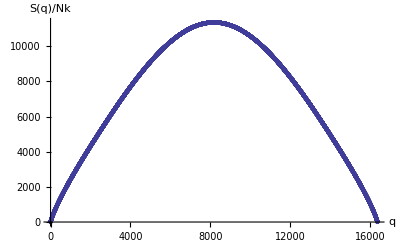

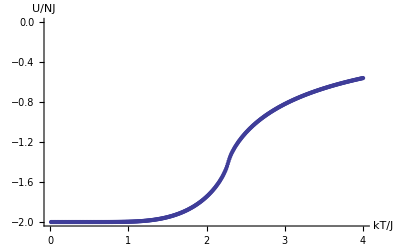

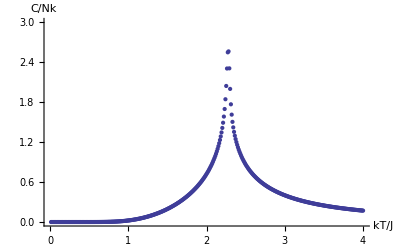

s={0.69314718055994530942,-∞,10.397207708399179641,11.090354888959124951,19.408670221265690626,20.79478156069700032,28.015947669830980804,29.806610165301302274,36.337548100585900364,38.413766146124129682,44.438721312130023497,46.734274664762024817,52.360975866328868476,54.832914246238131565,60.133131008973850183,62.750743676052213891,67.776401126498481347,70.516166124949918909,75.307060994043089343,78.150027227546129611,82.737976577706259161,85.668294165151346303,90.079547025940837122,93.083599100715829989,97.340317626397921604,100.40619114524072955,104.52739842225103368,107.64455535368843127,111.64676292188472799,114.80583256301393033,118.70346995437677099,121.896114186390643,125.70183433523389352,128.92065532123565924,132.64556193349695939,135.88403270832015321,139.53785875234809904,142.79026441099784407,146.38152007635790408,149.64290228621233469,153.17900365377288358,156.44510471352216925,159.93248969460078472,163.19969473383227075,166.64392980480009552,169.90920722199641377,173.31508660530490003,176.57592768496761888,179.94756555446236552,183.20192456502500648,186.54284032000046397,189.78907642817432596,193.10227289087461793,196.33909506294184526,199.62712946539017379,202.85354526010897958,206.11859299882975744,209.33386185984686914,212.5777731460508344,215.78136451892240088,219.00571419768453568,222.19727055295712249,225.40340148684798798,228.58270613700235776,231.7717666388565303,234.93871609463895799,238.11169194962269929,241.266272466112503,244.42401410824096757,247.56628201582547288,250.709527423857592,253.83959281605447783,256.96898667413065275,260.08700002507054861,263.20310966017229395,266.30925096253369734,269.41257952876388435,272.50704957216300013,275.59804690503113617,278.68106035061515125,281.7601318661361309,284.83191181182035577,287.8994257776472642,290.96019954745455194,294.0164930081041591,297.06648893659716796,300.11187253314105742,303.15131755081915082,306.18607943778986717,309.21519729488653817,312.23960632382022865,315.25861631788839939,318.2729246278711337,321.28204072485115532,324.28648585545807469,327.28591611473395358,330.28072273554004098,333.27066896706258775,336.25605030009078515,339.23670789630319228,342.21286689296437101,345.1844247903528361,348.15155511222836484,351.11419584718454891,354.072482690030155,357.02638252168360618,359.97600331394669414,362.92133239300716545,365.86245739363796375,368.79937996135097004,371.73217277647766682,374.66084738177883974,377.58546541567235593,380.50604514173086698,383.42263999420546972,386.33527268794622118,389.24399050775940485,392.14881900779145492,395.04980080958072436,397.9469631693538134,400.84034512006454658,403.72997482412298541,406.61588850364722959,409.49811467562848073,412.37668731541424748,415.25163491701030438,418.12298961965464244,420.9907796401668713,423.8550355824260827,426.7157852188370385,429.57305784003632848,432.42688066772514341,435.27728184519836827,438.12428797956275018,440.96792619247786589,443.80822244181322778,446.64520292452282536,449.4788929345610286,452.30931782044630975,455.13650221098306144,457.96047066762327478,460.78124716167192838,463.59885551806163405,466.4133190639675945,469.22466093041503768,472.03290381735326567,474.83807019861996458,477.64018216588118136,480.43926156806203752,483.23532990851327891,486.02840844010541159,488.81851809818906946,491.60567956575412245,494.38991323036758241,497.17123922915489607,499.94967742173103587,502.72524742159663485,505.49796857968424696,508.26786000661215528,511.03494056323508574,513.79922887674234331,516.56074333579696035,519.31950210248133351,522.07552311041393101,524.82882407388325643,527.57942248787217968,530.32733563527621643,533.07258058812785222,535.81517421349716975,538.55513317545042776,541.2924739400320064,544.0272127776524765,546.75936576741816216,549.48894879975069811,552.2159775802422815,554.94046763237926784,557.66243430104262545,560.38189275525456292,563.09885799140489288,565.81334483597012227,568.52536794852074048,571.23494182438205264,573.94208079746040233,576.64679904282789338,579.34911057939429328,582.04902927240606417,584.74656883598321474,587.44174283552833121,590.13456469014265911,592.82504767494413555,595.51320492337363429,598.19904942942303908,600.88259404984031409,603.56385150626987539,606.2428343873635851,608.91955515083636868,611.59402612548913308,614.2662595131829338,616.93626739077902647,619.6040617120350334,622.26965430946675173,624.93305689616978495,627.59428106760728087,630.25333830336043104,632.91023996884595484,635.56499731699876166,638.21762148992270417,640.86812352050856557,643.51651433402135717,646.16280474965664867,648.80700548206746999,651.44912714286185482,654.08918024207221597,656.72717518959682607,659.36312229661436395,661.99703177697191427,664.62891374854722601,667.25877823458567649,669.88663516501263923,672.51249437772172798,675.13636561983953833,677.75825854896736442,680.37818273440045487,682.99614765832527894,685.61216271699532213,688.22623722188586903,690.83838040082825617,693.44860139912403582,696.05690928063950275,698.66331302888100638,701.26782154805147335,703.87044366408854413,706.4711881256847246,709.07006360528993731,711.66707870009685174,714.26224193300935967,716.85556175359455512,719.44704653901856725,722.03670459496658719,724.62454415654742011,727.21057338918288649,729.79480038948238757,732.37723318610294297,734.95787974059500009,737.53674794823430818,740.11384563884014211,742.68918057758015468,745.26276046576212865,747.83459294161289393,750.40468558104466826,752.97304589840907393,755.53968134723907701,758.10459932097908926,760.66780715370346787,763.22931212082364191,765.78912143978408946,768.34724227074738396,770.9036817172685231,773.45844682695874881,776.01154459213906184,778.56298195048362992,781.11276578565328383,783.66090292791929104,786.20740015477759267,788.75226419155368489,791.29550171199832197,793.83711933887421409,796.37712364453388928,798.9155211514888848,801.4523183329704298,803.98752161348177741,806.52113736934234082,809.05317192922378467,811.58363157467821961,814.11252254065864455,816.63985101603177828,819.16562314408341865,821.68984502301646483,824.21252270644173507,826.73366220386170948,829.25326948114732474,831.77135046100794481,834.28791102345462908,836.80295700625681679,839.31649420539254414,841.82852837549230795,844.33906523027668734,846.84811044298783263,849.35566964681492833,851.86174843531373484,854.36635236282031139,856.86948694485902052,859.37115765854491253,861.87136994298058593,864.37012919964761849,866.86744079279266104,869.36331004980828465,871.85774226160866978,874.35074268300022439,876.842316533047216,879.33246899543250125,881.82120521881343465,884.30853031717303661,886.79444937016649945,889.27896742346310812,891.76208948908365136,894.24382054573339703,896.72416553913070434,899.20312938233134402,901.68071695604859602,904.15693310896919342,906.63178265806517926,909.1052703889017423,911.57740105594109606,914.04817938284246449,916.5176100627582362,918.98569775862634828,921.45244710345895924,923.91786270062746983,926.38194912414394901,928.84471091893902174,931.30615260113627361,933.76627865832322687,936.22509354981894104,938.68260170693829038,941.13880753325296962,943.59371540484927833,946.04732967058273328,948.49965465232955753,950.95069464523509369,953.40045391795918841,955.84893671291859374,958.2961472465264307,960.7420897094287593,963.18676826673829844,965.63018705826533846,968.07235019874588827,970.51326177806709831,972.95292586148999971,975.3913464898695995,977.82852767987237087,980.26447342419117678,982.69918769175766475,985.13267442795216964,987.56493755481116105,989.9959809712322708,992.42580855317693583,994.85442415387069089,997.28183160400114503,999.7080347119136751,1002.1330372638048691,1004.5568430239137517,1006.9794557347108229,1009.4008791170849422,1011.8211168705280876,1014.24017267331802,1016.6580501826988827,1019.0747530350597646,1021.4902848461112566,1023.9046492110600275,1026.3178497047814492,1028.7298898819902967,1031.1407732774095502,1033.5505034059373258,1035.95908376281196,1038.3665178237752739,1040.7728090452340422,1043.1779608644196905,1045.581976699546247,1047.9848599499665701,1050.3866139963268771,1052.7872422007195962,1055.1867479068345644,1057.5851344401085937,1059.9824051078734279,1062.3785631995021106,1064.7736119865537869,1067.1675547229169583,1069.5603946449512126,1071.9521349716274477,1074.342778904666611,1076.7323296286769719,1079.1207903112899482,1081.5081641032945047,1083.894454138770143,1086.2796635352185005,1088.663795393693577,1091.0468527989306065,1093.4288388194735922,1095.809756507801521,1098.1896089004532757,1100.568399018151261,1102.9461298659237591,1105.322804433226033,1107.6984256940601914,1110.0729966070938322,1112.4465201157774799,1114.8189991484608318,1117.1904366185078284,1119.5608354244105626,1121.9301984499020423,1124.298528564067821,1126.6658286214565101,1129.032101462189187,1131.3973499120677133,1133.7615767826819758,1136.1247848715160637,1138.486976962053396,1140.8481558238808109,1143.2083242127916309,1145.5674848708877151,1147.9256405266805122,1150.282793895191126,1152.6389476780494044,1154.994104563592066,1157.3482672269598731,1159.7014383301938654,1162.0536205223306634,1164.4048164394968545,1166.7550287050024712,1169.1042599294335738,1171.452512710743947,1173.7997896343459219,1176.1460932732003329,1178.4914261879056206,1180.8357909267860902,1183.179190025979336,1185.5216260095228404,1187.8631013894397592,1190.2036186658239013,1192.5431803269239116,1194.8817888492266686,1197.2194466975399041,1199.5561563250740538,1201.8919201735233493,1204.2267406731461587,1206.5606202428445854,1208.8935612902433334,1211.2255662117678469,1213.5566373927217335,1215.8867772073634786,1218.2159880189824594,1220.5442721799742655,1222.8716320319153356,1225.1980699056369169,1227.5235881212983546,1229.8481889884597199,1232.1718748061537841,1234.4946478629573446,1236.816510437061912,1239.1374647963437634,1241.4575131984333715,1243.7766578907842139,1246.0949011107409708,1248.4122450856071179,1250.7286920327119206,1253.0442441594768368,1255.3589036634813341,1257.6726727325281282,1259.9855535447078489,1262.2975482684631398,1264.6086590626521976,1266.9188880766117581,1269.2282374502195334,1271.5367093139561076,1273.844305788966296,1276.1510289871199744,1278.4568810110723825,1280.76186395432391,1283.0659799012793673,1285.3692309273067497,1287.6716190987954982,1289.9731464732142631,1292.2738150991681761,1294.5736270164556348,1296.8725842561246065,1299.170688840528455,1301.4679427833812958,1303.7643480898128854,1306.0599067564230479,1308.3546207713356457,1310.6484921142520979,1312.941522756504451,1315.2337146611080076,1317.5250697828135165,1319.8155900681589292,1322.1052774555207278,1324.3941338751648283,1326.6821612492970625,1328.9693614921132457,1331.2557365098488316,1333.5412882008281598,1335.8260184555133003,1338.109929156552499,1340.3930221788282274,1342.6752993895048419,1344.9567626480758555,1347.2374138064108265,1349.5172547088018676,1351.7962871920097796,1354.0745130853098138,1356.3519342105370652,1358.6285523821315025,1360.9043694071826367,1363.179387085473833,1365.4536072095262688,1367.7270315646425418,1369.9996619289499316,1372.271500073443318,1374.5425477620277596,1376.812806751560736,1379.0822787918940567,1381.3509656259154406,1383.6188689895897688,1385.885990612000013,1388.1523322153878455,1390.4178955151939304,1392.6826822200979015,1394.9466940320580291,1397.2099326463505789,1399.4723997516088657,1401.734097029862005,1403.9950261565733658,1406.2551888006787265,1408.5145866246241379,1410.7732212844034955,1413.0310944295958235,1415.2882077034022744,1417.5445627426828453,1419.8001611779928155,1422.0550046336189061,1424.3090947276151658,1426.5624330718385848,1428.8150212719844387,1431.0668609276213669,1433.3179536322261854,1435.5683009732184393,1437.8179045319946942,1440.0667658839625727,1442.3148865985745346,1444.5622682393614063,1446.8089123639656597,1449.0548205241744439,1451.2999942659523717,1453.5444351294740628,1455.7881446491564473,1458.0311243536908298,1460.2733757660747175,1462.5149004036434143,1464.7556997781013834,1466.9957753955533788,1469.2351287565353506,1471.4737613560451237,1473.7116746835728527,1475.9488702231312564,1478.1853494532856313,1480.4211138471836487,1482.656164872584935,1484.8905039918904398,1487.1241326621715909,1489.3570523351992399,1491.5892644574724005,1493.8207704702467794,1496.0515718095631039,1498.281669906275247,1500.5110661860781511,1502.7397620695355539,1504.9677589721075161,1507.1950583041777549,1509.4216614710807826,1511.6475698731288543,1513.8727849056387251,1516.0973079589582181,1518.3211404184926067,1520.5442836647308104,1522.7667390732714078,1524.988508014848467,1527.2095918553571961,1529.4299919558794142,1531.6497096727088455,1533.8687463573762376,1536.0871033566743048,1538.3047820126825001,1540.521783662791614,1542.7381096397282056,1544.9537612715788632,1547.1687398818142999,1549.3830467893132822,1551.5966833083863959,1553.809650748799648,1556.0219504157979086,1558.2335836101281917,1560.4445516280627785,1562.6548557614221829,1564.8644972975979612,1567.0734775195753675,1569.2817977059558554,1571.4894591309794285,1573.6964630645468393,1575.9028107722416393,1578.1085035153520808,1580.3135425508928719,1582.5179291316267855,1584.7216645060861239,1586.9247499185940405,1589.1271866092857188,1591.3289758141294112,1593.5301187649473375,1595.7306166894364449,1597.9304708111890307,1600.1296823497132291,1602.3282525204533616,1604.526182534810155,1606.7234736001608247,1608.9201269198790277,1611.1161436933546834,1613.311525116013666,1615.506272379337367,1617.7003866708821307,1619.8938691742985632,1622.0867210693507158,1624.2789435319351432,1626.4705377340998391,1628.6615048440630484,1630.8518460262319589,1633.041562441221271,1635.2306552458716492,1637.419125593268054,1639.6069746327579564,1641.7942035099694359,1643.9808133668291619,1646.1668053415802614,1648.3521805688000716,1650.5369401794177799,1652.7210853007319518,1654.904617056427947,1657.087536566595226,1659.2698449477445462,1661.4515433128250497,1663.6326327712412434,1665.8131144288698722,1667.9929893880766853,1670.1722587477330985,1672.3509236032327506,1674.5289850465079571,1676.7064441660460609,1678.8833020469056803,1681.0595597707328569,1683.2352184157771016,1685.4102790569073421,1687.584742765627771,1689.7586106100935954,1691.93188365512669,1694.1045629622311521,1696.2766495896087627,1698.4481445921743502,1700.6190490215710615,1702.789363926185538,1704.9590903511629999,1707.1282293384222369,1709.2967819266705081,1711.4647491514183511,1713.6321320449943,1715.7989316365595152,1717.9651489521223231,1720.1307850145526682,1722.2958408435964783,1724.4603174558899412,1726.6242158649736971,1728.7875370813069442,1730.9502821122814598,1733.1124519622355371,1735.2740476324678386,1737.4350701212511659,1739.595520423846148,1741.7553995325148467,1743.914708436534282,1746.073448122209876,1748.2316195728888175,1750.3892237689733467,1752.5462616879339616,1754.7027343043225457,1756.8586425897854186,1759.013987513076309,1761.1687700400692519,1763.3229911337714088,1765.476651754335814,1767.6297528590740446,1769.7822954024688172,1771.9342803361865107,1774.0857086090896155,1776.2365811672491106,1778.3868989539567681,1780.5366629097373865,1782.6858739723609525,1784.8345330768547324,1786.982641155515294,1789.1301991379204577,1791.2772079509411798,1793.4236685187533664,1795.5695817628496199,1797.7149486020509173,1799.8597699525182215,1802.0040467277640268,1804.147779838663837,1806.2909701934675789,1808.4336186978109499,1810.5757262547267014,1812.7172937646558576,1814.8583221254588703,1816.9988122324267111,1819.1387649782918997,1821.2781812532394707,1823.4170619449178775,1825.5554079384498352,1827.693220116443102,1829.8304993590012003,1831.9672465437340769,1834.1034625457687039,1836.2391482377596196,1838.3743044898994111,1840.5089321699291371,1842.643032143148694,1844.7766052724271226,1846.9096524182128588,1849.0421744385439262,1851.1741721890580725,1853.3056465230028501,1855.43659829124564,1857.5670283422836209,1859.696937522253683,1861.8263266749422868,1863.9551966417952685,1866.0835482619275903,1868.2113823721330381,1870.3386998068938652,1872.4655013983903835,1874.5917879765105029,1876.7175603688592169,1878.8428194007680384,1880.9675658953043824,1883.0918006732808988,1885.2155245532647538,1887.3387383515868614,1889.4614428823510641,1891.5836389574432652,1893.70532738654051,1895.8265089771200199,1897.947184534468176,1900.0673548616894556,1902.18702075971532,1904.3061830273130549,1906.424842461094563,1908.5429998555251101,1910.6606560029320236,1912.7778116935133457,1914.8944677153464391,1917.0106248543965478,1919.126283894525312,1921.241445617499238,1923.3561108029981228,1925.470280228623434,1927.5839546699066461,1929.6971349003175319,1931.8098216912724105,1933.9220158121423517,1936.0337180302613374,1938.1449291109343801,1940.2556498174455981,1942.3658809110662495,1944.4756231510627232,1946.5848772947044886,1948.6936440972720032,1950.8019243120645798,1952.9097186904082119,1955.0170279816633592,1957.1238529332326913,1959.230194290568793,1961.3360527971818283,1963.441429194647165,1965.5463242226129605,1967.6507386188077075,1969.7546731190477416,1971.8581284572447097,1973.9611053654130004,1976.0636045736771356,1978.1656268102791252,1980.2671728015857828,1982.3682432720960053,1984.4688389444480142,1986.5689605394265606,1988.6686087759700932,1990.7677843711778902,1992.8664880403171538,1994.9647204968300704,1997.0624824523408335,1999.1597746166626317,2001.2565976978046011,2003.3529524019787432,2005.4488394336068068,2007.544259495327136,2009.6392132880014836,2011.7337015107217902,2013.8277248608169289,2015.9212840338594169,2018.0143797236720929,2020.1070126223347612,2022.1991834201908027,2024.2908928058537532,2026.382141466213848,2028.472930086444535,2030.5632593500089547,2032.6531299386663884,2034.7425425324786741,2036.8314978098165911,2038.9199964473662122,2041.0080391201352255,2043.0956265014592243,2045.1827592630079664,2047.2694380747916021,2049.3556636051668719,2051.4414365208432742,2053.5267574868892018,2055.611627166738049,2057.6960462221942885,2059.7800153134395192,2061.8635350990384834,2063.9466062359450557,2066.0292293795082022,2068.1114051834779109,2070.1931343000110932,2072.2744173796774568,2074.3552550714653501,2076.4356480227875784,2078.5155968794871921,2080.5951022858432464,2082.6741648845765342,2084.7527853168552903,2086.8309642223008688,2088.9087022389933933,2090.9860000034773794,2093.0628581507673311,2095.1392773143533094,2097.2152581262064751,2099.2908012167846048,2101.3659072150375806,2103.4405767484128534,2105.5148104428608809,2107.5886089228405388,2109.6619728113245071,2111.7349027298046305,2113.8073992982972534,2115.8794631353485298,2117.9510948580397078,2120.0222950819923898,2122.0930644213737671,2124.1634034889018303,2126.2333128958505553,2128.3027932520550646,2130.3718451659167645,2132.4404692444084587,2134.5086660930794368,2136.5764363160605401,2138.6437805160692038,2140.7106992944144743,2142.7771932510020051,2144.8432629843390274,2146.9089090915392995,2148.9741321683280318,2151.0389328090467897,2153.1033116066583734,2155.1672691527516756,2157.2308060375465159,2159.2939228498984542,2161.3566201773035804,2163.4188986059032831,2165.4807587204889959,2167.5422011045069222,2169.6032263400627382,2171.6638350079262736,2173.7240276875361725,2175.7838049570045313,2177.8431673931215164,2179.9021155713599605,2181.9606500658799378,2184.0187714495333191,2186.0764802938683051,2188.1337771691339397,2190.1906626442846032,2192.2471372869844842,2194.3032016636120321,2196.3588563392643889,2198.4141018777618013,2200.4689388416520127,2202.5233677922146358,2204.5773892894655048,2206.6310038921610087,2208.6842121578024048,2210.7370146426401129,2212.7894119016779903,2214.8414044886775878,2216.8929929561623861,2218.9441778554220142,2220.9949597365164481,2223.0453391482801912,2225.0953166383264364,2227.1448927530512087,2229.1940680376374906,2231.2428430360593284,2233.2912182910859207,2235.3391943442856882,2237.3867717360303265,2239.4339510054988401,2241.4807326906815592,2243.5271173283841383,2245.5731054542315373,2247.6186976026719859,2249.663894306980929,2251.7086960992649566,2253.7531035104657149,2255.7971170703638013,2257.8407373075826421,2259.8839647495923529,2261.9267999227135825,2263.9692433521213404,2266.0112955618488066,2268.0529570747911259,2270.0942284127091851,2272.1351100962333741,2274.1756026448673304,2276.2157065769916676,2278.255422409867688,2280.2947506596410785,2282.3336918413455912,2284.3722464689067077,2286.4104150551452881,2288.4481981117812035,2290.485596149436954,2292.5226096776412699,2294.5592392048326987,2296.5954852383631757,2298.6313482845015802,2300.6668288484372755,2302.7019274342836351,2304.7366445450815524,2306.7709806828029366,2308.8049363483541932,2310.8385120415796898,2312.871708261265207,2314.9045255051413752,2316.936964269887096,2318.9690250511329503,2321.0007083434645903,2323.0320146404261193,2325.0629444345234549,2327.0934982172276804,2329.12367647897838,2331.1534797091869612,2333.1829083962399633,2335.2119630275023509,2337.240644089320795,2339.2689520670269394,2341.2968874449406536,2343.3244507063732727,2345.3516423336308227,2347.3784628080172336,2349.4049126098375379,2351.4309922184010567,2353.4567021120245723,2355.4820427680354872,2357.5070146627749706,2359.5316182716010916,2361.5558540688919394,2363.5797225280487308,2365.6032241214989041,2367.6263593206992017,2369.6491285961387385,2371.6715324173420586,2373.6935712528721789,2375.7152455703336207,2377.7365558363754281,2379.7575025166941753,2381.7780860760369597,2383.7983069782043849,2385.8181656860535296,2387.8376626615009059,2389.8567983655254041,2391.875573258171227,2393.893987798550811,2395.9120424448477359,2397.9297376543196232,2399.9470738833010216,2401.9640515872062819,2403.9806712205324197,2405.9969332368619666,2408.01283808886581,2410.0283862283060211,2412.043578106038672,2414.058414172016641,2416.072894875292407,2418.0870206640208321,2420.1007919854619339,2422.1142092859836457,2424.1272730110645663,2426.1399836052966987,2428.1523415123881775,2430.1643471751659858,2432.1760010355786611,2434.1873035346989902,2436.1982551127266939,2438.2088562089911006,2440.219107261953809,2442.2290087092113412,2444.2385609874977842,2446.2477645326874214,2448.256619779797354,2450.2651271629901116,2452.2732871155762524,2454.2811000700169533,2456.2885664579265903,2458.2956867100753077,2460.3024612563915782,2462.308890525964752,2464.3149749470475969,2466.3207149470588276,2468.3261109525856253,2470.3311633893861479,2472.3358726823920297,2474.3402392557108719,2476.3442635326287227,2478.3479459356125489,2480.3512868863126962,2482.3542868055653418,2484.3569461133949358,2486.3592652290166342,2488.361244570838722,2490.3628845564650272,2492.3641856026973249,2494.3651481255377328,2496.3657725401910969,2498.3660592610673686,2500.3660087017839715,2502.3656212751681606,2504.3648973932593712,2506.3638374673115592,2508.3624419077955328,2510.3607111244012745,2512.3586455260402544,2514.3562455208477357,2516.3535115161850693,2518.3504439186419818,2520.3470431340388533,2522.3433095674289871,2524.3392436231008709,2526.3348457045804286,2528.3301162146332647,2530.3250555552668991,2532.3196641277329941,2534.3139423325295729,2536.307890569403229,2538.3015092373513283,2540.2947987346242022,2542.2877594587273323,2544.2803918064235275,2546.2726961737350923,2548.2646729559459872,2550.2563225476039811,2552.2476453425227951,2554.2386417337842388,2556.2293121137403384,2558.2196568740154567,2560.2096764055084053,2562.1993710983945492,2564.1887413421279024,2566.1777875254432175,2568.1665100363580658,2570.1549092621749104,2572.1429855894831719,2574.1307394041612859,2576.1181710913787528,2578.1052810355981805,2580.0920696205773191,2582.0785372293710882,2584.0646842443335969,2586.0505110471201558,2588.0360180186892822,2590.0212055393046975,2592.0060739885373175,2593.9906237452672351,2595.9748551876856956,2597.9587686932970657,2599.9423646389207937,2601.9256434006933641,2603.9086053540702439,2605.891250873827822,2607.8735803340653425,2609.8555941082068292,2611.8372925690030047,2613.8186760885332013,2615.7997450382072658,2617.7804997887674571,2619.7609407102903365,2621.7410681721886516,2623.7208825432132134,2625.7003841914547663,2627.6795734843458512,2629.6584507886626628,2631.6370164705268986,2633.615270895407603,2635.5932144281230032,2637.5708474328423398,2639.5481702730876895,2641.5251833117357824,2643.5018869110198122,2645.4782814325312398,2647.454367237221591,2649.4301446854042468,2651.4056141367562286,2653.3807759503199757,2655.3556304845051174,2657.3301780970902382,2659.3044191452246371,2661.2783539854300803,2663.2519829736025482,2665.2253064650139752,2667.1983248143139844,2669.1710383755316156,2671.1434475020770472,2673.115552546743312,2675.0873538617080072,2677.058851798534998,2679.0300467081761151,2681.000938940972847,2682.9715288466580253,2684.9418167743575047,2686.9118030725918371,2688.8814880892779392,2690.8508721717307552,2692.8199556666649129,2694.7887389201963745,2696.7572222778440808,2698.7254060845315909,2700.6932906845887153,2702.6608764217531433,2704.6281636391720651,2706.595152679403788,2708.5618438844193472,2710.5282375956041107,2712.4943341537593788,2714.4601338991039781,2716.4256371712758497,2718.3908443093336324,2720.3557556517582399,2722.3203715364544328,2724.284692300752385,2726.2487182814092453,2728.2124498146106926,2730.1758872359724864,2732.1390308805420122,2734.1018810827998209,2736.0644381766611633,2738.0267024954775193,2739.988674372038122,2741.9503541385714762,2743.9117421267468721,2745.8728386676758937,2747.8336440919139216,2749.7941587294616316,2751.7543829097664875,2753.7143169617242287,2755.6739612136803534,2757.6333159934315964,2759.5923816282274014,2761.5511584447713894,2763.509646769222821,2765.4678469271980546,2767.4257592437719989,2769.3833840434795615,2771.3407216503170914,2773.2977723877438177,2775.2545365786832829,2777.2110145455247711,2779.1672066101247325,2781.1231130938082017,2783.0787343173702124,2785.0340706010772065,2786.9891222646684392,2788.943889627357379,2790.8983730078331027,2792.8525727242616868,2794.8064890942875929,2796.7601224350350496,2798.7134730631094292,2800.6665412945986198,2802.6193274450743935,2804.5718318295937689,2806.5240547627003703,2808.4759965584257815,2810.4276575302908957,2812.3790379913072604,2814.3301382539784184,2816.280958630301244,2818.2314994317672747,2820.1817609693640391,2822.1317435535763799,2824.0814474943877725,2826.0308731012816394,2827.9800206832426609,2829.9288905487580803,2831.8774830058190057,2833.8257983619217072,2835.7738369240689102,2837.721598998771084,2839.6690848920477263,2841.6162949094286441,2843.5632293559552293,2845.5098885361817312,2847.4562727541765246,2849.4023823135233731,2851.3482175173226893,2853.2937786681927903,2855.2390660682711492,2857.1840800192156427,2859.1288208222057946,2861.0732887779440153,2863.0174841866568371,2864.9614073480961459,2866.9050585615404087,2868.8484381257958967,2870.7915463391979059,2872.7343834996119719,2874.676949904435082,2876.6192458505968834,2878.5612716345608869,2880.5030275523256672,2882.4445138994260596,2884.3857309709343518,2886.3266790614614734,2888.2673584651581806,2890.2077694757162371,2892.1479123863695918,2894.0877874898955524,2896.0273950786159556,2897.9667354443983327,2899.9058088786570729,2901.8446156723545814,2903.7831561160024353,2905.7214304996625347,2907.6594391129482507,2909.5971822450255697,2911.5346601846142341,2913.4718732199888794,2915.4088216389801675,2917.345505728975917,2919.2819257769222293,2921.2180820693246117,2923.1539748922490964,2925.0896045313233567,2927.0249712717378193,2928.960075398246773,2930.8949171951694741,2932.8294969463912488,2934.763814935364591,2936.6978714451102582,2938.6316667582183627,2940.56520115684946,2942.498474922735634,2944.4314883371815783,2946.3642416810656745,2948.2967352348410671,2950.2289692785367354,2952.160944091758561,2954.0926599536903937,2956.0241171430951123,2957.9553159383156837,2959.8862566172762179,2961.8169394574830194,2963.7473647360256368,2965.6775327295779074,2967.6074437143990001,2969.5370979663344541,2971.466495760817215,2973.3956373728686675,2975.3245230770996648,2977.2531531477115554,2979.1815278584972061,2981.1096474828420224,2983.0375122937249654,2984.9651225637195661,2986.8924785649949361,2988.8195805693167757,2990.7464288480483784,2992.6730236721516329,2994.5993653121880219,2996.5254540383196176,2998.4512901203100749,3000.3768738275256205,3002.3022054289360403,3004.2272851931156626,3006.1521133882443394,3008.0766902821084243,3010.0010161421017471,3011.9250912352265862,3013.8489158280946374,3015.7724901869279805,3017.6958145775600425,3019.618889265436558,3021.541714515616527,3023.4642905927731696,3025.3866177611948776,3027.3086962847861642,3029.2305264270686098,3031.1521084511818059,3033.0734426198842952,3034.9945291955545101,3036.9153684401917074,3038.8359606154169009,3040.7563059824737909,3042.6764048022296912,3044.5962573351764529,3046.5158638414313863,3048.4352245807381794,3050.3543398124678138,3052.2732097956194781,3054.1918347888214788,3056.1102150503321478,3058.0283508380407484,3059.9462424094683773,3061.8638900217688651,3063.7812939317296737,3065.6984543957727909,3067.6153716699556229,3069.5320460099718838,3071.4484776711524824,3073.3646669084664073,3075.280613976521608,3077.196319129565875,3079.1117826214877163,3081.0270047058172314,3082.9419856357269837,3084.8567256640328691,3086.7712250431949833,3088.6854840253184857,3090.5995028621544612,3092.5132818051007797,3094.4268211052029527,3096.340121013154988,3098.2531817793002412,3100.1660036536322656,3102.078586885795659,3103.9909317250869085,3105.9030384204552329,3107.8149072205034222,3109.7265383734886753,3111.6379321273234351,3113.5490887295762212,3115.4600084274724603,3117.3706914678953139,3119.2811380973865046,3121.1913485621471388,3123.101323108038528,3125.0110619805830077,3126.9205654249647535,3128.829833686030595,3130.7388670082908284,3132.6476656359200251,3134.5562298127578397,3136.4645597823098145,3138.3726557877481826,3140.2805180719126682,3142.1881468773112849,3144.0955424461211318,3146.0027050201891873,3147.9096348410331009,3149.8163321498419822,3151.7227971874771886,3153.6290301944731099,3155.5350314110379516,3157.4408010770545153,3159.3463394320809774,3161.2516467153516654,3163.1567231657778323,3165.0615690219484283,3166.9661845221308715,3168.8705699042718153,3170.774725405997914,3172.6786512646165871,3174.5823477171167802,3176.485815000169725,3178.3890533501296965,3180.2920630030347683,3182.1948441946075659,3184.0973971602560181,3185.9997221350741061,3187.9018193538426106,3189.8036890510298568,3191.705331460792458,3193.606746816976056,3195.5079353531160607,3197.4088973024383872,3199.3096328978601903,3201.2101423719905985,3203.1104259571314444,3205.0104838852779942,3206.9103163881196749,3208.8099236970407995,3210.7093060431212903,3212.6084636571374004,3214.5073967695624331,3216.4061056105674592,3218.3045904100220331,3220.2028513974949058,3222.1008888022547375,3223.9987028532708069,3225.8962937792137196,3227.7936618084561138,3229.6908071690733651,3231.5877300888442888,3233.4844307952518399,3235.3809095154838126,3237.2771664764335365,3239.1732019047005722,3241.069016026591404,3242.9646090681201315,3244.8599812550091591,3246.7551328126898839,3248.6500639663033813,3250.5447749407010897,3252.4392659604454923,3254.333537249810798,3256.2275890327836201,3258.1214215330636536,3260.0150349740643499,3261.9084295789135912,3263.8016055704543613,3265.6945631712454165,3267.5873026035619534,3269.4798240893962757,3271.3721278504584589,3273.2642141081770137,3275.1560830836995472,3277.0477349978934228,3278.9391700713464183,3280.8303885243673819,3282.7213905769868874,3284.6121764489578869,3286.5027463597563621,3288.3931005285819741,3290.2832391743587115,3292.1731625157355366,3294.0628707710870302,3295.9523641585140347,3297.8416428958442956,3299.7307072006331013,3301.6195572901639212,3303.5081933814490426,3305.3966156912302054,3307.2848244359792359,3309.172819831898678,3311.0606020949224241,3312.9481714407163433,3314.8355280846789085,3316.7226722419418224,3318.6096041273706405,3320.4963239555653944,3322.3828319408612123,3324.2691282973289379,3326.1552132387757488,3328.0410869787457724,3329.9267497305207003,3331.8122017071204022,3333.6974431213035367,3335.5824741855681622,3337.4672951121523449,3339.3519061130347664,3341.236307399935329,3343.1204991843157603,3345.0044816773802154,3346.8882550900758784,3348.7718196330935619,3350.6551755168683056,3352.538322951579973,3354.4212621471538463,3356.303993313261221,3358.1865166593199981,3360.0688323944952749,3361.950940727699935,3363.8328418675952361,3365.714536022591397,3367.596023400848183,3369.4773042102754895,3371.358378658533925,3373.2392469530353918,3375.119909300943666,3377.0003659091749758,3378.8806169843985785,3380.760662733037336,3382.6405033612682891,3384.5201390750232303,3386.3995700799892756,3388.2787965816094339,3390.1578187850831769,3392.0366368953670056,3393.9152511171750167,3395.7936616549794678,3397.67186871301134,3399.549872495260901,3401.4276732054782651,3403.3052710471739532,3405.1826662236194506,3407.0598589378477645,3408.9368493926539786,3410.8136377905958085,3412.6902243339941539,3414.5666092249336505,3416.4427926652632207,3418.3187748565966227,3420.194556000312998,3422.0701362975574185,3423.9455159492414317,3425.8206951560436049,3427.6956741184100679,3429.5704530365550548,3431.4450321104614444,3433.3194115398812993,3435.1935915243364036,3437.0675722631188003,3438.9413539552913259,3440.8149367996881454,3442.6883209949152849,3444.5615067393511638,3446.4344942311471251,3448.3072836682279652,3450.179875248292462,3452.052269168813902,3453.9244656270406063,3455.7964648199964552,3457.6682669444814117,3459.5398721970720442,3461.4112807741220475,3463.2824928717627628,3465.1535086859036969,3467.0243284122330395,3468.8949522462181803,3470.7653803831062244,3472.6356130179245063,3474.5056503454811034,3476.3754925603653484,3478.2451398569483394,3480.1145924293834506,3481.9838504716068406,3483.8529141773379603,3485.721783740080059,3487.5904593531206904,3489.4589412095322165,3491.3272295021723109,3493.1953244236844612,3495.0632261664984699,3496.9309349228309543,3498.7984508846858457,3500.665774243854887,3502.5329051919181297,3504.3998439202444293,3506.2665906199919405,3508.1331454821086105,3509.9995086973326714,3511.8656804561931321,3513.7316609490102688,3515.5974503658961141,3517.4630488967549458,3519.3284567312837741,3521.1936740589728281,3523.0587010691060411,3524.9235379507615351,3526.7881848928121038,3528.6526420839256955,3530.516909712565894,3532.3809879669923989,3534.2448770352615054,3536.1085771052265823,3537.9720883645385494,3539.8354110006463543,3541.6985452007974472,3543.5614911520382558,3545.4242490412146587,3547.2868190549724579,3549.1492013797578503,3551.0113962018178984,3552.873403707201,3554.7352240817573567,3556.5968575111394421,3558.458304180802468,3560.3195642760048509,3562.1806379818086766,3564.0415254830801644,3565.9022269644901301,3567.7627426105144482,3569.6230726054345134,3571.4832171333377006,3573.3431763781178247,3575.2029505234755988,3577.0625397529190923,3578.9219442497641874,3580.7811641971350347,3582.6401997779645088,3584.4990511749946618,3586.357718570777177,3588.2162021476738208,3590.0745020878568944,3591.9326185733096845,3593.7905517858269128,3595.6483019070151848,3597.5058691182934384,3599.3632536008933902,3601.2204555358599824,3603.0774751040518281,3604.934312486141656,3606.7909678626167539,3608.6474414137794119,3610.5037333197473645,3612.359843760454232,3614.2157729156499604,3616.0715209649012618,3617.9270880875920527,3619.7824744629238922,3621.6376802699164192,3623.4927056874077888,3625.3475508940551079,3627.2022160683348699,3629.0567013885433889,3630.9110070327972327,3632.7651331790336554,3634.619080005011029,3636.4728476883092742,3638.3264364063302905,3640.1798463362983856,3642.0330776552607038,3643.8861305400876542,3645.739005167473337,3647.5917017139359704,3649.4442203558183159,3651.2965612692881029,3653.1487246303384529,3655.0007106147883027,3656.8525193982828272,3658.7041511562938605,3660.5556060641203178,3662.4068842968886151,3664.2579860295530891,3666.1089114368964159,3667.9596606935300296,3669.810233973894539,3671.660631452260145,3673.5108533027270565,3675.3608996992259054,3677.2107708155181614,3679.0604668251965461,3680.9099879016854461,3682.7593342182413254,3684.6085059479531374,3686.4575032637427362,3688.3063263383652867,3690.1549753444096748,3692.0034504542989163,3693.8517518402905654,3695.6998796744771227,3697.547834128786442,3699.3956153749821371,3701.2432235846639874,3703.0906589292683431,3704.9379215800685299,3706.7850117081752526,3708.6319294845369986,3710.4786750799404402,3712.3252486650108369,3714.1716504102124363,3716.0178804858488752,3717.8639390620635795,3719.7098263088401635,3721.555542396002829,3723.4010874932167633,3725.246461769988537,3727.0916653956665007,3728.9366985394411817,3730.7815613703456795,3732.6262540572560611,3734.4707767688917559,3736.315129673815949,3738.1593129404359754,3740.0033267370037121,3741.8471712316159708,3743.6908465922148896,3745.5343529865883237,3747.3776905823702362,3749.2208595470410881,3751.0638600479282275,3752.9066922522062784,3754.7493563268975291,3756.59185243887232,3758.4341807548494304,3760.2763414413964655,3762.118334664930242,3763.9601605917171743,3765.8018193878736587,3767.6433112193664583,3769.484636252013087,3771.3257946514821925,3773.1667865832939395,3775.0076122128203917,3776.848271705285894,3778.6887652257674537,3780.5290929391951208,3782.3692550103523691,3784.2092516038764753,3786.0490828842588986,3787.8887490158456593,3789.7282501628377174,3791.5675864892913498,3793.4067581591185282,3795.2457653360872956,3797.0846081838221425,3798.923286865804383,3800.7618015453725302,3802.6001523857226709,3804.4383395499088399,3806.2763632008433944,3808.1142235012973872,3809.9519206139009396,3811.7894547011436145,3813.6268259253747878,3815.4640344488040207,3817.3010804335014306,3819.137964041398062,3820.9746854342862569,3822.8112447738200244,3824.6476422215154106,3826.4838779387508673,3828.3199520867676209,3830.1558648266700402,3831.9916163194260048,3833.8272067258672716,3835.6626362066898426,3837.4979049224543308,3839.3330130335863266,3841.1679607003767636,3843.0027480829822835,3844.8373753414256017,3846.6718426355958712,3848.5061501252490468,3850.3402979700082493,3852.1742863293641284,3854.0081153626752258,3855.8417852291683381,3857.6752960879388785,3859.5086480979512389,3861.3418414180391517,3863.1748762069060502,3865.0077526231254302,3866.8404708251412097,3868.6730309712680893,3870.5054332196919119,3872.3376777284700219,3874.1697646555316244,3876.0016941586781434,3877.8334663955835809,3879.665081523794874,3881.4965397007322534,3883.3278410836895999,3885.1589858298348022,3886.9899740962101129,3888.8208060397325053,3890.6514818171940293,3892.4820015852621671,3894.3123655004801886,3896.1425737192675066,3897.9726263979200317,3899.8025236926105266,3901.6322657593889604,3903.4618527541828627,3905.291284832797677,3907.1205621509171142,3908.9496848641035056,3910.778653127798156,3912.6074670973216955,3914.4361269278744328,3916.2646327745367061,3918.0929847922692356,3919.9211831359134746,3921.749227960191961,3923.5771194197086677,3925.4048576689493539,3927.2324428622819153,3929.059875153956734,3930.8871546981070292,3932.7142816487492061,3934.541256159783206,3936.3680783849928553,3938.1947484780462145,3940.0212665924959274,3941.8476328817795689,3943.6738474992199943,3945.499910598025687,3947.3258223312911061,3949.1515828519970351,3950.9771923130109286,3952.8026508670872598,3954.6279586668678682,3956.4531158648823058,3958.2781226135481845,3960.1029790651715223,3961.9276853719470898,3963.7522416859587567,3965.5766481591798374,3967.4009049434734372,3969.2250121905927981,3971.0489700521816439,3972.8727786797745263,3974.6964382247971694,3976.5199488385668154,3978.3433106722925692,3980.1665238770757433,3981.9895886039102025,3983.8125050036827084,3985.6352732271732638,3987.4578934250554568,3989.2803657478968052,3991.1026903461591004,3992.9248673701987512,3994.7468969702671277,3996.5687792965109049,3998.3905144989724065,4000.2121027275899478,4002.0335441321981796,4003.8548388625284314,4005.6759870682090543,4007.4969888987657642,4009.3178445036219849,4011.138554032099191,4012.9591176334172506,4014.7795354566947682,4016.5998076509494275,4018.4199343650983338,4020.2399157479583566,4022.0597519482464725,4023.8794431145801072,4025.698989395477478,4027.5183909393579366,4029.3376478945423109,4031.1567604092532476,4032.9757286316155545,4034.7945527096565424,4036.613232791306368,4038.4317690243983751,4040.2501615566694379,4042.0684105357603022,4043.8865161092159282,4045.7044784244858326,4047.5222976289244303,4049.3399738697913771,4051.1575072942519115,4052.9748980493771974,4054.7921462821446656,4056.6092521394383567,4058.426215768049263,4060.2430373146756708,4062.059716925923503,4063.8762547483066611,4065.6926509282473679,4067.5089056120765101,4069.3250189460339803,4071.1409910762690199,4072.9568221488405621,4074.772512309717574,4076.5880617047793995,4078.4034704798161028,4080.2187387805288104,4082.0338667525300549,4083.8488545413441177,4085.6637022924073724,4087.4784101510686283,4089.2929782625894732,4091.1074067721446178,4092.9216958248222387,4094.7358455656243225,4096.5498561394670097,4098.3637276911809385,4100.1774603655115894,4101.991054307119629,4103.804509660581255,4105.6178265703885404,4107.4310051809497785,4109.2440456365898278,4111.0569480815504571,4112.8697126599906906,4114.6823395159871538,4116.4948287935344187,4118.3071806365453498,4120.1193951888514501,4121.9314725942032076,4123.7434129962704411,4125.5552165386426476,4127.3668833648293486,4129.1784136182604374,4130.9898074422865265,4132.8010649801792951,4134.6121863751318366,4136.4231717702590072,4138.2340213085977737,4140.0447351331075623,4141.8553133866706073,4143.6657562120923002,4145.4760637521015394,4147.2862361493510792,4149.0962735464178803,4150.9061760858034598,4152.7159439099342416,4154.5255771611619078,4156.335075981763749,4158.1444405139430168,4159.9536708998292747,4161.7627672814787507,4163.57172980087469,4165.3805585999277072,4167.1892538204761403,4168.9978156042864035,4170.8062440930533417,4172.6145394284005846,4174.4227017518809014,4176.2307312049765558,4178.0386279290996619,4179.8463920655925395,4181.654023755728071,4183.4615231407100576,4185.2688903616735771,4187.0761255596853408,4188.8832288757440523,4190.6902004507807653,4192.4970404256592431,4194.3037489411763178,4196.1103261380622504,4197.9167721569810911,4199.72308713853104,4201.529271223244809,4203.3353245515899834,4205.1412472639693843,4206.9470395007214317,4208.7527014021205082,4210.5582331083773228,4212.3636347596392755,4214.1689064959908227,4215.9740484574538429,4217.779060783988003,4219.5839436154911254,4221.3886970917995552,4223.1933213526885289,4224.9978165378725428,4226.8021827870057225,4228.6064202396821931,4230.4105290354364499,4232.2145093137437297,4234.0183612140203831,4235.8220848756242469,4237.6256804378550178,4239.4291480399546268,4241.2324878211076135,4243.0356999204415024,4244.8387844770271786,4246.6417416298792655,4248.4445715179565022,4250.2472742801621227,4252.0498500553442348,4253.8522989822962007,4255.6546211997570179,4257.4568168464117013,4259.2588860608916658,4261.0608289817751097,4262.8626457475873994,4264.6643364968014548,4266.4659013678381353,4268.2673404990666269,4270.0686540288048304,4271.8698420953197503,4273.6709048368278847,4275.4718423914956163,4277.272654897439604,4279.0733424927271758,4280.8739053153767228,4282.674343503358094,4284.4746571945929921,4286.2748465269553703,4288.0749116382718306,4289.8748526663220228,4291.6746697488390444,4293.4743630235098421,4295.2739326279756142,4297.0733786998322141,4298.872701376630555,4300.6719007958770157,4302.4709770950338478,4304.2699304115195837,4306.0687608827094465,4307.8674686459357606,4309.6660538384883633,4311.4645165976150189,4313.2628570605218323,4315.0610753643736659,4316.859171646294556,4318.6571460433681318,4320.4549986926380353,4322.2527297311083427,4324.0503392957439871,4325.8478275234711825,4327.64519455117785,4329.4424405157140442,4331.2395655538923824,4333.0365698024884744,4334.8334533982413543,4336.6302164778539137,4338.4268591779933364,4340.2233816352915349,4342.0197839863455884,4343.8160663677181824,4345.6122289159380499,4347.4082717675004148,4349.2041950588674363,4350.9999989264686553,4352.7956835067014428,4354.59124893593145,4356.3866953504930597,4358.1820228866898403,4359.9772316807950012,4361.7723218690518499,4363.5672935876742516,4365.3621469728470905,4367.1568821607267324,4368.9514992874414904,4370.7459984890920916,4372.5403799017521468,4374.3346436614686211,4376.1287899042623079,4377.9228187661283036,4379.7167303830364858,4381.5105248909319929,4383.3042024257357056,4385.0977631233447318,4386.8912071196328925,4388.6845345504512105,4390.4777455516284017,4392.2708402589713683,4394.0638188082656945,4395.8566813352761447,4397.6494279757471639,4399.4420588654033808,4401.2345741399501134,4403.0269739350738766,4404.8192583864428934,4406.6114276297076074,4408.4034818005011991,4410.1954210344401036,4411.9872454671245324,4413.7789552341389968,4415.5705504710528344,4417.3620313134207382,4419.1533978967832891,4420.9446503566674905,4422.7357888285873061,4424.5268134480442004,4426.3177243505276829,4428.1085216715158537,4429.8992055464759539,4431.6897761108649177,4433.480233500129928,4435.2705778497089755,4437.0608092950314201,4438.8509279715185564,4440.6409340145841812,4442.4308275596351657,4444.2206087420720297,4446.0102776972895195,4447.7998345606771897,4449.5892794676199873,4451.3786125534988401,4453.1678339536912481,4454.9569438035718781,4456.7459422385131629,4458.5348293938859023,4460.3236054050598692,4462.1122704074044186,4463.9008245362891,4465.6892679270842741,4467.4776007151617328,4469.2658230358953227,4471.0539350246615728,4472.8419368168403257,4474.6298285478153727,4476.4176103529750929,4478.2052823677130954,4479.9928447274288668,4481.7802975675284212,4483.5676410234249549,4485.3548752305395052,4487.1420003243016125,4488.9290164401499874,4490.715923713533181,4492.5027222799102597,4494.2894122747514842,4496.0759938335389925,4497.8624670917674869,4499.6488321849449253,4501.4350892485932171,4503.2212384182489227,4505.0072798294639577,4506.7932136178063011,4508.5790399188607077,4510.3647588682294257,4512.150370601532917,4513.9358752544105834,4515.7212729625214964,4517.5065638615451313,4519.2917480871821058,4521.0768257751549235,4522.8617970612087208,4524.6466620811120189,4526.4314209706574803,4528.2160738656626691,4530.0006209019708161,4531.7850622154515887,4533.5693979420018642,4535.3536282175465086,4537.137753178039159,4538.9217729594630111,4540.7056876978316103,4542.4894975291896478,4544.273202589613761,4546.056803015213338,4547.8402989421313266,4549.6236905065450477,4551.4069778446670127,4553.1901610927457456,4554.973240387066609,4556.7562158639526346,4558.5390876597653575,4560.3218559109056552,4562.1045207538145901,4563.8870823249742566,4565.669540760908632,4567.4518961981844313,4569.234148773411966,4571.0162986232460071,4572.7983458843866512,4574.5802906935801911,4576.3621331876199896,4578.1438735033473574,4579.9255117776524339,4581.707048147475072,4583.4884827498057262,4585.2698157216863437,4587.0510472002112595,4588.8321773225280933,4590.613206225838651,4592.3941340473998278,4594.174960924524515,4595.955686994582509,4597.736312395001423,4599.5168372632676015,4601.2972617369270365,4603.0775859535862867,4604.8578100509133977,4606.6379341666388253,4608.4179584385563599,4610.1978830045240523,4611.9777080024651414,4613.7574335703689833,4615.5370598462919808,4617.3165869683585146,4619.0960150747618745,4620.8753443037651918,4622.6545747937023717,4624.4337066829790257,4626.2127401100734039,4627.9916752135373275,4629.7705121319971201,4631.5492510041545386,4633.3278919687877027,4635.1064351647520232,4636.8848807309811295,4638.6632288064877936,4640.4414795303648537,4642.2196330417861346,4643.9976894800073648,4645.7756489843670919,4647.5535116942875937,4649.3312777492757856,4651.108947288924125,4652.8865204529115097,4654.6639973810041734,4656.4413782130565745,4658.2186630890122808,4659.9958521489048474,4661.7729455328586886,4663.5499433810899437,4665.3268458339073348,4667.103653031713018,4668.8803651150034259,4670.6569822243701025,4672.4335045005005281,4674.2099320841789363,4675.98626511628712,4677.7625037378052277,4679.5386480898125484,4681.3146983134882861,4683.0906545501123211,4684.8665169410659601,4686.6422856278326723,4688.4179607519988126,4690.19354245525433,4691.9690308793934617,4693.7444261663154115,4695.5197284580250124,4697.2949378966333721,4699.0700546243585013,4700.8450787835259247,4702.6200105165692717,4704.3948499660308494,4706.169597274562194,4707.9442525849246026,4709.7188160399896423,4711.4932877827396375,4713.2676679562681341,4715.0419567037803391,4716.8161541685935365,4718.5902604941374762,4720.364275823954738,4722.138200301701067,4723.9120340711456814,4725.6857772761715518,4727.4594300607756491,4729.232992569069163,4731.006464945277688,4732.7798473337413764,4734.553139878915058,4736.3263427253683252,4738.0994560177855815,4739.8724799009660546,4741.6454145198237703,4743.4182600193874887,4745.1910165448005997,4746.9636842413209783,4748.7362632543207969,4750.508753729286295,4752.2811558118175048,4754.0534696476279304,4755.8256953825441811,4757.5978331625055569,4759.3698831335635843,4761.1418454418815025,4762.9137202337336979,4764.6855076555050858,4766.4572078536904379,4768.2288209748936555,4770.0003471658269845,4771.7717865733101744,4773.5431393442695762,4775.3144056257371816,4777.0855855648495991,4778.8566793088469667,4780.6276870050718015,4782.3986088009677812,4784.1694448440784598,4785.9401952820459135,4787.7108602626093168,4789.4814399336034465,4791.2519344429571128,4793.0223439386915155,4794.7926685689185241,4796.5629084818388801,4798.3330638257403206,4800.1031347489956206,4801.8731214000605533,4803.6430239274717671,4805.4128424798445767,4807.1825772058706674,4808.9522282543157115,4810.7217957740168943,4812.4912799138803486,4814.2606808228784961,4816.0299986500472944,4817.7992335444833867,4819.5683856553411554,4821.337455131829674,4823.1064421232095598,4824.8753467787897227,4826.6441692479240102,4828.4129096800077466,4830.1815682244741641,4831.9501450307907257,4833.7186402484553362,4835.4870540269924422,4837.2553865159490173,4839.0236378648904319,4840.7918082233962065,4842.5598977410556455,4844.3279065674633518,4846.0958348522146186,4847.8636827449006987,4849.6314503951039486,4851.3991379523928461,4853.1667455663168805,4854.9342733864013127,4856.7017215621418053,4858.4690902429989199,4860.2363795783924804,4862.0035897176958016,4863.7707208102297811,4865.537773005256853,4867.3047464519748028,4869.0716412995104406,4870.8384576969131337,4872.605195793148195,4874.3718557370901269,4876.1384376775157204,4877.9049417630970059,4879.6713681423940571,4881.4377169638476454,4883.2039883757717435,4884.9701825263458785,4886.7362995636073323,4888.5023396354431881,4890.2683028895822242,4892.0341894735866512,4893.7999995348436937,4895.565733220557016,4897.3313906777379895,4899.0969720531968019,4900.8624774935334083,4902.6279071451283227,4904.3932611541332488,4906.1585396664615518,4907.9237428277785681,4909.6888707834917546,4911.4539236787406766,4913.2189016583868335,4914.9838048670033229,4916.7486334488643431,4918.5133875479345331,4920.278067307858151,4922.0426728719480904,4923.8072043831747352,4925.5716619841546531,4927.336045817139128,4929.1003560240025313,4930.864592746230534,4932.6287561249081581,4934.3928463007076701,4936.156863413876315,4937.9208076042238945,4939.6846790111101871,4941.4484777734322137,4943.2122040296113485,4944.9758579175802763,4946.7394395747697987,4948.502949138095488,4950.2663867439441937,4952.0297525281604003,4953.7930466260324388,4955.5562691722785549,4957.3194203010328335,4959.0825001458309837,4960.8455088395959847,4962.6084465146235951,4964.3713133025677284,4966.1341093344256966,4967.8968347405233241,4969.6594896504999349,4971.4220741932932156,4973.1845884971239564,4974.9470326894806742,4976.7094068971041192,4978.4717112459716693,4980.2339458612816146,4981.9961108674373361,4983.758206388031381,4985.520232545829439,4987.2821894627542224,4989.0440772598692542,4990.8058960573625678,4992.5676459745303223,4994.329327129760337,4996.0909396405155497,4997.8524836233174027,4999.613959193729161,5001.3753664663391668,5003.1367055547440349,5004.897976571531794,5006.6591796282649776,5008.4203148354636709,5010.1813823025885163,5011.942382138023685,5013.7033144490598179,5015.4641793418769413,5017.2249769215273639,5018.9857072919185582,5020.7463705557960338,5022.506966814726207,5024.2674961690792722,5026.0279587180120816,5027.7883545594510378,5029.5486837900750057,5031.3089465052982501,5033.0691427992534033,5034.8292727647744705,5036.5893364933798783,5038.3493340752555714,5040.109265599238166,5041.8691311527981633,5043.6289308220232323,5045.3886646916015651,5047.1483328448053145,5048.9079353634741162,5050.6674723279987067,5052.4269438173046389,5054.1863499088361052,5055.9456906785398723,5057.7049662008493366,5059.4641765486687037,5061.2233217933573015,5062.9824020047140318,5064.7414172509619671,5066.5003675987330995,5068.2592531130532488,5070.0180738573271345,5071.7768298933236205,5073.5355212811611377,5075.2941480792932908,5077.0527103444946568,5078.811208131846781,5080.5696414947243763,5082.3280104847817336,5084.0863151519393489,5085.8445555443707723,5087.602731708489687,5089.3608436889372238,5091.1188915285695156,5092.8768752684455012,5094.6347949478149804,5096.3926506041069302,5098.1504422729180846,5099.9081699880017856,5101.665833781257111,5103.4234336827182832,5105.1809697205443661,5106.9384419210092538,5108.6958503084919581,5110.4531949054671976,5112.2104757324962966,5113.9676928082183946,5115.7248461493419753,5117.4819357706367167,5119.2389616849256679,5120.9959239030777575,5122.7528224340006366,5124.5096572846338616,5126.2664284599424199,5128.0231359629106031,5129.7797797945362301,5131.5363599538252256,5133.2928764377865544,5135.0493292414275179,5136.8057183577494135,5138.5620437777435603,5140.3183054903876947,5142.0745034826427363,5143.8306377394499295,5145.5867082437283597,5147.3427149763728481,5149.0986579162522269,5150.8545370402079948,5152.6103523230533564,5154.3661037375726453,5156.1217912545211325,5157.877414842625221,5159.6329744685830265,5161.3884700970653465,5163.143901690717016,5164.8992692101586514,5166.6545726139887821,5168.4098118587863688,5170.16498689911371,5171.9200976875197337,5173.6751441745436751,5175.4301263087191389,5177.1850440365785451,5178.939897302657956,5180.6946860495022845,5182.4494102176708807,5184.2040697457434953,5185.9586645703266173,5187.7131946260601852,5189.4676598456246665,5191.2220601597485059,5192.9763954972159372,5194.7306657848751571,5196.484870947646857,5198.2390109085331103,5199.9930855886266111,5201.7470949071202604,5203.5010387813170975,5205.2549171266405702,5207.0087298566451427,5208.7624768830272339,5210.5161581156364843,5212.2697734624873451,5214.0233228297709857,5215.7768061218675153,5217.530223241358512,5219.2835740890398559,5221.0368585639348608,5222.7900765633076979,5224.5432279826771082,5226.2963127158303959,5228.0493306548376985,5229.8022816900665278,5231.5551657101965755,5233.3079826022347773,5235.06073225153063,5236.8134145417917556,5238.5660293550997057,5240.3185765719259998,5242.0710560711483919,5243.8234677300673583,5245.575811424422801,5247.3280870284109587,5249.0802944147015202,5250.8324334544549332,5252.5845040173399013,5254.3365059715510632,5256.0884391838268467,5257.8403035194674917,5259.5920988423532336,5261.3438250149626428,5263.0954818983911109,5264.8470693523694784,5266.5985872352827968,5268.3500354041892173,5270.1014137148390005,5271.8527220216936393,5273.6039601779450888,5275.3551280355350954,5277.1062254451746196,5278.8572522563633447,5280.6082083174092648,5282.3590934754483457,5284.1099075764642518,5285.8606504653081315,5287.6113219857184568,5289.361921980340907,5291.1124502907482934,5292.8629067574605165,5294.613291219964549,5296.3636035167344404,5298.1138434852513341,5299.8640109620234925,5301.6141057826063238,5303.3641277816224036,5305.1140767927814857,5306.8639526489004961,5308.6137551819235047,5310.3634842229416678,5312.1131396022131367,5313.8627211491829262,5315.6122286925027379,5317.3616620600507319,5319.1110210789512429,5320.8603055755944338,5322.6095153756558831,5324.3586503041160997,5326.1077101852799614,5327.8566948427960708,5329.6056040996760248,5331.3544377783135926,5333.1031957005037977,5334.8518776874618995,5336.6004835598422694,5338.3490131377571586,5340.0974662407953514,5341.8458426880407019,5343.5941422980905489,5345.3423648890740052,5347.0905102786701184,5348.8385782841258986,5350.58656872227421,5352.3344814095515227,5354.0823161620155215,5355.8300727953625689,5357.5777511249450186,5359.3253509657883762,5361.0728721326083057,5362.8203144398274775,5364.5676777015922559,5366.314961731789224,5368.0621663440615419,5369.8092913518251385,5371.5563365682847318,5373.3033018064496782,5375.0501868791496462,5376.7969915990501155,5378.5437157786676966,5380.2903592303852716,5382.0369217664669538,5383.7834031990728637,5385.5298033402737214,5387.2761220020652535,5389.022358996382413,5390.7685141351134111,5392.514587230113561,5394.2605780932189307,5396.0064865362598063,5397.7523123710739626,5399.4980554095197431,5401.2437154634889458,5402.9892923449195173,5404.7347858658080522,5406.4801958382220993,5408.2255220743122732,5409.9707643863241724,5411.7159225866101017,5413.4609964876406021,5415.2059859020157842,5416.9508906424764696,5418.6957105219151366,5420.4404453533866732,5422.1850949501189365,5423.9296591255231193,5425.6741376932039243,5427.4185304669695458,5429.1628372608414613,5430.9070578890640317,5432.6511921661139114,5434.3952399067092703,5436.1392009258188264,5437.8830750386706921,5439.6268620607610333,5441.3705618078625434,5443.1141740960327328,5444.8576987416220356,5446.6011355612817333,5448.3444843719716982,5450.087744990967957,5451.8309172358700754,5453.5740009246083662,5455.316995875450921,5457.0599019070104678,5458.8027188382510555,5460.5454464884945663,5462.2880846774270588,5464.030633225104942,5465.7730919519609818,5467.5154606788101427,5469.2577392268552654,5470.9999274176925815,5472.7420250733170682,5474.4840320161276437,5476.2259480689322048,5477.9677730549525098,5479.7095067978289065,5481.4511491216249085,5483.1926998508316209,5484.9341588103720173,5486.67552582560507,5488.4168007223297346,5490.1579833267887921,5491.8990734656725488,5493.6400709661223964,5495.380975655734235,5497.1217873625617592,5498.8625059151196106,5500.6031311423863976,5502.3436628738075846,5504.0841009392982534,5505.8244451692457363,5507.5646953945121259,5509.3048514464366604,5511.0449131568379887,5512.7848803580163153,5514.5247528827554288,5516.264530564324613,5518.0042132364804463,5519.743800733468487,5521.48329289002485,5523.2226895413776748,5524.9619905232484863,5526.7011956718534517,5528.4403048239045347,5530.1793178166105476,5531.9182344876781054,5533.6570546753124814,5535.3957782182183677,5537.1344049556005418,5538.8729347271644403,5540.6113673731166432,5542.3497027341652689,5544.087940651520282,5545.8260809668937164,5547.5641235224998146,5549.3020681610550848,5551.0399147257782787,5552.7776630603902891,5554.5153130091139726,5556.2528644166738952,5557.9903171282960054,5559.7276709897072347,5561.4649258471350277,5563.2020815473068033,5564.9391379374493483,5566.6760948652881457,5568.4129521790466378,5570.1497097274454276,5571.8863673597014177,5573.6229249255268899,5575.3593822751285267,5577.0957392592063752,5578.8319957289527558,5580.5681515360511165,5582.3042065326748349,5584.0401605714859682,5585.7760135056339533,5587.5117651887542588,5589.2474154749669885,5590.9829642188754401,5592.7184112755646177,5594.4537565005997017,5596.1889997500244763,5597.9241408803597154,5599.6591797486015293,5601.394116212219672,5603.1289501291558117,5604.8636813578217646,5606.5983097570976933,5608.3328351863302718,5610.0672575053308168,5611.8015765743733874,5613.5357922541928542,5615.2699044059829385,5617.0039128913942226,5618.7378175725321327,5620.4716183119548951,5622.2053149726714665,5623.9389074181394395,5625.6723955122629249,5627.4057791193904106,5629.1390581043125987,5630.872232332260222,5632.6053016689018396,5634.3382659803416142,5636.0711251331170704,5637.8038789941968355,5639.5365274309783638,5641.2690703112856451,5643.0015075033668975,5644.7338388758922467,5646.4660642979513914,5648.1981836390512551,5649.9301967691136276,5651.6621035584727934,5653.3939038778731502,5655.1255975984668179,5656.8571845918112374,5658.5886647298667614,5660.3200378849942372,5662.051303929952582,5663.7824627378963514,5665.5135141823733023,5667.24445813732195,5668.9752944770691201,5670.7060230763274968,5672.4366438101931665,5674.1671565541431593,5675.8975611840329866,5677.6278575760941775,5679.358045606931813,5681.0881251535220591,5682.8180960932096994,5684.5479583037056674,5686.277711663084579,5688.0073560497822658,5689.7368913425933094,5691.4663174206685775,5693.1956341635127615,5694.9248414509819176,5696.653939163281009,5698.3829271809614532,5700.1118053849186711,5701.8405736563896414,5703.5692318769504585,5705.2977799285138951,5707.0262176933269704,5708.7545450539685225,5710.4827618933467877,5712.2108680946969846,5713.938863541578905,5715.6667481178745115,5717.3945217077855414,5719.122184195831118,5720.8497354668453691,5722.5771754059750534,5724.3045038986771943,5726.0317208307167224,5727.7588260881641257,5729.4858195573931086,5731.2127011250782602,5732.9394706781927308,5734.6661281040059181,5736.3926732900811627,5738.1191061242734531,5739.8454264947271406,5741.5716342898736643,5743.2977293984292859,5745.0237117093928348,5746.7495811120434645,5748.4753374959384181,5750.2009807509108059,5751.9265107670673934,5753.6519274347864003,5755.3772306447153106,5757.1024202877686945,5758.8274962551260406,5760.5524584382296013,5762.277306728782248,5764.0020410187453395,5765.7266612003366015,5767.4511671660280182,5769.1755588085437356,5770.8998360208579778,5772.6239986961929744,5774.3480467280169007,5776.0719800100418303,5777.7957984362217001,5779.5195019007502871,5781.2430902980591985,5782.9665635228158744,5784.6899214699216021,5786.4131640345095442,5788.1362911119427791,5789.8593025978123534,5791.5821983879353486,5793.3049783783529591,5795.027642465328584,5796.7501905453459315,5798.4726225151071361,5800.1949382715308884,5801.9171377117505788,5803.6392207331124529,5805.3611872331737807,5807.0830371097010384,5808.8047702606681031,5810.5263865842544609,5812.2478859788434271,5813.9692683430203801,5815.690533575571008,5817.4116815754795681,5819.1327122419271593,5820.8536254742900073,5822.5744211721377629,5824.2950992352318131,5826.0156595635236049,5827.7361020571529824,5829.4564266164465357,5831.1766331419159639,5832.8967215342564497,5834.6166916943450473,5836.3365435232390832,5838.0562769221745688,5839.7758917925646265,5841.4953880359979277,5843.2147655542371443,5844.9340242492174113,5846.6531640230448032,5848.3721847779948218,5850.0910864165108973,5851.809868841202901,5853.5285319548456704,5855.2470756603775472,5856.9654998608989264,5858.6838044596708183,5860.4019893601134227,5862.1200544658047143,5863.8379996804790412,5865.5558249080257342,5867.2735300524877289,5868.9911150180601992,5870.7085797090892022,5872.4259240300703358,5874.1431478856474069,5875.8602511806111119,5877.5772338198977281,5879.2940957085878174,5881.0108367519049405,5882.7274568552143831,5884.4439559240218931,5886.1603338639724289,5887.8765905808489192,5889.5927259805710336,5891.3087399691939645,5893.0246324529072192,5894.7404033380334244,5896.4560525310271397,5898.1715799384736831,5899.8869854670879669,5901.6022690237133443,5903.317430515320466,5905.0324698490061479,5906.7473869319922492,5908.4621816716245604,5910.1768539753717022,5911.8914037508240339,5913.6058309056925725,5915.3201353478079218,5917.0343169851192114,5918.7483757256930453,5920.4623114777124612,5922.1761241494758989,5923.8898136493961785,5925.6033798859994887,5927.316822767924384,5929.0301422039207922,5930.7433381028490308,5932.456410373678833,5934.1693589254883826,5935.882183667463359,5937.5948845088959906,5939.3074613591841174,5941.0199141278302632,5942.7322427244407158,5944.4444470587246173,5946.1565270404930618,5947.8684825796582032,5949.5803135862323707,5951.2920199703271937,5953.0036016421527345,5954.7150585120166297,5956.4263904903232407,5958.1375974875728115,5959.8486794143606351,5961.5596361813762288,5963.2704676994025165,5964.9811738793150199,5966.6917546320810576,5968.4022098687589515,5970.1125395004972419,5971.8227434385339097,5973.5328215941956071,5975.242773878896895,5976.9526002041394891,5978.6623004815115123,5980.3718746226867556,5982.0813225394239461,5983.7906441435660218,5985.4998393470394145,5987.2089080618533397,5988.9178502000990928,5990.6266656739493537,5992.3353543956574976,5994.0439162775569126,5995.7523512320603249,5997.4606591716591304,5999.1688400089227328,6000.8768936564978893,6002.5848200271080615,6004.2926190335527747,6006.000290588706982,6007.7078346055204361,6009.4152509970170666,6011.1225396762943645,6012.8297005565227722,6014.5367335509450805,6016.2436385728758306,6017.9504155357007238,6019.6570643528760358,6021.3635849379280376,6023.0699772044524227,6024.7762410661137394,6026.4823764366448295,6028.1883832298462726,6029.8942613595858359,6031.6000107397979299,6033.3056312844830698,6035.0111229077073421,6036.7164855236018768,6038.4217190463623253,6040.1268233902483435,6041.8317984695830799,6043.5366441987526696,6045.2413604922057331,6046.9459472644528803,6048.6504044300662201,6050.3547319036788739,6052.0589295999844958,6053.7629974337367962,6055.4669353197490713,6057.170743172893737,6058.8744209081018679,6060.5779684403627409,6062.2813856847233836,6063.9846725562881271,6065.6878289702181641,6067.3908548417311107,6069.0937500861005735,6070.7965146186557209,6072.4991483547808583,6074.201651209915009,6075.9040230995514977,6077.6062639392375403,6079.3083736445738361,6081.0103521312141652,6082.7121993148649902,6084.4139151112850616,6086.1154994362850269,6087.8169522057270452,6089.5182733355244041,6091.2194627416411414,6092.920520340091671,6094.621446046940412,6096.3222397783014217,6098.0229014503380333,6099.7234309792624959,6101.4238282813356195,6103.1240932728664231,6104.8242258702117861,6106.5242259897761041,6108.2240935480109476,6109.9238284614147247,6111.6234306465323466,6113.3229000199548974,6115.0222364983193067,6116.7214399983080255,6118.4205104366487063,6120.1194477301138852,6121.8182517955206682,6123.5169225497304206,6125.2154599096484592,6126.9138637922237481,6128.612134114448597,6130.3102707933583636,6132.0082737460311581,6133.7061428895875511,6135.4038781411902842,6137.1014794180439844,6138.7989466373948803,6140.4962797165305219,6142.1934785727795032,6143.8905431235111872,6145.587473286135434,6147.284268978102332,6148.980930116901931,6150.6774566200639789,6152.3738484051576603,6154.0701053897913382,6155.7662274916122982,6157.4622146283064953,6159.1580667175983031,6160.8537836772502659,6162.5493654250628527,6164.2448118788742142,6165.9401229565599421,6167.6352985760328307,6169.3303386552426408,6171.0252431121758663,6172.720011864855503,6174.4146448313408192,6176.1091419297271297,6177.8035030781455706,6179.4977281947628777,6181.1918171977811663,6182.8857700054377132,6184.5795865360047413,6186.273266707789206,6187.9668104391325835,6189.6602176484106618,6191.3534882540333331,6193.0466221744443887,6194.7396193281213157,6196.4324796335750957,6198.1252030093500054,6199.8177893740234194,6201.5102386462056146,6203.2025507445395765,6204.894725587700808,6206.586763094397139,6208.2786631833685387,6209.9704257733869293,6211.6620507832560018,6213.3535381318110329,6215.0448877379187047,6216.736099520476925,6218.4271733984146501,6220.118109290691709,6221.8089071162986296,6223.4995667942564655,6225.1900882436166258,6226.880471383460706,6228.5707161329003196,6230.2608224110769329,6231.9507901371617,6233.6406192303553003,6235.3303096098877763,6237.0198611950183745,6238.7092739050353865,6240.3985476592559922,6242.087682377026104,6243.776677977720213,6245.4655343807412363,6247.1542515055203654,6248.8428292715169168,6250.5312675982181828,6252.2195664051392852,6253.9077256118230285,6255.5957451378397562,6257.2836249027872069,6258.9713648262903729,6260.6589648280013592,6262.3464248275992442,6264.0337447447899417,6265.7209244993060636,6267.4079640109067844,6269.0948631993777071,6270.7816219845307289,6272.4682402862039099,6274.1547180242613419,6275.8410551185930182,6277.5272514891147054,6279.2133070557678153,6280.8992217385192788,6282.5849954573614204,6284.2706281323118335,6285.9561196834132579,6287.6414700307334567,6289.3266790943650959,6291.011746794425624,6292.6966730510571526,6294.3814577844263386,6296.0661009147242673,6297.7506023621663356,6299.4349620469921374,6301.1191798894653494,6302.8032558098736173,6304.4871897285284442,6306.1709815657650787,6307.8546312419424045,6309.538138677442831,6311.2215037926721846,6312.9047265080596007,6314.5878067440574169,6316.270744421141067,6317.9535394598089758,6319.6361917805824545,6321.3187013040055974,6323.0010679506451791,6324.6832916410905525,6326.3653722959535481,6328.0473098358683731,6329.7291041814915124,6331.4107552535016296,6333.0922629725994689,6334.7736272595077583,6336.4548480349711127,6338.1359252197559385,6339.8168587346503383,6341.497648500464017,6343.1782944380281878,6344.8587964681954797,6346.5391545118398452,6348.2193684898564687,6349.8994383231616759,6351.5793639326928439,6353.2591452394083112,6354.9387821642872893,6356.6182746283297744,6358.2976225525564602,6359.9768258580086506,6361.6558844657481738,6363.3347982968572965,6365.0135672724386391,6366.6921913136150912,6368.3706703415297275,6370.0490042773457255,6371.7271930422462817,6373.4052365574345306,6375.0831347441334626,6376.7608875235858434,6378.4384948170541336,6380.1159565458204089,6381.793272631186281,6383.4704429944728185,6385.1474675570204693,6386.8243462401889828,6388.5010789653573323,6390.1776656539236392,6391.8541062273050964,6393.5304006069378929,6395.2065487142771385,6396.8825504707967898,6398.5584057979895752,6400.2341146173669223,6401.909676850458884,6403.5850924188140661,6405.2603612439995553,6406.9354832476008469,6408.6104583512217744,6410.2852864764844378,6411.9599675450291336,6413.6345014785142851,6415.3088881986163723,6416.9831276270298634,6418.6572196854671459,6420.3311642956584581,6422.004961379351822,6423.678610858312975,6425.3521126543253039,6427.0254666891897773,6428.6986728847248801,6430.3717311627665477,6432.0446414451681,6433.7174036538001772,6435.3900177105506743,6437.0624835373246777,6438.7348010560444006,6440.4069701886491199,6442.0789908570951129,6443.7508629833555945,6445.4225864894206549,6447.0941612972971972,6448.7655873290088761,6450.4368645065960363,6452.1079927521156512,6453.7789719876412628,6455.4498021352629207,6457.1204831170871224,6458.7910148552367536,6460.4613972718510289,6462.1316302890854322,6463.8017138291116587,6465.4716478141175558,6467.1414321663070656,6468.8110668079001666,6470.4805516611328163,6472.1498866482568941,6473.8190716915401445,6475.4881067132661201,6477.1569916357341257,6478.8257263812591619,6480.4943108721718697,6482.1627450308184748,6483.8310287795607324,6485.4991620407758725,6487.167144736856545,6488.8349767902107657,6490.5026581232618617,6492.1701886584484183,6493.8375683182242246,6495.5047970250582208,6497.1718747014344449,6498.8388012698519801,6500.5055766528249021,6502.1722007728822269,6503.8386735525678585,6505.5049949144405378,6507.1711647810737904,6508.8371830750558753,6510.5030497189897343,6512.168764635492941,6513.8343277471976498,6515.4997389767505463,6517.1649982468127963,6518.8301054800599966,6520.495060599182125,6522.1598635268834909,6523.8245141858826861,6525.4890124989125356,6527.1533583887200491,6528.8175517780663723,6530.4815925897267384,6532.1454807464904199,6533.8092161711606811,6535.4727987865547299,6537.1362285155036702,6538.7995052808524551,6540.4626290054598391,6542.1255996121983317,6543.7884170239541505,6545.4510811636271743,6547.1135919541308973,6548.7759493183923826,6550.4381531793522165,6552.1002034599644623,6553.7621000831966152,6555.4238429720295563,6557.0854320494575081,6558.746867238487989,6560.4081484621417683,6562.069275643452822,6563.730248705468288,6565.3910675712484218,6567.0517321638665523,6568.712242406409038,6570.3725982219752229,6572.0327995336773932,6573.6928462646407336,6575.3527383380032841,6577.0124756769158967,6578.6720582045421927,6580.3314858440585196,6581.9907585186539088,6583.6498761515300326,6585.3088386659011624,6586.9676459849941262,6588.6262980320482666,6590.2847947303153992,6591.9431360030597705,6593.6013217735580166,6595.2593519650991218,6596.9172265009843773,6598.57494530452734,6600.2325082990537915,6601.8899154079016977,6603.5471665544211677,6605.2042616619744132,6606.8612006539357086,6608.5179834536913505,6610.1746099846396174,6611.83108017019073,6613.4873939337668114,6615.1435511988018472,6616.7995518887416463,6618.455395927043801,6620.1110832371776482,6621.7666137426242299,6623.4219873668762545,6625.0772040334380578,6626.7322636658255639,6628.3871661875662473,6630.0419115221990937,6631.6964995932745621,6633.3509303243545464,6635.0052036390123374,6636.6593194608325843,6638.3132777134112578,6639.9670783203556115,6641.6207212052841446,6643.2742062918265645,6644.9275335036237493,6646.5807027643277105,6648.2337139976015561,6649.8865671271194532,6651.5392620765665915,6653.1917987696391463,6654.8441771300442418,6656.4963970814999146,6658.1484585477350774,6659.8003614524894825,6661.4521057195136855,6663.1036912725690094,6664.7551180354275087,6666.4063859318719331,6668.0574948856956921,6669.7084448207028193,6671.3592356607079366,6673.0098673295362191,6674.6603397510233594,6676.3106528490155326,6677.9608065473693612,6679.6108007699518799,6681.2606354406405008,6682.9103104833229785,6684.5598258218973756,6686.2091813802720277,6687.8583770823655093,6689.5074128521065991,6691.1562886134342458,6692.8050042902975339,6694.4535598066556495,6696.1019550864778467,6697.7501900537434128,6699.3982646324416355,6701.0461787465717684,6702.6939323201429979,6704.3415252771744093,6705.9889575416949536,6707.636229037743414,6709.2833396893683728,6710.9302894206281782,6712.5770781555909112,6714.2237058183343525,6715.8701723329459501,6717.5164776235227858,6719.1626216141715433,6720.8086042290084748,6722.4544253921593691,6724.100085027759519,6725.7455830599536887,6727.390919412896082,6729.0360940107503098,6730.6811067776893581,6732.325957637895556,6733.9706465155605441,6735.6151733348852421,6737.2595380200798176,6738.9037404953636543,6740.5477806849653202,6742.1916585131225365,6743.8353739040821459,6745.4789267821000816,6747.1223170714413357,6748.7655446963799283,6750.4086095811988765,6752.0515116501901631,6753.6942508276547062,6755.3368270379023278,6756.9792402052517235,6758.6214902540304316,6760.2635771085748028,6761.9055006932299693,6763.5472609323498146,6765.1888577502969433,6766.8302910714426505,6768.471560820166892,6770.1126669208582537,6771.753609297913922,6773.3943878757396538,6775.0350025787497463,6776.6754533313670074,6778.3157400580227261,6779.9558626831566426,6781.5958211312169189,6783.2356153266601091,6784.8752451939511302,6786.5147106575632325,6788.1540116419779706,6789.7931480716851738,6791.4321198711829173,6793.0709269649774931,6794.7095692775833807,6796.3480467335232185,6797.9863592573277748,6799.624506773535919,6801.262489206694593,6802.9003064813587824,6804.537958522091488,6806.1754452534636975,6807.8127666000543566,6809.4499224864503409,6811.0869128372464279,6812.7237375770452682,6814.3603966304573576,6815.9968899221010092,6817.633217376602325,6819.2693789185951683,6820.9053744727211355,6822.5412039636295285,6824.1768673159773269,6825.81236445442916,6827.4476953036572798,6829.0828597883415328,6830.7178578331693329,6832.3526893628356338,6833.9873543020429018,6835.6218525755010881,6837.256184107927602,6838.8903488240472838,6840.524346648592377,6842.158177506302502,6843.7918413219246288,6845.4253380202130501,6847.0586675259293542,6848.6918297638423988,6850.3248246587282837,6851.9576521353703245,6853.5903121185590255,6855.2228045330920539,6856.8551293037742126,6858.4872863554174142,6860.1192756128406544,6861.751097000869986,6863.3827504443384921,6865.0142358680862606,6866.6455531969603575,6868.2767023558148011,6869.9076832695105362,6871.5384958629154076,6873.1691400609041347,6874.7996157883582854,6876.4299229701662505,6878.0600615312232178,6879.6900313964311467,6881.3198324906987422,6882.9494647389414299,6884.5789280660813301,6886.2082223970472324,6887.8373476567745705,6889.4663037702053968,6891.0950906622883573,6892.723708257978666,6894.3521564822380802,6895.9804352600348751,6897.608544516343819,6899.2364841761461481,6900.8642541644295418,6902.4918544061880976,6904.1192848264223064,6905.7465453501390279,6907.3736359023514657,6909.0005564080791425,6910.6273067923478759,6912.2538869801897536,6913.880296896643109,6915.5065364667524966,6917.1326056155686679,6918.758504268148547,6920.3842323495552059,6922.009789784857841,6923.6351764991317483,6925.2603924174582998,6926.8854374649249188,6928.5103115666250566,6930.1350146476581681,6931.7595466331296878,6933.3839074481510064,6935.0080970178394466,6936.6321152673182395,6938.2559621217165007,6939.8796375061692071,6941.5031413458171726,6943.1264735658070254,6944.7496340912911838,6946.3726228474278329,6947.9954397593809014,6949.6180847523200382,6951.240557751420589,6952.8628586818635729,6954.4849874688356597,6956.106944037529146,6957.7287283131419329,6959.3503402208775023,6960.9717796859448942,6962.5930466335586837,6964.214140988938958,6965.8350626773112938,6967.4558116239067339,6969.0763877539617652,6970.6967909927182954,6972.3170212654236305,6973.9370784973304522,6975.5569626136967954,6977.1766735397860255,6978.7962112008668159,6980.4155755222131259,6982.0347664291041779,6983.6537838468244351,6985.2726277006635795,6986.8912979159164894,6988.5097944178832172,6990.1281171318689675,6991.7462659831840744,6993.36424089714398,6994.9820417990692124,6996.5996686142853632,6998.2171212681230658,6999.8343996859179739,7001.4515037930107392,7003.0684335147469895,7004.6851887764773074,7006.3017695035572085,7007.9181756213471192,7009.5344070552123558,7011.1504637305231025,7012.7663455726543899,7014.3820525069860737,7015.9975844589028129,7017.6129413537940489,7019.2281231170539836,7020.8431296740815585,7022.4579609502804332,7024.0726168710589643,7025.687097361830184,7027.3014023480117794,7028.9155317550260707,7030.5294855082999908,7032.1432635332650639,7033.7568657553573848,7035.3702921000175977,7036.9835424926908753,7038.5966168588268982,7040.2095151238798339,7041.8222372133083163,7043.4347830525754244,7045.0471525671486622,7046.6593456824999378,7048.2713623241055428,7049.8832024174461318,7051.4948658880067018,7053.1063526612765719,7054.7176626627493626,7056.3287958179229755,7057.9397520522995731,7059.5505312913855582,7061.161133460691554,7062.7715584857323833,7064.381806292027049,7065.9918768050987133,7067.601769950474678,7069.2114856536863642,7070.8210238402692925,7072.4303844357630626,7074.0395673657113336,7075.6485725556618044,7077.257399931166193,7078.8660494177802174,7080.4745209410635754,7082.082814426579925,7083.6909297998968646,7085.2988669865859134,7086.9066259122224916,7088.5142065023859007,7090.1216086826593045,7091.7288323786297086,7093.335877515887942,7094.9427440200286366,7096.5494318166502086,7098.1559408313548385,7099.7622709897484522,7101.3684222174407015,7102.9743944400449446,7104.5801875831782274,7106.1858015724612638,7107.7912363335184166,7109.3964917919776788,7111.001567873470654,7112.6064645036325375,7114.2111816081020974,7115.8157191125216555,7117.4200769425370685,7119.0242550237977089,7120.628253281956446,7122.2320716426696277,7123.835710031597061,7125.4391683744019934,7127.0424465967510945,7128.645544624314437,7130.248462382765478,7131.8511997977810406,7133.4537567950412952,7135.0561333002297409,7136.658329239033187,7138.2603445371417346,7139.8621791202487581,7141.4638329140508866,7143.065305844247986,7144.66659783654314,7146.2677088166426324,7147.8686387102559284,7149.4693874430956566,7151.0699549408775908,7152.6703411293206315,7154.2705459341467882,7155.8705692810811609,7157.4704110958519224,7159.0700713041903,7160.6695498318305575,7162.2688466045099774,7163.8679615479688428,7165.4668945879504196,7167.0656456502009385,7168.6642146604695773,7170.2626015445084431,7171.8608062280725544,7173.4588286369198234,7175.0566686968110384,7176.6543263335098459,7178.2518014727827333,7179.8490940403990109,7181.4462039621307947,7183.0431311637529886,7184.6398755710432669,7186.236437109782057,7187.8328157057525217,7189.429011284740542,7191.0250237725346997,7192.6208530949262599,7194.2164991777091538,7195.8119619466799614,7197.4072413276378941,7199.0023372463847777,7200.5972496287250351,7202.1919784004656692,7203.7865234874162456,7205.3808848153888756,7206.9750623101981993,7208.5690558976613682,7210.1628655035980286,7211.7564910538303042,7213.3499324741827796,7214.9431896904824831,7216.5362626285588697,7218.1291512142438046,7219.7218553733715463,7221.3143750317787295,7222.9067101153043486,7224.498860549789741,7226.0908262610785703,7227.6826071750168095,7229.2742032174527248,7230.8656143142368584,7232.4568403912220123,7234.0478813742632317,7235.6387371892177885,7237.2294077619451645,7238.8198930183070355,7240.4101928841672544,7242.0003072853918347,7243.5902361478489349,7245.1799793974088411,7246.7695369599439515,7248.3589087613287597,7249.9480947274398387,7251.5370947841558244,7253.1259088573573994,7254.7145368729272773,7256.3029787567501859,7257.8912344347128517,7259.4793038327039831,7261.0671868766142551,7262.6548834923362929,7264.2423936057646556,7265.829717142795821,7267.416854029328169,7269.0038041912619657,7270.5905675544993481,7272.1771440449443074,7273.7635335885026741,7275.3497361110821012,7276.9357515385920493,7278.5215797969437703,7280.107220812050292,7281.692674509826402,7283.2779408161886326,7284.8630196570552447,7286.4479109583462124,7288.0326146459832072,7289.6171306458895829,7291.2014588839903596,7292.7855992862122083,7294.3695517784834356,7295.9533162867339681,7297.5368927368953372,7299.1202810549006633,7300.7034811666846407,7302.2864929981835223,7303.8693164753351043,7305.4519515240787105,7307.0343980703551777,7308.6166560401068398,7310.1987253592775133,7311.7806059538124813,7313.3622977496584791,7314.9438006727636785,7316.5251146490776731,7318.106239604551463,7319.6871754651374399,7321.2679221567893717,7322.848479605462388,7324.428847737112965,7326.0090264776989101,7327.5890157531793477,7329.1688154895147037,7330.7484256126666909,7332.3278460485982941,7333.9070767232737555,7335.4861175626585593,7337.0649684927194176,7338.6436294394242554,7340.2221003287421956,7341.8003810866435449,7343.3784716390997785,7344.9563719120835258,7346.5340818315685559,7348.1116013235297626,7349.6889303139431503,7351.2660687287858188,7352.8430164940359497,7354.4197735356727911,7355.9963397796766434,7357.5727151520288449,7359.1488995787117574,7360.7248929857087518,7362.3006952990041936,7363.8763064445834284,7365.4517263484327683,7367.0269549365394767,7368.6019921348917544,7370.1768378694787257,7371.7514920662904235,7373.3259546513177756,7374.9002255505525902,7376.474304689987542,7378.0481919956161581,7379.6218873934328033,7381.1953908094326669,7382.7687021696117479,7384.3418213999668414,7385.9147484264955244,7387.4874831751961419,7389.0600255720677926,7390.6323755431103156,7392.2045330143242758,7393.7764979117109505,7395.3482701612723152,7396.9198496890110299,7398.4912364209304253,7400.0624302830344888,7401.633431201327851,7403.2042391018157716,7404.7748539105041259,7406.3452755533993913,7407.9155039565086329,7409.4855390458394906,7411.0553807474001648,7412.6250289871994035,7414.1944836912464879,7415.7637447855512194,7417.3328121961239058,7418.9016858489753478,7420.4703656701168255,7422.038851585560085,7423.6071435213173247,7425.175241403401182,7426.74314515782472,7428.3108547106014137,7429.8783699877451372,7431.4456909152701498,7433.012817419191083,7434.5797494255229269,7436.1464868602810172,7437.7130296494810219,7439.2793777191389278,7440.8455309952710274,7442.4114894038939059,7443.9772528710244276,7445.5428213226797232,7447.1081946848771762,7448.6733728836344103,7450.2383558449692756,7451.8031434948998363,7453.3677357594443572,7454.9321325646212905,7456.4963338364492633,7458.0603395009470642,7459.6241494841336304,7461.1877637120280351,7462.7511821106494738,7464.3144046060172524,7465.8774311241507732,7467.4402615910695232,7469.0028959327930602,7470.5653340753410007,7472.1275759447330068,7473.6896214669887733,7475.2514705681280152,7476.813123174170455,7478.3745792111358095,7479.9358386050437775,7481.4969012819140273,7483.0577671677661835,7484.6184361886198147,7486.1789082704944209,7487.7391833394094206,7489.2992613213841386,7490.8591421424377934,7492.4188257285894842,7493.978312005858179,7495.5376009002627016,7497.0966923378217196,7498.6555862445537313,7500.2142825464770539,7501.7727811696098108,7503.3310820399699191,7504.8891850835750774,7506.4470902264427534,7508.0047973945901715,7509.5623065140343005,7511.1196175107918413,7512.6767303108792145,7514.2336448403125486,7515.7903610251076671,7517.3468787912800767,7518.9031980648449551,7520.4593187718171385,7522.0152408382111097,7523.5709641900409861,7525.1264887533205071,7526.6818144540630224,7528.2369412182814797,7529.7918689719884128,7531.3465976411959293,7532.9011271519156989,7534.455457430158941,7536.0095884019364131,7537.5635199932583985,7539.1172521301346947,7540.6707847385746008,7542.2241177445869066,7543.7772510741798797,7545.3301846533612542,7546.8829184081382187,7548.4354522645174045,7549.9877861485048734,7551.5399199861061067,7553.0918537033259925,7554.6435872261688146,7556.1951204806382405,7557.7464533927373094,7559.2975858884684211,7560.8485178938333239,7562.3992493348331027,7563.949780137468168,7565.5001102277382436,7567.0502395316423554,7568.6001679751788197,7570.1498954843452316,7571.6994219851384531,7573.2487474035546021,7574.7978716655890407,7576.3467946972363635,7577.8955164244903862,7579.444036773344134,7580.9923556697898306,7582.5404730398188861,7584.0883888094218861,7585.6361029045885801,7587.18361525130787,7588.7309257755677989,7590.2780344033555396,7591.8249410606573835,7593.371645673458729,7594.9181481677440705,7596.4644484694969866,7598.0105465047001295,7599.5564421993352132,7601.1021354793830028,7602.6476262708233026,7604.1929144996349455,7605.7380000917957816,7607.282882973282667,7608.8275630700714526,7610.3720403081369733,7611.9163146134530365,7613.4603859119924111,7615.0042541297268167,7616.547919192626912,7618.0913810266622845,7619.6346395578014386,7621.1776947120117855,7622.7205464152596314,7624.2631945935101671,7625.8056391727274566,7627.3478800788744267,7628.8899172379128555,7630.4317505758033618,7631.9733800185053943,7633.5148054919772205,7635.0560269221759157,7636.5970442350573528,7638.1378573565761907,7639.6784662126858641,7641.2188707293385724,7642.7590708324852689,7644.2990664480756502,7645.8388575020581454,7647.3784439203799054,7648.9178256289867919,7650.4570025538233674,7651.9959746208328836,7653.5347417559572716,7655.0733038851371307,7656.6116609343117181,7658.1498128294189378,7659.6877594963953308,7661.2255008611760637,7662.7630368496949186,7664.3003673878842827,7665.8374924016751372,7667.3744118169970472,7668.9111255597781511,7670.4476335559451503,7671.9839357314232983,7673.5200320121363907,7675.0559223240067544,7676.5916065929552376,7678.1270847449011989,7679.6623567057624972,7681.1974224014554815,7682.7322817578949801,7684.2669347009942904,7685.8013811566651691,7687.335621050817821,7688.8696543093608893,7690.4034808582014454,7691.9371006232449781,7693.4705135303953838,7695.0037195055549561,7696.5367184746243758,7698.0695103635027003,7699.6020950980873536,7701.1344726042741165,7702.6666428079571157,7704.1986056350288143,7705.7303610113800013,7707.2619088628997819,7708.7932491154755668,7710.3243816949930626,7711.8553065273362618,7713.3860235383874321,7714.9165326540271073,7716.4468338001340764,7717.9769269025853743,7719.5068118872562712,7721.0364886800202631,7722.5659572067490618,7724.0952173933125846,7725.6242691655789446,7727.1531124494144409,7728.6817471706835486,7730.2101732552489088,7731.7383906289713189,7733.2663992177097226,7734.7941989473212003,7736.3217897436609589,7737.8491715325823224,7739.3763442399367217,7740.9033077915736853,7742.4300621133408289,7743.9566071310838464,7745.4829427706464995,7747.0090689578706083,7748.5349856185960416,7750.0606926786607071,7751.5861900639005417,7753.1114777001495022,7754.636555513239555,7756.1614234290006669,7757.6860813732607956,7759.2105292718458797,7760.7347670505798292,7762.2587946352845164,7763.7826119517797655,7765.3062189258833438,7766.8296154834109518,7768.3528015501762137,7769.8757770519906681,7771.398541914663758,7772.9210960640028221,7774.4434394258130846,7775.9655719258976461,7777.4874934900574743,7779.0092040440913941,7780.5307035137960788,7782.0519918249660402,7783.5730689033936194,7785.0939346748689775,7786.6145890651800863,7788.1350320001127185,7789.6552634054504392,7791.1752832069745958,7792.6950913304643091,7794.2146877016964639,7795.7340722464456998,7797.253244890484402,7798.7722055595826919,7800.2909541795084179,7801.8094906760271461,7803.3278149749021516,7804.8459270018944086,7806.3638266827625817,7807.8815139432630166,7809.3989887091497309,7810.9162509061744052,7812.4333004600863734,7813.9501372966326145,7815.4667613415577427,7816.9831725206039987,7818.4993707595112406,7820.0153559840169348,7821.5311281198561468,7823.0466870927615326,7824.5620328284633293,7826.0771652526893463,7827.5920842911649562,7829.1067898696130858,7830.6212819137542075,7832.1355603493063297,7833.6496251019849885,7835.1634760975032385,7836.6771132615716438,7838.1905365198982694,7839.7037457981886719,7841.2167410221458911,7842.7295221174704409,7844.2420890098603003,7845.754441625010905,7847.2665798886151382,7848.7785037263633221,7850.2902130639432087,7851.8017078270399714,7853.3129879413361963,7854.824053332511873,7856.3349039262443863,7857.8455396482085073,7859.3559604240763847,7860.8661661795175359,7862.3761568401988388,7863.8859323317845229,7865.3954925799361601,7866.9048375103126572,7868.4139670485702461,7869.922881120362476,7871.4315796513402043,7872.9400625671515882,7874.4483297934420763,7875.9563812558543996,7877.4642168800285632,7878.971836591601838,7880.4792403162087515,7881.9864279794810801,7883.4933995070478399,7885.0001548245352785,7886.5066938575668666,7888.0130165317632894,7889.5191227727424381,7891.0250125061194017,7892.5306856575064583,7894.0361421525130667,7895.5413819167458582,7897.0464048758086281,7898.5512109553023273,7900.0558000808250537,7901.5601721779720444,7903.0643271723356668,7904.5682649895054106,7906.0719855550678794,7907.5754887946067823,7909.0787746337029257,7910.581842997934205,7912.0846938128755963,7913.5873270040991483,7915.0897424971739736,7916.5919402176662412,7918.0939200911391675,7919.5956820431530085,7921.0972259992650519,7922.5985518850296081,7924.0996596259980028,7925.6005491477185684,7927.101220375736636,7928.6016732355945273,7930.1019076528315464,7931.6019235529839716,7933.1017208615850476,7934.601299504164977,7936.1006594062509127,7937.5998004933669493,7939.0987226910341155,7940.5974259247703658,7942.0959101200905725,7943.594175202506518,7945.0922210975268861,7946.5900477306572548,7948.0876550274000879,7949.5850429132547268,7951.0822113137173831,7952.5791601542811302,7954.0758893604358958,7955.5723988576684534,7957.068688571462415,7958.5647584272982226,7960.0606083506531408,7961.5562382670012488,7963.0516481018134323,7964.5468377805573759,7966.0418072286975553,7967.5365563716952292,7969.0310851350084317,7970.5253934440919643,7972.0194812243973885,7973.5133484013730176,7975.0069949004639089,7976.5004206471118565,7977.9936255667553828,7979.4866095848297315,7980.9793726267668591,7982.4719146179954279,7983.9642354839407978,7985.4563351500250191,7986.9482135416668241,7988.4398705842816202,7989.9313062032814817,7991.4225203240751424,7992.9135128720679879,7994.4042837726620481,7995.8948329512559893,7997.385160333245107,7998.8752658440213179,8000.3651494089731526,8001.8548109534857479,8003.3442504029408394,8004.8334676827167537,8006.3224627181884012,8007.8112354347272682,8009.2997857577014098,8010.788113612475442,8012.2762189244105345,8013.764101618864403,8015.2517616211913022,8016.7391988567420175,8018.2264132508638586,8019.713404728900651,8021.2001732161927296,8022.6867186380769305,8024.173040919886584,8025.6591399869515071,8027.1450157645979961,8028.6306681781488193,8030.1160971529232098,8031.6013026142368577,8033.0862844874019032,8034.5710426977269291,8036.0555771705169535,8037.5398878310734225,8039.023974604694203,8040.5078374166735754,8041.991476192302226,8043.4748908568672404,8044.9580813356520957,8046.4410475539366533,8047.9237894369971521,8049.406306910106201,8050.8885998985327716,8052.370668327542191,8053.8525121223961351,8055.3341312083526208,8056.8155255106659992,8058.2966949545869485,8059.7776394653624665,8061.2583589682358639,8062.7388533884467569,8064.2191226512310604,8065.6991666818209803,8067.1789854054450073,8068.6585787473279089,8070.1379466326907232,8071.6170889867507512,8073.09600573472155,8074.5746968018129259,8076.0531621132309271,8077.531401594177837,8079.0094151698521669,8080.4872027654486492,8081.9647643061582306,8083.4420997171680646,8084.9192089236615051,8086.396091850818099,8087.8727484238135798,8089.3491785678198602,8090.8253822080050252,8092.3013592695333257,8093.777109677565171,8095.2526333572571223,8096.7279302337618857,8098.2030002322283052,8099.6778432778013563,8101.1524592956221387,8102.6268482108278696,8104.1010099485518769,8105.5749444339235926,8107.0486515920685457,8108.5221313481083554,8109.9953836271607248,8111.4684083543394334,8112.941205454754331,8114.4137748535113306,8115.8861164757124018,8117.3582302464555638,8118.8301160908348793,8120.3017739339404472,8121.773203700858396,8123.2444053166708775,8124.7153787064560598,8126.1861237952881204,8127.6566405082372404,8129.1269287703695967,8130.5969885067473566,8132.0668196424286699,8133.5364221024676636,8135.0057958119144341,8136.4749406958150414,8137.9438566792115024,8139.412543687141784,8140.8810016446397967,8142.3492304767353883,8143.817230108454337,8145.2850004648183452,8146.7525414708450325,8148.2198530515479298,8149.6869351319364723,8151.1537876370159934,8152.6204104917877178,8154.0868036212487555,8155.5529669503920948,8157.0189004042065965,8158.4846039076769869,8159.9500773857838516,8161.4153207635036292,8162.8803339658086046,8164.3451169176669028,8165.8096695440424826,8167.27399176989513,8168.7380835201804519,8170.2019447198498698,8171.6655752938506135,8173.1289751671257145,8174.5921442646140001,8176.0550825112500866,8177.5177898319643735,8178.9802661516830366,8180.4425113953280223,8181.904525487817041,8183.3663083540635608,8184.8278599189768016,8186.2891801074617282,8187.7502688444190448,8189.2111260547451882,8190.671751663332322,8192.1321455950683299,8193.5923077748368102,8195.0522381275170689,8196.5119365779841139,8197.9714030511086488,8199.4306374717570666,8200.8896397647914438,8202.3484098550695339,8203.8069476674447618,8205.265253126766217,8206.7233261578786481,8208.1811666856224563,8209.6387746348336895,8211.0961499303440361,8212.5532924969808193,8214.0102022595669904,8215.4668791429211231,8216.9233230718574078,8218.3795339711856447,8219.8355117657112387,8221.2912563802351928,8222.7467677395541023,8224.2020457684601488,8225.6570903917410941,8227.1119015341802746,8228.5664791205565946,8230.0208230756445212,8231.4749333242140778,8232.9288097910308384,8234.3824524008559214,8235.835861078445984,8237.2890357485532163,8238.741976335925335,8240.1946827653055781,8241.6471549614326985,8243.0993928490409583,8244.5513963528601231,8246.0031653976154561,8247.454699908027712,8248.9059998088131315,8250.3570650246834353,8251.8078954803458184,8253.258491100502944,8254.7088518098529383,8256.158977533089384,8257.6088681949013152,8259.0585237199732111,8260.5079440329849906,8261.9571290586120063,8263.406078721525039,8264.8547929463902918,8266.3032716578693846,8267.751514780619348,8269.199522239292618,8270.6472939585370301,8272.0948298629958139,8273.5421298773075869,8274.9891939261063493,8276.4360219340214782,8277.8826138256777221,8279.3289695256951948,8280.7750889586893706,8282.2209720492710777,8283.6666187220464935,8285.1120289016171384,8286.5572025125798706,8288.0021394795268802,8289.4468397270456837,8290.8913031797191189,8292.3355297621253387,8293.779519398837806,8295.2232720144252879,8296.6667875334518503,8298.1100658804768527,8299.5531069800549421,8300.9959107567360478,8302.4384771350653763,8303.880806039583405,8305.3228973948258776,8306.764751125323798,8308.2063671556034252,8309.6477454101862679,8311.0888858135890788,8312.5297882903238493,8313.9704527648978043,8315.4108791618133966,8316.8510674055683014,8318.2910174206554114,8319.7307291315628308,8321.1702024627738703,8322.609437338767042,8324.0484336840160533,8325.4871914229898025,8326.9257104801523726,8328.3639907799630267,8329.8020322468762022,8331.2398348053415058,8332.6773983798037081,8334.1147228947027385,8335.5518082744736794,8336.9886544435467617,8338.425261326347359,8339.8616288472959825,8341.2977569308082759,8342.7336455012950101,8344.1692944831620779,8345.6047038008104889,8347.0398733786363642,8348.4748031410309315,8349.9094930123805196,8351.3439429170665534,8352.7781527794655487,8354.2121225239491069,8355.6458520748839103,8357.0793413566317165,8358.5125902935493536,8359.9455988099887149,8361.3783668302967538,8362.810894278815479,8364.2431810798819489,8365.675227157828267,8367.1070324369815767,8368.5385968416640561,8369.9699202961929131,8371.4010027248803802,8372.8318440520337098,8374.2624442019551689,8375.6928030989420341,8377.1229206672865867,8378.5527968312761077,8379.9824315151928727,8381.4118246433141473,8382.8409761399121815,8384.2698859292542054,8385.6985539356024237,8387.1269800832140112,8388.5551642963411077,8389.9831064992308129,8391.410806616125182,8392.83826457126122,8394.2654802888708778,8395.6924536931810463,8397.1191847084135525,8398.5456732587851537,8399.9719192685075335,8401.3979226617872963,8402.8236833628259629,8404.2492012958199654,8405.6744763849606424,8407.0995085544342344,8408.5242977284218789,8409.9488438310996054,8411.3731467866383311,8412.7972065192038554,8414.2210229529568559,8415.6445960120528832,8417.0679256206423563,8418.4910117028705577,8419.9138541828776288,8421.3364529847985653,8422.7588080327632124,8424.1809192508962598,8425.6027865633172376,8427.024409894140511,8428.445789167475276,8429.8669243074255549,8431.2878152380901909,8432.7084618835628445,8434.1288641679319878,8435.5490220152809007,8436.9689353496876659,8438.3886040952251643,8439.8080281759610705,8441.227207515957848,8442.6461420392727449,8444.0648316699577893,8445.4832763320597845,8446.9014759496203044,8448.3194304466756894,8449.7371397472570414,8451.1546037753902197,8452.5718224550958359,8453.9887957103892499,8455.4055234652805651,8456.8220056437746243,8458.2382421698710047,8459.6542329675640135,8461.069977960842684,8462.4854770736907703,8463.9007302300867438,8465.3157373540037876,8466.7304983694097932,8468.1450132002673555,8469.5592817705337682,8470.97330400416102,8472.3870798250957897,8473.8006091572794419,8475.213891924648023,8476.6269280511322562,8478.0397174606575376,8479.4522600771439318,8480.8645558245061674,8482.2766046266536327,8483.6884064074903716,8485.0999610909150788,8486.511268600821096,8487.9223288610964075,8489.3331417956236356,8490.7437073282800365,8492.1540253829374963,8493.5640958834625263,8494.973918753716259,8496.3834939175544437,8497.7928212988274425,8499.2019008213802258,8500.6107324090523684,8502.019315985678045,8503.4276514750860259,8504.8357388010996734,8506.2435778875369368,8507.6511686582103491,8509.0585110369270221,8510.4656049474886426,8511.8724503136914682,8513.2790470593263231,8514.685395108178594,8516.0914943840282262,8517.4973448106497191,8518.9029463118121223,8520.3082988112790315,8521.7134022328085845,8523.1182565001534569,8524.5228615370608582,8525.9272172672725277,8527.3313236145247305,8528.7351805025482534,8530.1387878550684009,8531.542145595804991,8532.9452536484723516,8534.348111936779316,8535.7507203844292193,8537.1530789151198943,8538.5551874525436672,8539.9570459203873542,8541.3586542423322571,8542.7600123420541595,8544.161120143223323,8545.5619775695044829,8546.9625845445568446,8548.3629409920340796,8549.7630468355843215,8551.1629019988501622,8552.5625064054686479,8553.9618599790712755,8555.3609626432839884,8556.7598143217271726,8558.1584149380156534,8559.5567644157586907,8560.954862678559976,8562.352709650017628,8563.7503052537241891,8565.1476494132666212,8566.5447420522263025,8567.9415830941790233,8569.338172462694982,8570.7345100813387821,8572.1305958736694274,8573.5264297632403193,8574.9220116735992522,8576.3173415282884102,8577.7124192508443634,8579.1072447647980639,8580.5018179936748422,8581.8961388609944037,8583.2902072902708247,8584.6840232050125489,8586.0775865287223838,8587.4708971848974966,8588.8639550970294112,8590.256760188604004,8591.6493123831015004,8593.0416116039964713,8594.4336577747578295,8595.8254508188488258,8597.2169906597270458,8598.6082772208444057,8599.9993104256471495,8601.3900901975758447,8602.7806164600653793,8604.1708891365449577,8605.5609081504380977,8606.9506734251626264,8608.3401848841306772,8609.7294424507486857,8611.1184460484173869,8612.507195600531811,8613.8956910304812802,8615.2839322616494053,8616.671919217414082,8618.0596518211474877,8619.4471299962160777,8620.8343536659805821,8622.2213227537960019,8623.6080371830116061,8624.9944968769709279,8626.3807017590117613,8627.766651752466158,8629.1523467806604235,8630.5377867669151141,8631.9229716345450334,8633.307901306859229,8634.6925757071609888,8636.0769947587478381,8637.4611583849115359,8638.8450665089380719,8640.2287190541076628,8641.6121159436947491,8642.995257100967992,8644.3781424491902698,8645.7607719116186747,8647.1431454115045096,8648.5252628720932849,8649.9071242166247149,8651.2887293683327147,8652.6700782504453972,8654.0511707861850694,8655.4320068987682295,8656.8125865114055637,8658.1929095473019428,8659.5729759296564188,8660.9527855816622223,8662.3323384265067589,8663.7116343873716058,8665.0906733874325094,8666.4694553498593813,8667.8479801978162955,8669.2262478544614854,8670.6042582429473405,8671.9820112864204033,8673.359506908021366,8674.7367450308850678,8676.1137255781404914,8677.4904484729107602,8678.8669136383131349,8680.2431209974590108,8681.6190704734539145,8682.9947619893975009,8684.3701954683835501,8685.7453708334999645,8687.1202880078287656,8688.494946914446091,8689.8693474764221916,8691.2434896168214285,8692.6173732587022697,8693.9909983251172876,8695.3643647391131557,8696.7374724237306457,8698.1103213020046247,8699.482911296964052,8700.8552423316319763,8702.2273143290255328,8703.5991272121559403,8704.9706809040284981,8706.3419753276425832,8707.7130104059916475,8709.0837860620632149,8710.4543022188388782,8711.8245587992942965,8713.1945557263991921,8714.5642929231173481,8715.9337703124066048,8717.3029878172188577,8718.671945360500054,8720.0406428651901904,8721.4090802542233095,8722.777257450527498,8724.145174377024883,8725.5128309566316298,8726.8802271122579388,8728.2473627668080431,8729.6142378431802052,8730.980852264266715,8732.3472059529538862,8733.7132988321220545,8735.079130824645574,8736.4447018533928152,8737.8100118412261618,8739.1750607110020084,8740.5398483855707576,8741.9043747877768173,8743.2686398404585981,8744.6326434664485109,8745.9963855885729637,8747.3598661296523596,8748.7230850125010935,8750.0860421599275502,8751.4487374947341012,8752.8111709397171025,8754.1733424176668918,8755.535251851367786,8756.8968991635980785,8758.2582842771300368,8759.6194071147299,8760.980267599157876,8762.3408656531681392,8763.7012011995088279,8765.0612741609220416,8766.4210844601438391,8767.780632019904235,8769.1399167629271982,8770.4989386119306488,8771.857697489626456,8773.2161933187204353,8774.5744260219123464,8775.9323955218958903,8777.2901017413587073,8778.6475446029823746,8780.0047240294424034,8781.3616399434082369,8782.7182922675432479,8784.0746809245047362,8785.4308058369439264,8786.7866669275059652,8788.1422641188299198,8789.4975973335487746,8790.8526664942894294,8792.2074715236726972,8793.5620123443133013,8794.9162888788198737,8796.270301049794952,8797.624048779834978,8798.9775319915302945,8800.3307506074651438,8801.6837045502176649,8803.0363937423598914,8804.3888181064577495,8805.7409775650710553,8807.092872040753513,8808.4445014560527122,8809.7958657335101264,8811.1469647956611099,8812.4977985650348965,8813.8483669641545964,8815.198669915537195,8816.5487073416935499,8817.8984791651283892,8819.2479853083403092,8820.5972256938217723,8821.9462002440591047,8823.2949088815324948,8824.6433515287159903,8825.9915281080774968,8827.3394385420787753,8828.6870827531754402,8830.0344606638169574,8831.381572196446642,8832.7284172735016563,8834.0749958174130079,8835.4213077506055474,8836.7673529954979666,8838.1131314745027965,8839.4586431100264049,8840.803887824468995,8842.148865540224603,8843.493576179681096,8844.8380196652201706,8846.1821959192173502,8847.5261048640419837,8848.8697464220572431,8850.2131205156201219,8851.5562270670814328,8852.8990659987858061,8854.2416372330716878,8855.5839406922713372,8856.9259762987108259,8858.2677439747100351,8859.6092436425826539,8860.950475224636178,8862.2914386431719071,8863.6321338204849435,8864.9725606788641901,8866.3127191405923486,8867.6526091279459179,8868.9922305631951918,8870.3315833686042577,8871.6706674664309947,8873.0094827789270716,8874.3480292283379451,8875.6863067369028587,8877.02431522685484,8878.3620546204206997,8879.6995248398210295,8881.0367258072702004,8882.3736574449763613,8883.7103196751414367,8885.0467124199611258,8886.3828356016249001,8887.718689142316002,8889.0542729642114433,8890.3895869894820033,8891.7246311402922272,8893.0594053388004248,8894.3939095071586681,8895.7281435675127906,8897.0621074420023851,8898.3958010527608023,8899.729224321915149,8901.0623771715862869,8902.3952595238888308,8903.727871300931147,8905.0602124248153518,8906.3922828176373102,8907.7240824014866339,8909.05561109844668,8910.3868688305945496,8911.7178555200010864,8913.0485710887308747,8914.3790154588422384,8915.7091885523872394,8917.0390902914116758,8918.3687205979550812,8919.6980793940507224,8921.0271666017255986,8922.3559821430004396,8923.6845259398897046,8925.0127979144015806,8926.3407979885379812,8927.6685260842945452,8928.995982123660635,8930.3231660286193353,8931.6500777211474522,8932.976717123215511,8934.3030841567877557,8935.629178743822147,8936.9550008062703616,8938.2805502660777904,8939.6058270451835372,8940.9308310655204179,8942.2555622490149587,8943.5800205175873952,8944.9042057931516706,8946.2281179976154353,8947.5517570528800447,8948.8751228808405588,8950.1982154033857405,8951.5210345423980543,8952.8435802197536656,8954.1658523573224391,8955.4878508769679375,8956.8095757005474209,8958.131026749911845,8959.4522039469058603,8960.773107213367811,8962.0937364711297336,8963.4140916420173559,8964.734172647850096,8966.053979410441061,8967.3735118515970462,8968.6927698931185335,8970.0117534567996908,8971.3304624644283708,8972.6488968377861099,8973.967056498648127,8975.2849413687833229,8976.6025513699542788,8977.9198864239172555,8979.2369464524221924,8980.5537313772127066,8981.8702411200260915,8983.1864756025933163,8984.5024347466390248,8985.8181184738815346,8987.1335267060328358,8988.4486593647985905,8989.7635163718781315,8991.0780976489644616,8992.3924031177442526,8993.7064326998978447,8995.020186317099245,8996.3336638910161271,8997.6468653433098301,8998.9597905956353578,9000.2724395696413776,9001.5848121869702202,9002.896908369257878,9004.208728038134005,9005.5202711152219155,9006.8315375221385837,9008.1425271804946426,9009.4532400118943832,9010.763675937935754,9012.0738348802103602,9013.3837167603034625,9014.693321499793977,9016.0026490202544741,9017.3116992432511779,9018.6204720903439653,9019.9289674830863655,9021.2371853430255594,9022.5451255917023786,9023.8527881506513051,9025.1601729414004702,9026.4672798854716544,9027.7741089043802861,9029.0806599196354417,9030.3869328527398445,9031.692927625189864,9032.9986441584755158,9034.3040823740804606,9035.6092421934820036,9036.9141235381510945,9038.218726329552326,9039.5230504891439341,9040.8270959383777971,9042.1308625986994354,9043.4343503915480105,9044.737559238356325,9046.0404890605508218,9047.3431397795515838,9048.6455113167723331,9049.947603593620431,9051.2494165314968772,9052.5509500517963094,9053.852204075907003,9055.1531785252108707,9056.4538733210834618,9057.754288384893962,9059.0544236380051931,9060.3542790017736124,9061.6538543975493125,9062.9531497466760208,9064.2521649704910993,9065.550899990325544,9066.849354727503985,9068.1475291033446856,9069.4454230391595426,9070.7430364562540855,9072.0403692759274765,9073.3374214194725102,9074.634192808175613,9075.9306833633168434,9077.2268930061698914,9078.522821658002078,9079.8184692400743558,9081.1138356736413079,9082.4089208799511481,9083.7037247802457208,9084.9982472957605005,9086.292488347724592,9087.5864478573607299,9088.8801257458852786,9090.1735219345082322,9091.4666363444332141,9092.7594688968574773,9094.0520195129719039,9095.3442881139610053,9096.636274621002922,9097.9279789552694232,9099.2194010379259072,9100.5105407901314013,9101.8013981330385613,9103.091972987793672,9104.3822652755366468,9105.6722749174010278,9106.962001834513986,9108.2514459479963207,9109.5406071789624605,9110.8294854485204622,9112.1180806777720117,9113.4063927878124236,9114.6944216997306414,9115.9821673346092376,9117.2696296135244137,9118.5568084575460002,9119.8437037877374568,9121.1303155251558729,9122.4166435908519667,9123.7026879058700866,9124.9884483912482102,9126.2739249680179453,9127.5591175572045296,9128.8440260798268308,9130.1286504568973474,9131.4129906094222081,9132.6970464584011725,9133.9808179248276313,9135.2643049296886062,9136.5475073939647506,9137.8304252386303493,9139.1130583846533194,9140.39540675299521,9141.6774702646112029,9142.9592488404501125,9144.2407424014543864,9145.5219508685601056,9146.8028741626969849,9148.0835122047883732,9149.3638649157512538,9150.6439322164962446,9151.9237140279275989,9153.2032102709432055,9154.4824208664345889,9155.7613457352869101,9157.0399847983789669,9158.318337976583194,9159.5964051907656639,9160.8741863617860871,9162.1516814104978124,9163.4288902577478278,9164.7058128243767605,9165.9824490312188778,9167.2587987991020872,9168.5348620488479373,9169.8106387012716182,9171.0861286771819616,9172.3613318973814421,9173.6362482826661773,9174.9108777538259283,9176.1852202316441004,9177.4592756368977438,9178.7330438903575541,9180.0065249127878728,9181.2797186249466882,9182.5526249475856355,9183.8252438014499983,9185.0975751072787083,9186.3696187858043467,9187.6413747577531444,9188.9128429438449829,9190.1840232647933952,9191.454915641305566,9192.7255199940823328,9193.9958362438181866,9195.2658643112012725,9196.5356041169133905,9197.8050555816299965,9199.0742186260202026,9200.3430931707467783,9201.6116791364661512,9202.8799764438284076,9204.1479850134772938,9205.4157047660502162,9206.6831356221782429,9207.9502775024861042,9209.2171303275921932,9210.4836940181085673,9211.7499684946409485,9213.0159536777887249,9214.2816494881449508,9215.5470558462963485,9216.8121726728233085,9218.0769998882998911,9219.3415374132938267,9220.6057851683665174,9221.8697430740730374,9223.1334110509621344,9224.3967890195762305,9225.6598769004514231,9226.9226746141174861,9228.1851820810978708,9229.4473992219097069,9230.7093259570638039,9231.9709622070646517,9233.232307892410422,9234.4933629335929692,9235.7541272510978318,9237.0146007654042333,9238.2747833969850831,9239.5346750663069782,9240.7942756938302039,9242.0535852000087351,9243.3126035052902376,9244.5713305301160691,9245.8297661949212805,9247.0879104201346169,9248.3457631261785194,9249.6033242334691255,9250.8605936624162712,9252.1175713334234914,9253.374257166888022,9254.6306510832008005,9255.8867530027464679,9257.1425628459033692,9258.3980805330435557,9259.6533059845327856,9260.9082391207305254,9262.1628798619899518,9263.4172281286579523,9264.6712838410751271,9265.9250469195757903,9267.1785172844879715,9268.4316948561334168,9269.6845795548275906,9270.9371713008796768,9272.1894700145925805,9273.441475616262929,9274.6931880261810738,9275.9446071646310919,9277.1957329518907869,9278.4465653082316911,9279.6971041539190668,9280.9473494092119076,9282.1973009943629401,9283.4469588296186256,9284.6963228352191615,9285.9453929313984828,9287.1941690383842639,9288.4426510763979201,9289.6908389656546092,9290.9387326263632329,9292.186331978726439,9293.4336369429406224,9294.6806474391959274,9295.9273633876762486,9297.1737847085592334,9298.4199113220162831,9299.6657431482125549,9300.9112801073069636,9302.156522119452183,9303.4014691047946482,9304.6461209834745569,9305.8904776756258715,9307.1345391013763204,9308.3783051808474005,9309.6217758341543783,9310.8649509814062921,9312.1078305427059539,9313.3504144381499508,9314.5927025878286475,9315.8346949118261874,9317.0763913302204952,9318.3177917630832784,9319.5588961304800292,9320.7997043524700265,9322.0402163491063379,9323.2804320404358214,9324.5203513464991277,9325.7599741873307017,9326.999300482958785,9328.2383301534054174,9329.4770631186864393,9330.7154992988114935,9331.9536386137840271,9333.1914809836012938,9334.429026328254356,9335.6662745677280865,9336.9032256220011707,9338.1398794110461091,9339.3762358548292187,9340.6122948733106357,9341.8480563864443172,9343.0835203141780439,9344.3186865764534214,9345.5535550932058832,9346.7881257843646923,9348.0223985698529438,9349.2563733695875666,9350.4900501034793262,9351.7234286914328265,9352.9565090533465121,9354.1892911091126707,9355.4217747786174353,9356.6539599817407863,9357.8858466383565542,9359.1174346683324213,9360.3487239915299246,9361.5797145278044577,9362.8104061970052735,9364.040798918975486,9365.2708926135520734,9366.5006872005658798,9367.730182599841618,9368.9593787311978719,9370.1882755144470984,9371.4168728693956307,9372.6451707158436798,9373.8731689735853377,9375.1008675624085795,9376.3282664020952657,9377.5553654124211453,9378.7821645131558577,9380.0086636240629354,9381.2348626648998067,9382.4607615554177982,9383.6863602153621369,9384.9116585644719535,9386.1366565224802844,9387.3613540091140746,9388.5857509440941802,9389.8098472471353708,9391.0336428379463327,9392.2571376362296709,9393.4803315616819123,9394.7032245339935079,9395.9258164728488357,9397.1481072979262037,9398.3700969288978519,9399.5917852854299556,9400.8131722871826281,9402.0342578538099231,9403.2550419049598377,9404.4755243602743151,9405.6957051393892477,9406.9155841619344792,9408.1351613475338082,9409.3544366158049905,9410.573409886359742,9411.7920810788037418,9413.0104501127366349,9414.2285169077520351,9415.4462813834375277,9416.6637434593746729,9417.8809030551390083,9419.0977600903000516,9420.3143144844213044,9421.5305661570602544,9422.7465150277683785,9423.962161016091146,9425.1775040415680216,9426.392544023732468,9427.6072808821119496,9428.8217145362279348,9430.0358449055958997,9431.2496719097253308,9432.4631954681197279,9433.6764155002766077,9434.8893319256875066,9436.1019446638379839,9437.3142536342076247,9438.5262587562700434,9439.7379599494928867,9440.9493571333378367,9442.160450227260614,9443.3712391507109814,9444.5817238231327464,9445.791904163963765,9447.0017800926359446,9448.2113515285752474,9449.4206183912016936,9450.6295805999293649,9451.8382380741664072,9453.0465907333150347,9454.2546384967715326,9455.4623812839262609,9456.6698190141636571,9457.8769516068622404,9459.0837789813946143,9460.2903010571274706,9461.4965177534215922,9462.7024289896318573,9463.9080346851072419,9465.1133347591908239,9466.3183291312197866,9467.5230177205254215,9468.7274004464331325,9469.9314772282624391,9471.1352479853269798,9472.3387126369345159,9473.5418711023869347,9474.7447233009802536,9475.9472691520046228,9477.1495085747443298,9478.3514414884778025,9479.5530678124776126,9480.7543874660104799,9481.9554003683372753,9483.1561064387130248,9484.356505596386913,9485.5565977606022869,9486.7563828505966594,9487.9558607856017132,9489.1550314848433046,9490.3538948675414667,9491.5524508529104139,9492.7506993601585451,9493.9486403084884478,9495.1462736170969015,9496.3435992051748819,9497.5406169919075647,9498.7373268964743291,9499.9337288380487619,9501.1298227357986614,9502.325608508886041,9503.5210860764671335,9504.7162553576923945,9505.9111162717065067,9507.1056687376483839,9508.2999126746511744,9509.4938480018422656,9510.6874746383432875,9511.8807925032701171,9513.0738015157328819,9514.2665015948359643,9515.4588926596780056,9516.65097462935191,9517.8427474229448484,9519.0342109595382628,9520.2253651582078704,9521.4162099380236673,9522.6067452180499333,9523.7969709173452353,9524.9868869549624318,9526.1764932499486772,9527.3657897213454257,9528.5547762881884355,9529.7434528695077733,9530.931819384327818,9532.1198757516672657,9533.307621890539133,9534.495057719950762,9535.6821831589038243,9536.8689981263943252,9538.0555025414126084,9539.2416963229433595,9540.4275793899656114,9541.6131516614527478,9542.798413056372508,9543.9833634936869911,9545.1680028923526603,9546.3523311713203477,9547.5363482495352582,9548.7200540459369745,9549.9034484794594609,9551.0865314690310684,9552.2693029335745388,9553.4517627920070091,9554.6339109632400165,9555.8157473661795023,9556.9972719197258171,9558.1784845427737247,9559.3593851542124071,9560.5399736729254689,9561.7202500177909421,9562.9002141076812904,9564.079865861463414,9565.2592051979986543,9566.4382320361427986,9567.6169462947460844,9568.7953478926532045,9569.9734367487033116,9571.1512127817300228,9572.3286759105614246,9573.5058260540200776,9574.682663130923021,9575.8591870600817779,9577.0353977603023595,9578.2112951503852703,9579.3868791491255127,9580.562149675312592,9581.7371066477305213,9582.911749985157826,9584.0860796063675492,9585.2600954301272562,9586.4337973751990395,9587.6071853603395239,9588.7802593042998711,9589.9530191258257853,9591.1254647436575172,9592.2975960765298699,9593.4694130431722034,9594.6409155623084399,9595.8121035526570685,9596.9829769329311505,9598.1535356218383244,9599.323779538080811,9600.4937086003554186,9601.6633227273535477,9602.8326218377611967,9604.0016058502589665,9605.1702746835220662,9606.3386282562203177,9607.5066664870181614,9608.6743892945746609,9609.8417965975435088,9611.0088883145730314,9612.1756643643061942,9613.3421246653806073,9614.5082691364285304,9615.6740976960768781,9616.8396102629472255,9618.0048067556558133,9619.1696870928135531,9620.3342511930260331,9621.4984989748935229,9622.6624303570109794,9623.826045257968052,9624.989343596349088,9626.152325290733138,9627.3149902596939617,9628.4773384218000329,9629.639369695614545,9630.801083999695417,9631.9624812525952985,9633.1235613728615755,9634.2843242790363757,9635.4447698896565746,9636.6048981232538002,9637.7647088983544395,9638.9242021334796435,9640.0833777471453331,9641.2422356578622048,9642.4007757841357359,9643.5589980444661908,9644.7169023573486262,9645.8744886412728972,9647.0317568147236626,9648.188706796180391,9649.3453385041173663,9650.5016518570036937,9651.6576467733033052,9652.8133231714749657,9653.9686809699722785,9655.1237200872436916,9656.278440441732503,9657.4328419518768668,9658.5869245361097993,9659.7406881128591845,9660.8941326005477804,9662.0472579175932246,9663.2000639824080404,9664.3525507133996428,9665.5047180289703443,9666.6565658475173612,9667.8080940874328194,9668.9593026671037602,9670.1101915049121469,9671.2607605192348705,9672.4110096284437556,9673.5609387509055671,9674.7105478049820156,9675.8598367090297639,9677.0088053814004334,9678.1574537404406095,9679.3057817044918486,9680.4537891918906837,9681.6014761209686309,9682.7488424100521955,9683.8958879774628782,9685.0426127415171818,9686.1890166205266166,9687.3350995327977076,9688.4808613966320002,9689.6263021303260668,9690.771421652171513,9691.9162198804549841,9693.0606967334581713,9694.2048521294578182,9695.3486859867257272,9696.4921982235287659,9697.6353887581288736,9698.7782575087830675,9699.9208043937434496,9701.0630293312572127,9702.2049322395666475,9703.3465130369091484,9704.4877716415172207,9705.6287079716184866,9706.7693219454356923,9707.9096134811867143,9709.0495824970845658,9710.1892289113374038,9711.3285526421485354,9712.4675536077164245,9713.6062317262346986,9714.7445869158921554,9715.8826190948727696,9717.0203281813556992,9718.1577140935152931,9719.2947767495210969,9720.4315160675378603,9721.5679319657255438,9722.7040243622393251,9723.8397931752296065,9724.9752383228420214,9726.1103597232174413,9727.2451572944919825,9728.3796309547970131,9729.5137806222591601,9730.647606215000316,9731.7811076511376458,9732.9142848487835942,9734.0471377260458925,9735.1796662010275653,9736.3118701918269378,9737.443749616537643,9738.5753043932486283,9739.7065344400441627,9740.8374396750038442,9741.9680200162026066,9743.0982753817107265,9744.2282056895938308,9745.3578108579129037,9746.4870908047242937,9747.616045448079721,9748.7446747060262847,9749.8729784966064697,9751.0009567378581545,9752.1286093478146179,9753.2559362445045466,9754.3829373459520425,9755.5096125701766298,9756.6359618351932625,9757.7619850590123316,9758.8876821596396727,9760.0130530550765731,9761.1380976633197793,9762.2628159023615047,9763.3872076901894364,9764.5112729447867432,9765.6350115841320829,9766.7584235261996098,9767.881508688958982,9769.0042669903753692,9770.1266983484094603,9771.2488026810174705,9772.3705799061511492,9773.4920299417577877,9774.6131527057802265,9775.7339481161568633,9776.8544160908216602,9777.9745565477041516,9779.0943694047294521,9780.2138545798182636,9781.3330119908868838,9782.4518415558472132,9783.5703431926067632,9784.688516819068664,9785.8063623531316722,9786.9238797126901784,9788.0410688156342156,9789.1579295798494663,9790.2744619232172711,9791.390665763614636,9792.5065410189142408,9793.6220876069844464,9794.7373054456893032,9795.8521944528885591,9796.9667545464376671,9798.0809856441877935,9799.1948876639858259,9800.3084605236743813,9801.4217041410918138,9802.5346184340722231,9803.6472033204454623,9804.7594587180371463,9805.8713845446686593,9806.9829807181571635,9808.0942471563156072,9809.2051837769527328,9810.3157904978730847,9811.4260672368770183,9812.5360139117607075,9813.6456304403161532,9814.7549167403311916,9815.8638727295895025,9816.9724983258706174,9818.080793446949928,9819.1887580105986946,9820.2963919345840542,9821.403695136669029,9822.510667534612535,9823.6173090461693898,9824.723619589090322,9825.8295990811219785,9826.935247440006934,9828.0405645834836988,9829.1455504292867275,9830.2502048951464278,9831.3545278987891683,9832.4585193579372882,9833.5621791903091046,9834.6655073136189221,9835.768503645577041,9836.8711681038897658,9837.973500606259414,9839.075501070384325,9840.1771694139588685,9841.2785055546734531,9842.3795094102145354,9843.4801808982646285,9844.5805199365023109,9845.6805264426022349,9846.780200334235136,9847.8795415290678414,9848.9785499447632787,9850.0772254989804851,9851.175568109374616,9852.2735776935969539,9853.3712541692949178,9854.4685974541120712,9855.565607465688132,9856.662284121658981,9857.7586273396566709,9858.8546370373094353,9859.9503131322416981,9861.045655542074082,9862.1406641844234179,9863.235338976902754,9864.3296798371213647,9865.4236866826847598,9866.5173594311946941,9867.6106980002491756,9868.7037023074424756,9869.7963722703651376,9870.8887078066039862,9871.9807088337421368,9873.0723752693590047,9874.1637070310303143,9875.2547040363281085,9876.3453662028207578,9877.4356934480729702,9878.5256856896457998,9879.6153428450966568,9880.7046648319793166,9881.7936515678439291,9882.8823029702370286,9883.9706189567015428,9885.0585994447768024,9886.1462443519985508,9887.2335535958989533,9888.320527094006607,9889.4071647638465498,9890.4934665229402706,9891.5794322888057185,9892.6650619789573126,9893.7503555109059516,9894.8353128021590232,9895.9199337702204141,9897.0042183325905196,9898.0881664067662533,9899.1717779102410569,9900.2550527605049096,9901.3379908750443383,9902.4205921713424274,9903.5028565668788283,9904.5847839791297692,9905.6663743255680654,9906.7476275236631289,9907.828543490880978,9908.9091221446842479,9909.9893634025321998,9911.0692671818807318,9912.1488334001823879,9913.2280619748863686,9914.3069528234385409,9915.3855058632814479,9916.4637210118543195,9917.5415981865930818,9918.6191373049303677,9919.6963382842955266,9920.7732010421146351,9921.8497254958105064,9922.9259115628027011,9924.0017591605075372,9925.0772682063381002,9926.1524386177042532,9927.2272703120126478,9928.3017632066667336,9929.375917219066769,9930.4497322666098312,9931.5232082666898268,9932.5963451366975019,9933.6691427940204529,9934.7416011560431362,9935.8137201401468793,9936.885499663709891,9937.9569396441072715,9939.0280399987110234,9940.0988006448900621,9941.1692215000102261,9942.2393024814342875,9943.3090435065219629,9944.3784444926299238,9945.4475053571118069,9946.5162260173182255,9947.5846063905967791,9948.6526463942920652,9949.7203459457456888,9950.7877049622962741,9951.8547233612794747,9952.9214010600279845,9953.9877379758715484,9955.0537340261369732,9956.1193891281481383,9957.1847031992260064,9958.2496761566886348,9959.3143079178511857,9960.3785984000259376,9961.4425475205222958,9962.5061551966468037,9963.5694213457031535,9964.6323458849921971,9965.6949287318119574,9966.7571698034576391,9967.8190690172216399,9968.8806262903935613,9969.9418415402602199,9971.0027146841056584,9972.0632456392111569,9973.1234343228552436,9974.1832806523137066,9975.2427845448596046,9976.3019459177632781,9977.3607646882923611,9978.4192407737117918,9979.477374091283824,9980.5351645582680389,9981.5926120919213555,9982.6497166094980429,9983.7064780282497309,9984.7628962654254216,9985.8189712382715012,9986.8747028640317507,9987.9300910599473581,9988.9851357432569291,9990.0398368311964992,9991.094194240999545,9992.1482078898969955,9993.201877695117244,9994.2552035738861596,9995.3081854434270983,9996.3608232209609155,9997.4131168237059768,9998.4650661688781701,9999.5166711736909173,10000.567931755355186,10001.6188478310795,10002.669419318069954,10003.719646133530222,10004.769528194661571,10005.819065418662872,10006.868257722730614,10007.917105024058911,10008.96560723983952,10010.013764287261848,10011.061576083512966,10012.109042545777622,10013.156163591238249,10014.202939137074981,10015.249369100465666,10016.29545339858587,10017.341191948608901,10018.386584667705811,10019.431631473045411,10020.476332281794288,10021.520687011116809,10022.56469557817514,10023.608357900129253,10024.651673894136943,10025.694643477353836,10026.737266566933405,10027.779543080026978,10028.821472933783754,10029.863056045350814,10030.904292331873134,10031.945181710493593,10032.985724098352994,10034.025919412590068,10035.065767570341492,10036.105268488741896,10037.144422084923882,10038.183228276018033,10039.221686979152923,10040.259798111455134,10041.297561590049268,10042.334977332057957,10043.372045254601877,10044.40876527479976,10045.445137309768408,10046.481161276622706,10047.516837092475631,10048.552164674438271,10049.587143939619829,10050.621774805127646,10051.656057188067204,10052.689991005542148,10053.72357617465429,10054.756812612503628,10055.789700236188357,10056.822238962804881,10057.854428709447828,10058.88626939321006,10059.917760931182689,10060.948903240455088,10061.979696238114904,10063.010139841248072,10064.040233966938829,10065.069978532269724,10066.099373454321634,10067.128418650173774,10068.157114036903715,10069.185459531587392,10070.21345505129912,10071.241100513111607,10072.268395834095966,10073.295340931321731,10074.321935721856867,10075.348180122767785,10076.374074051119354,10077.399617423974917,10078.424810158396302,10079.449652171443837,10080.474143380176361,10081.498283701651239,10082.522073052924378,10083.545511351050235,10084.568598513081835,10085.591334456070782,10086.613719097067276,10087.63575235312012,10088.657434141276741,10089.6787643785832,10090.699742982084204,10091.720369868823124,10092.740644955842005,10093.760568160181581,10094.780139398881289,10095.799358588979284,10096.818225647512448,10097.836740491516412,10098.85490303802556,10099.87271320407305,10100.890170906690828,10101.907276062909636,10102.92402858975903,10103.940428404267397,10104.956475423461961,10105.972169564368805,10106.987510744012879,10108.002498879418017,10109.017133887606953,10110.03141568560133,10111.045344190421718,10112.058919319087626,10113.072140988617519,10114.085009116028828,10115.097523618337968,10116.109684412560351,10117.121491415710399,10118.132944544801559,10119.14404371684632,10120.154788848856222,10121.165179857841875,10122.175216660812972,10123.1848991747783,10124.194227316745763,10125.203201003722385,10126.211820152714334,10127.220084680726932,10128.227994504764671,10129.235549541831226,10130.24274970892947,10131.249594923061492,10132.256085101228605,10133.262220160431367,10134.268000017669591,10135.273424589942365,10136.27849379424806,10137.283207547584349,10138.287565766948223,10139.291568369336001,10140.295215271743349,10141.298506391165294,10142.301441644596235,10143.304020949029966,10144.306244221459682,10145.308111378877999,10146.309622338276969,10147.310777016648092,10148.311575330982336,10149.312017198270144,10150.312102535501459,10151.311831259665731,10152.311203287751936,10153.310218536748589,10154.308876923643763,10155.3071783654251,10156.305122779079827,10157.302710081594773,10158.299940189956383,10159.296813021150734,10160.29332849216355,10161.289486519980214,10162.285287021585791,10163.280729913965036,10164.275815114102413,10165.270542538982109,10166.264912105588052,10167.258923730903922,10168.252577331913171,10169.245872825599035,10170.238810128944552,10171.231389158932578,10172.223609832545797,10173.215472066766747,10174.206975778577823,10175.198120884961305,10176.188907302899364,10177.179334949374082,10178.16940374136747,10179.159113595861478,10180.148464429838015,10181.137456160278965,10182.126088704166199,10183.114361978481595,10184.102275900207053,10185.089830386324508,10186.07702535381595,10187.063860719663437,10188.050336400849112,10189.036452314355222,10190.022208377164126,10191.007604506258321,10191.99264061862045,10192.977316631233324,10193.961632461079934,10194.945588025143468,10195.92918324040733,10196.912418023855152,10197.895292292470815,10198.877805963238461,10199.859958953142509,10200.841751179167677,10201.823182558298993,10202.804253007521812,10203.784962443821835,10204.765310784185122,10205.745297945598113,10206.724923845047637,10207.704188399520939,10208.683091526005685,10209.661633141489989,10210.639813162962423,10211.617631507412034,10212.595088091828363,10213.572182833201462,10214.548915648521909,10215.525286454780822,10216.501295168969884,10217.476941708081349,10218.452225989108068,10219.427147929043502,10220.401707444881737,10221.375904453617505,10222.349738872246196,10223.323210617763879,10224.296319607167319,10225.26906575745399,10226.241448985622096,10227.213469208670585,10228.185126343599169,10229.156420307408339,10230.127351017099383,10231.097918389674401,10232.068122342136326,10233.037962791488938,10234.007439654736882,10234.976552848885686,10235.945302290941778,10236.913687897912502,10237.881709586806137,10238.849367274631912,10239.816660878400028,10240.783590315121668,10241.750155501809023,10242.716356355475303,10243.682192793134756,10244.647664731802686,10245.612772088495472,10246.577514780230583,10247.541892724026597,10248.505905836903218,10249.469554035881293,10250.432837237982831,10251.395755360231021,10252.358308319650248,10253.320496033266111,10254.282318418105441,10255.24377539119632,10256.204866869568097,10257.165592770251407,10258.125953010278188,10259.0859475066817,10260.045576176496541,10261.004838936758667,10261.963735704505409,10262.922266396775491,10263.880430930609047,10264.838229223047641,10265.795661191134284,10266.752726751913452,10267.709425822431105,10268.665758319734703,10269.621724160873226,10270.577323262897193,10271.532555542858678,10272.487420917811328,10273.441919304810386,10274.396050620912701,10275.349814783176756,10276.303211708662677,10277.256241314432259,10278.208903517548979,10279.161198235078019,10280.11312538408628,10281.064684881642404,10282.01587664481679,10282.966700590681614,10283.917156636310847,10284.867244698780274,10285.816964695167512,10286.766316542552031,10287.715300158015167,10288.663915458640148,10289.612162361512107,10290.560040783718102,10291.507550642347139,10292.454691854490185,10293.401464337240188,10294.347868007692101,10295.293902782942894,10296.239568580091576,10297.184865316239216,10298.129792908488957,10299.074351273946039,10300.018540329717818,10300.962359992913783,10301.905810180645576,10302.848890810027009,10303.791601798174089,10304.733943062205031,10305.675914519240279,10306.617516086402528,10307.558747680816739,10308.49960921961016,10309.440100619912348,10310.380221798855183,10311.319972673572892,10312.259353161202066,10313.198363178881679,10314.13700264375311,10315.075271472960161,10316.013169583649074,10316.950696892968555,10317.887853318069791,10318.82463877610647,10319.761053184234799,10320.697096459613527,10321.632768519403962,10322.568069280769992,10323.502998660878105,10324.437556576897404,10325.371742945999636,10326.305557685359203,10327.239000712153187,10328.172071943561366,10329.104771296766238,10330.037098688953039,10330.969054037309761,10331.900637259027175,10332.831848271298851,10333.762686991321173,10334.693153336293367,10335.623247223417515,10336.552968569898575,10337.482317292944407,10338.411293309765787,10339.339896537576429,10340.268126893593006,10341.195984295035171,10342.123468659125575,10343.050579903089888,10343.97731794415682,10344.903682699558141,10345.829674086528703,10346.755292022306456,10347.680536424132473,10348.605407209250968,10349.529904294909319,10350.454027598358083,10351.377777036851023,10352.301152527645125,10353.22415398800062,10354.146781335181003,10355.069034486453055,10355.990913359086864,10356.912417870355843,10357.833547937536755,10358.754303477909731,10359.67468440875829,10360.594690647369363,10361.514322111033311,10362.433578717043946,10363.352460382698555,10364.270967025297916,10365.189098562146324,10366.106854910551608,10367.024235987825155,10367.941241711281929,10368.857871998240492,10369.774126766023027,10370.690005931955358,10371.605509413366971,10372.520637127591034,10373.435388991964423,10374.349764923827735,10375.263764840525319,10376.177388659405288,10377.090636297819549,10378.003507673123816,10378.916002702677638,10379.828121303844418,10380.739863393991432,10381.651228890489855,10382.562217710714781,10383.47282977204524,10384.383064991864228,10385.292923287558721,10386.2024045765197,10387.111508776142174,10388.020235803825197,10388.928585576971894,10389.836558012989484,10390.744153029289294,10391.651370543286789,10392.558210472401591,10393.4646727340575,10394.370757245682515,10395.276463924708859,10396.181792688572998,10397.086743454715667,10397.991316140581885,10398.895510663620984,10399.799326941286628,10400.702764891036834,10401.605824430333998,10402.508505476644912,10403.410807947440789,10404.312731760197288,10405.214276832394528,10406.11544308151712,10407.016230425054183,10407.916638780499367,10408.816668065350878,10409.716318197111497,10410.615589093288605,10411.514480671394206,10412.412992848944945,10413.311125543462135,10414.208878672471779,10415.106252153504589,10416.003245904096013,10416.899859841786255,10417.796093884120298,10418.691947948647927,10419.587421952923753,10420.482515814507233,10421.377229450962693,10422.271562779859355,10423.165515718771354,10424.059088185277763,10424.95228009696262,10425.845091371414943,10426.73752192622876,10427.629571679003128,10428.521240547342157,10429.412528448855033,10430.303435301156042,10431.193961021864591,10432.084105528605234,10432.973868739007691,10433.863250570706876,10434.752250941342916,10435.640869768561176,10436.529106970012284,10437.416962463352151,10438.304436166241995,10439.191527996348367,10440.078237871343171,10440.964565708903689,10441.850511426712606,10442.73607494245803,10443.621256173833517,10444.506055038538096,10445.39047145427629,10446.274505338758141,10447.158156609699234,10448.04142518482072,10448.924310981849339,10449.806813918517445,10450.688933912563029,10451.570670881729742,10452.452024743766921,10453.332995416429611,10454.213582817478588,10455.093786864680385,10455.973607475807315,10456.853044568637495,10457.732098060954871,10458.610767870549237,10459.489053915216267,10460.366956112757534,10461.244474380980532,10462.121608637698707,10462.998358800731476,10463.87472478790425,10464.750706517048464,10465.626303906001595,10466.501516872607191,10467.376345334714892,10468.250789210180456,10469.124848416865784,10469.998522872638941,10470.871812495374185,10471.744717202951987,10472.617236913259059,10473.489371544188378,10474.361121013639207,10475.232485239517125,10476.103464139734046,10476.974057632208248,10477.844265634864395,10478.714088065633565,10479.583524842453268,10480.45257588326748,10481.32124110602666,10482.189520428687777,10483.057413769214337,10483.924921045576406,10484.792042175750634,10485.658777077720284,10486.52512566947525,10487.39108786901209,10488.256663594334043,10489.121852763451061,10489.98665529437983,10490.851071105143796,10491.715100113773191,10492.578742238305056,10493.441997396783269,10494.304865507258568,10495.167346487788578,10496.029440256437835,10496.89114673127781,10497.752465830386938,10498.613397471850641,10499.473941573761353,10500.334098054218546,10501.193866831328757,10502.05324782320561,10502.912240947969845,10503.770846123749343,10504.629063268679148,10505.486892300901497,10506.344333138565844,10507.201385699828885,10508.058049902854586,10508.914325665814204,10509.770212906886319,10510.625711544256853,10511.480821496119103,10512.33554268067376,10513.189875016128942,10514.043818420700211,10514.897372812610609,10515.750538110090675,10516.603314231378477,10517.455701094719636,10518.30769861836735,10519.159306720582425,10520.010525319633295,10520.861354333796055,10521.71179368135448,10522.561843280600058,10523.411503049832009,10524.26077290735732,10525.109652771490764,10525.958142560554927,10526.806242192880241,10527.653951586805001,10528.5012706606754,10529.348199332845549,10530.194737521677506,10531.040885145541304,10531.886642122814976,10532.732008371884581,10533.57698381114423,10534.421568358996117,10535.265761933850541,10536.109564454125933,10536.952975838248887,10537.795996004654181,10538.638624871784808,10539.480862358092001,10540.322708382035261,10541.164162862082382,10542.00522571670948,10542.845896864401019,10543.686176223649837,10544.526063712957176,10545.365559250832705,10546.20466275579455,10547.04337414636932,10547.881693341092134,10548.719620258506651,10549.557154817165091,10550.394296935628268,10551.231046532465615,10552.067403526255211,10552.90336783558381,10553.738939379046866,10554.574118075248561,10555.408903842801835,10556.243296600328409,10557.077296266458817,10557.910902759832429,10558.744115999097483,10559.576935902911109,10560.409362389939359,10561.241395378857233,10562.073034788348708,10562.904280537106764,10563.735132543833413,10564.565590727239728,10565.395655006045867,10566.225325298981103,10567.054601524783855,10567.883483602201709,10568.711971449991453,10569.540064986919097,10570.367764131759911,10571.195068803298445,10572.021978920328558,10572.84849440165345,10573.674615166085686,10574.500341132447229,10575.325672219569461,10576.150608346293218,10576.975149431468813,10577.799295393956069,10578.623046152624344,10579.446401626352559,10580.26936173402923,10581.091926394552492,10581.91409552683013,10582.735869049779606,10583.55724688232809,10584.378228943412485,10585.198815151979457,10586.019005426985465,10586.838799687396788,10587.658197852189554,10588.477199840349769,10589.295805570873343,10590.114014962766124,10590.931827935043922,10591.74924440673254,10592.566264296867803,10593.382887524495585,10594.199114008671839,10595.014943668462627,10595.830376422944147,10596.645412191202763,10597.460050892335034,10598.274292445447742,10599.088136769657923,10599.901583784092893,10600.714633407890282,10601.527285560198058,10602.339540160174559,10603.151397126988521,10603.962856379819109,10604.773917837855944,10605.584581420299133,10606.394847046359301,10607.204714635257615,10608.014184106225818,10608.823255378506258,10609.631928371351914,10610.44020300402643,10611.24807919580414,10612.055556865970102,10612.862635933820124,10613.669316318660797,10614.47559793980952,10615.281480716594535,10616.086964568354952,10616.892049414440782,10617.696735174212965,10618.501021767043401,10619.30490911231498,10620.108397129421608,10620.911485737768244,10621.714174856770922,10622.516464405856788,10623.318354304464125,10624.119844472042386,10624.920934828052222,10625.721625291965513,10626.521915783265399,10627.321806221446307,10628.121296526013987,10628.920386616485536,10629.719076412389431,10630.51736583326556,10631.31525479866525,10632.1127432281513,10632.90983104129801,10633.706518157691212,10634.502804496928297,10635.298689978618252,10636.094174522381685,10636.889258047850858,10637.683940474669715,10638.478221722493918,10639.27210171099087,10640.065580359839753,10640.858657588731553,10641.651333317369096,10642.443607465467072,10643.235479952752073,10644.026950698962619,10644.818019623849189,10645.608686647174256,10646.398951688712312,10647.188814668249904,10647.97827550558566,10648.767334120530327,10649.555990432906795,10650.34424436255013,10651.13209582930761,10651.919544753038747,10652.706591053615326,10653.493234650921435,10654.27947546485349,10655.065313415320275,10655.850748422242967,10656.635780405555169,10657.420409285202943,10658.20463498114484,10658.988457413351931,10659.771876501807838,10660.554892166508767,10661.337504327463539,10662.119712904693621,10662.901517818233158,10663.682918988129005,10664.463916334440757,10665.244509777240782,10666.024699236614252,10666.804484632659176,10667.58386588548643,10668.362842915219789,10669.14141564199596,10669.919583985964614,10670.697347867288416,10671.474707206143057,10672.251661922717288,10673.028211937212951,10673.80435716984501,10674.580097540841584,10675.355432970443979,10676.130363378906719,10676.904888686497579,10677.67900881349762,10678.452723680201213,10679.226033206916081,10679.998937313963325,10680.771435921677458,10681.543528950406436,10682.315216320511694,10683.086497952368175,10683.857373766364362,10684.627843682902313,10685.397907622397692,10686.167565505279802,10686.936817251991616,10687.705662782989811,10688.474102018744802,10689.24213487974077,10690.0097612864757,10690.77698115946141,10691.543794419223584,10692.310200986301808,10693.076200781249598,10693.841793724634436,10694.606979737037802,10695.371758739055208,10696.136130651296227,10696.90009539438453,10697.663652888957919,10698.426803055668357,10699.189545815182001,10699.951881088179239,10700.71380879535472,10701.475328857417387,10702.236441195090513,10702.997145729111728,10703.75744238023306,10704.517331069220963,10705.276811716856351,10706.035884243934634,10706.794548571265746,10707.552804619674184,10708.31065230999904,10709.06809156309403,10709.825122299827534,10710.581744441082625,10711.337957907757103,10712.093762620763531,10712.849158501029266,10713.604145469496494,10714.358723447122262,10715.112892354878514,10715.866652113752123,10716.620002644744925,10717.372943868873754,10718.125475707170472,10718.877598080682009,10719.629310910470391,10720.380614117612778,10721.131507623201493,10721.881991348344062,10722.632065214163245,10723.381729141797069,10724.130983052398862,10724.879826867137291,10725.628260507196389,10726.376283893775598,10727.123896948089796,10727.871099591369333,10728.617891744860067,10729.364273329823396,10730.110244267536295,10730.855804479291348,10731.600953886396782,10732.345692410176504,10733.090019971970131,10733.83393649313303,10734.577441895036349,10735.320536099067051,10736.06321902662795,10736.805490599137745,10737.547350738031056,10738.288799364758457,10739.029836400786509,10739.770461767597798,10740.510675386690969,10741.25047717958076,10741.989867067798036,10742.728844972889823,10743.467410816419349,10744.20556451996607,10744.943306005125712,10745.6806351935103,10746.4175520067482,10747.154056366484146,10747.890148194379282,10748.625827412111192,10749.36109394137394,10750.095947703878098,10750.830388621350788,10751.564416615535715,10752.2980316081932,10753.031233521100217,10753.76402227605043,10754.496397794854224,10755.228359999338744,10755.959908811347928,10756.691044152742546,10757.42176594540023,10758.152074111215513,10758.881968572099864,10759.611449249981724,10760.340516066806538,10761.069168944536797,10761.797407805152067,10762.525232570649028,10763.25264316304151,10763.979639504360528,10764.706221516654314,10765.432389121988361,10766.158142242445452,10766.883480800125695,10767.608404717146566,10768.332913915642938,10769.05700831776712,10769.780687845688891,10770.503952421595538,10771.226801967691892,10771.949236406200361,10772.67125565936097,10773.392859649431394,10774.114048298686997,10774.834821529420863,10775.555179263943839,10776.275121424584567,10776.99464793368952,10777.713758713623038,10778.432453686767369,10779.150732775522699,10779.868595902307191,10780.586042989557023,10781.303073959726423,10782.019688735287702,10782.735887238731298,10783.451669392565805,10784.167035119318015,10784.88198434153295,10785.596516981773901,10786.310632962622467,10787.024332206678587,10787.737614636560577,10788.450480174905172,10789.162928744367557,10789.874960267621405,10790.586574667358917,10791.297771866290854,10792.008551787146578,10792.718914352674085,10793.428859485640047,10794.138387108829843,10794.8474971450476,10795.556189517116229,10796.264464147877462,10796.972320960191888,10797.679759876938992,10798.38678082101719,10799.093383715343868,10799.799568482855418,10800.505335046507275,10801.210683329273956,10801.915613254149095,10802.620124744145481,10803.324217722295097,10804.027892111649154,10804.731147835278131,10805.433984816271813,10806.136402977739324,10806.838402242809171,10807.539982534629276,10808.241143776367015,10808.941885891209257,10809.642208802362402,10810.342112433052413,10811.041596706524863,10811.740661546044963,10812.439306874897607,10813.137532616387406,10813.835338693838726,10814.532725030595727,10815.2296915500224,10815.926238175502606,10816.62236483044011,10817.318071438258625,10818.013357922401844,10818.708224206333484,10819.402670213537316,10820.096695867517211,10820.790301091797173,10821.48348580992138,10822.176249945454219,10822.868593421980327,10823.560516163104628,10824.25201809245237,10824.943099133669166,10825.633759210421028,10826.323998246394412,10827.013816165296248,10827.703212890853984,10828.392188346815624,10829.080742456949763,10829.768875145045629,10830.456586334913119,10831.14387595038284,10831.830743915306143,10832.517190153555168,10833.203214589022877,10833.888817145623093,10834.573997747290543,10835.258756317980894,10835.943092781670787,10836.627007062357886,10837.310499084060906,10837.993568770819658,10838.676216046695089,10839.358440835769314,10840.040243062145661,10840.721622649948707,10841.402579523324319,10842.083113606439691,10842.763224823483382,10843.442913098665357,10844.122178356217028,10844.801020520391288,10845.479439515462551,10846.157435265726797,10846.835007695501603,10847.512156729126186,10848.188882290961445,10848.865184305389994,10849.541062696816205,10850.216517389666248,10850.891548308388128,10851.566155377451723,10852.24033852134883,10852.914097664593196,10853.587432731720562,10854.260343647288704,10854.932830335877467,10855.604892722088808,10856.276530730546837,10856.947744285897852,10857.618533312810383,10858.288897735975229,10858.958837480105497,10859.628352469936644,10860.297442630226517,10860.966107885755387,10861.634348161325997,10862.302163381763596,10862.969553471915979,10863.636518356653531,10864.303057960869261,10864.969172209478847,10865.634861027420673,10866.30012433965587,10866.964962071168353,10867.629374146964867,10868.293360492075021,10868.956921031551331,10869.620055690469261,10870.282764393927258,10870.945047067046799,10871.606903634972426,10872.268334022871788,10872.929338155935682,10873.58991595937809,10874.250067358436224,10874.909792278370562,10875.569090644464889,10876.227962382026341,10876.88640741638544,10877.544425672896138,10878.202017076935857,10878.859181553905526,10879.515919029229627,10880.172229428356231,10880.82811267675704,10881.483568699927428,10882.13859742338648,10882.793198772677036,10883.447372673365727,10884.101119051043018,10884.754437831323249,10885.407328939844674,10886.059792302269506,10886.71182784428395,10887.363435491598251,10888.014615169946732,10888.665366805087834,10889.315690322804158,10889.965585648902504,10890.615052709213917,10891.264091429593719,10891.91270173592156,10892.560883554101452,10893.208636810061812,10893.855961429755502,10894.502857339159874,10895.149324464276805,10895.795362731132744,10896.440972065778747,10897.086152394290526,10897.730903642768481,10898.375225737337749,10899.01911860414824,10899.66258216937468,10900.305616359216656,10900.948221099898648,10901.590396317670082,10902.23214193880536,10902.87345788960391,10903.514344096390224,10904.154800485513898,10904.794826983349675,10905.434423516297489,10906.0735900107825,10906.712326393255142,10907.35063259019116,10907.988508528091656,10908.625954133483126,10909.262969332917504,10909.899554052972202,10910.535708220250157,10911.171431761379863,10911.806724603015423,10912.441586671836582,10913.076017894548777,10913.71001819788317,10914.343587508596699,10914.97672575347211,10915.609432859318008,10916.241708752968894,10916.873553361285205,10917.504966611153363,10918.13594842948581,10918.766498743221052,10919.396617479323704,10920.026304564784526,10920.655559926620473,10921.284383491874729,10921.912775187616754,10922.540734940942325,10923.16826267897358,10923.795358328859053,10924.422021817773727,10925.048253072919067,10925.674052021523067,10926.299418590840291,10926.924352708151915,10927.54885430076577,10928.172923296016383,10928.796559621265022,10929.419763203899736,10930.042533971335397,10930.664871851013744,10931.286776770403425,10931.90824865700004,10932.529287438326183,10933.149893041931482,10933.770065395392647,10934.389804426313507,10935.009110062325058,10935.627982231085498,10936.24642086028028,10936.864425877622143,10937.481997210851166,10938.099134787734801,10938.715838536067923,10939.332108383672868,10939.947944258399479,10940.563346088125144,10941.178313800754847,10941.792847324221202,10942.406946586484501,10943.020611515532757,10943.633842039381743,10944.246638086075039,10944.858999583684074,10945.470926460308167,10946.082418644074572,10946.69347606313852,10947.304098645683264,10947.914286319920117,10948.524039014088502,10949.133356656455991,10949.742239175318346,10950.350686498999569,10950.958698555851937,10951.566275274256053,10952.173416582620883,10952.780122409383802,10953.386392683010638,10953.992227331995712,10954.597626284861886,10955.202589470160602,10955.807116816471929,10956.411208252404602,10957.014863706596069,10957.618083107712535,10958.220866384449,10958.82321346552931,10959.425124279706194,10960.02659875576131,10960.627636822505291,10961.228238408777783,10961.828403443447495,10962.428131855412235,10963.027423573598963,10963.626278526963824,10964.224696644492201,10964.822677855198754,10965.420222088127462,10966.017329272351672,10966.613999336974138,10967.210232211127068,10967.806027823972164,10968.40138610470067,10968.996306982533413,10969.590790386720849,10970.184836246543103,10970.778444491310017,10971.371615050361192,10971.964347853066032,10972.556642828823788,10973.148499907063602,10973.739919017244552,10974.330900088855691,10974.921443051416101,10975.511547834474925,10976.101214367611422,10976.690442580435001,10977.279232402585274,10977.867583763732095,10978.455496593575604,10979.042970821846275,10979.630006378304954,10980.216603192742911,10980.802761194981876,10981.38848031487409,10981.973760482302344,10982.558601627180028,10983.143003679451171,10983.726966569090488,10984.310490226103424,10984.893574580526196,10985.476219562425841,10986.058425101900258,10986.640191129078252,10987.22151757411958,10987.802404367214996,10988.382851438586291,10988.962858718486343,10989.54242613719916,10990.12155362503992,10990.700241112355022,10991.278488529522126,10991.856295806950202,10992.433662875079567,10993.010589664381939,10993.587076105360474,10994.163122128549814,10994.738727664516132,10995.313892643857175,10995.88861699720231,10996.462900655212568,10997.036743548580689,10997.610145608031166,10998.183106764320292,10998.755626948236201,10999.327706090598916,10999.899344122260393,11000.470540974104564,11001.041296577047387,11001.611610862036882,11002.181483760053185,11002.750915202108587,11003.319905119247583,11003.888453442546911,11004.456560103115605,11005.024225032095033,11005.591448160658945,11006.158229420013518,11006.724568741397401,11007.290466056081758,11007.855921295370316,11008.420934390599409,11008.985505273138022,11009.549633874387837,11010.113320125783278,11010.676563958791557,11011.239365304912715,11011.801724095679675,11012.36364026265828,11012.925113737447339,11013.486144451678678,11014.046732337017178,11014.606877325160825,11015.166579347840752,11015.725838336821287,11016.284654223899996,11016.843026940907733,11017.400956419708676,11017.958442592200383,11018.51548539031383,11019.072084746013459,11019.628240591297223,11020.183952858196633,11020.7392214787768,11021.294046385136483,11021.848427509408134,11022.402364783757943,11022.955858140385884,11023.508907511525759,11024.061512829445246,11024.613674026445943,11025.165391034863412,11025.716663787067227,11026.267492215461021,11026.817876252482526,11027.367815830603624,11027.917310882330389,11028.466361340203134,11029.014967136796459,11029.563128204719292,11030.110844476614937,11030.658115885161121,11031.204942363070038,11031.751323843088394,11032.297260257997453,11032.842751540613087,11033.387797623785815,11033.932398440400851,11034.476553923378155,11035.02026400567247,11035.563528620273374,11036.106347700205324,11036.648721178527702,11037.190648988334861,11037.732131062756169,11038.273167334956057,11038.813757738134065,11039.353902205524885,11039.893600670398412,11040.432853066059785,11040.971659325849434,11041.510019383143128,11042.04793317135202,11042.585400623922691,11043.122421674337199,11043.658996256113123,11044.195124302803609,11044.730805747997417,11045.266040525318967,11045.800828568428385,11046.335169811021546,11046.869064186830125,11047.40251162962164,11047.9355120731995,11048.468065451403048,11049.000171698107609,11049.531830747224538,11050.063042532701263,11050.593806988521332,11051.124124048704459,11051.653993647306574,11052.183415718419861,11052.712390196172812,11053.240917014730269,11053.768996108293473,11054.296627411100107,11054.823810857424344,11055.350546381576893,11055.876833917905046,11056.402673400792723,11056.928064764660518,11057.453007943965749,11057.977502873202497,11058.50154948690166,11059.025147719630994,11059.548297505995164,11060.070998780635784,11060.59325147823147,11061.11505553349788,11061.636410881187768,11062.157317456091022,11062.677775193034716,11063.197784026883155,11063.717343892537922,11064.236454724937921,11064.755116459059427,11065.273329029916134,11065.791092372559194,11066.308406422077273,11066.82527111359659,11067.341686382280966,11067.857652163331873,11068.373168391988476,11068.888235003527681,11069.402851933264185,11069.917019116550518,11070.43073648877709,11070.94400398537224,11071.456821541802281,11071.969189093571548,11072.48110657622244,11072.992573925335473,11073.503591076529322,11074.014157965460868,11074.524274527825249,11075.033940699355899,11075.5431564158246,11076.05192161304153,11076.560236226855303,11077.068100193153022,11077.575513447860322,11078.08247592694142,11078.588987566399156,11079.095048302275046,11079.600658070649324,11080.105816807640991,11080.610524449407862,11081.114780932146611,11081.618586192092818,11082.121940165521016,11082.624842788744739,11083.127293998116568,11083.629293730028175,11084.130841920910373,11084.631938507233163,11085.132583425505777,11085.63277661227673,11086.132518004133861,11086.631807537704386,11087.130645149654937,11087.629030776691618,11088.126964355560043,11088.624445823045389,11089.12147511597244,11089.618052171205633,11090.114176925649109,11090.609849316246753,11091.105069279982248,11091.599836753879117,11092.094151675000771,11092.588013980450556,11093.081423607371802,11093.574380492947864,11094.066884574402177,11094.558935788998294,11095.050534074039941,11095.541679366871058,11096.032371604875848,11096.522610725478824,11097.012396666144856,11097.501729364379218,11097.990608757727632,11098.479034783776321,11098.967007380152049,11099.454526484522173,11099.941592034594685,11100.428203968118266,11100.914362222882325,11101.400066736717051,11101.885317447493459,11102.370114293123436,11102.854457211559787,11103.338346140796285,11103.821781018867715,11104.304761783849923,11104.78728837385986,11105.269360727055633,11105.750978781636548,11106.23214247584316,11106.712851747957318,11107.193106536302213,11107.672906779242423,11108.152252415183964,11108.631143382574331,11109.109579619902552,11109.587561065699228,11110.065087658536585,11110.542159337028519,11111.018776039830643,11111.494937705640333,11111.970644273196776,11112.44589568128102,11112.920691868716014,11113.39503277436666,11113.86891833713986,11114.342348495984562,11114.815323189891803,11115.287842357894765,11115.759905939068812,11116.231513872531546,11116.702666097442845,11117.173362553004917,11117.643603178462346,11118.113387913102134,11118.582716696253754,11119.051589467289193,11119.520006165623002,11119.98796673071234,11120.455471102057022,11120.922519219199567,11121.389111021725246,11121.855246449262123,11122.32092544148111,11122.786147938096008,11123.250913878863558,11123.715223203583485,11124.179075852098545,11124.642471764294574,11125.105410880100536,11125.567893139488564,11126.029918482474015,11126.491486849115509,11126.952598179514983,11127.413252413817733,11127.873449492212463,11128.333189354931333,11128.792471942250003,11129.251297194487682,11129.709665052007177,11130.167575455214933,11130.625028344561088,11131.082023660539516,11131.538561343687873,11131.994641334587647,11132.450263573864201,11132.905428002186825,11133.360134560268778,11133.814383188867338,11134.268173828783848,11134.721506420863763,11135.174380905996695,11135.626797225116466,11136.078755319201146,11136.530255129273108,11136.98129659639907,11137.431879661690143,11137.88200426630188,11138.33167035143432,11138.780877858332036,11139.229626728284184,11139.677916902624544,11140.125748322731576,11140.573120930028457,11141.020034665983136,11141.466489472108375,11141.9124852899618,11142.358022061145946,11142.803099727308304,11143.247718230141366,11143.691877511382678,11144.135577512814878,11144.57881817626575,11145.02159944360827,11145.463921256760646,11145.905783557686376,11146.347186288394284,11146.788129390938575,11147.228612807418876,11147.668636479980287,11148.108200350813426,11148.547304362154474,11148.985948456285225,11149.424132575533133,11149.861856662271355,11150.2991206589188,11150.735924507940176,11151.172268151846039,11151.608151533192834,11152.043574594582947,11152.478537278664748,11152.913039528132642,11153.347081285727112,11153.780662494234766,11154.213783096488386,11154.646443035366972,11155.078642253795794,11155.510380694746429,11155.941658301236818,11156.372475016331306,11156.802830783140692,11157.232725544822274,11157.662159244579896,11158.091131825663995,11158.519643231371648,11158.947693405046617,11159.375282290079397,11159.802409829907263,11160.229075968014316,11160.655280647931529,11161.081023813236793,11161.506305407554969,11161.931125374557924,11162.35548365796459,11162.779380201541,11163.202814949100341,11163.625787844502999,11164.048298831656604,11164.470347854516076,11164.891934857083678,11165.313059783409052,11165.733722577589274,11166.153923183768899,11166.573661546140002,11166.992937608942232,11167.411751316462853,11167.830102613036793,11168.247991443046691,11168.66541775092294,11169.082381481143738,11169.49888257823513,11169.914920986771058,11170.330496651373404,11170.745609516712042,11171.160259527504876,11171.574446628517893,11171.988170764565209,11172.40143188050911,11172.814229921260105,11173.226564831776968,11173.638436557066785,11174.049845042185001,11174.460790232235467,11174.871272072370485,11175.281290507790853,11175.690845483745916,11176.099936945533605,11176.50856483850049,11176.916729108041824,11177.324429699601585,11177.73166655867253,11178.138439630796234,11178.544748861563141,11178.950594196612606,11179.355975581632946,11179.760892962361481,11180.165346284584585,11180.569335494137727,11180.972860536905521,11181.375921358821772,11181.778517905869519,11182.180650124081082,11182.582317959538111,11182.98352135837163,11183.38426026676208,11183.784534630939371,11184.184344397182923,11184.583689511821713,11184.982569921234323,11185.380985571848985,11185.778936410143625,11186.176422382645911,11186.573443435933297,11186.969999516633072,11187.366090571422404,11187.761716547028382,11188.156877390228071,11188.551573047848547,11188.945803466766953,11189.339568593910535,11189.732868376256697,11190.125702760833039,11190.518071694717409,11190.909975125037942,11191.301412998973113,11191.692385263751777,11192.082891866653218,11192.472932755007193,11192.862507876193976,11193.25161717764441,11193.640260606839944,11194.028438111312685,11194.416149638645441,11194.803395136471765,11195.190174552476005,11195.576487834393347,11195.962334930009857,11196.347715787162533,11196.732630353739346,11197.117078577679287,11197.501060406972413,11197.884575789659889,11198.267624673834038,11198.650207007638383,11199.032322739267696,11199.413971816968038,11199.795154189036808,11200.175869803822789,11200.55611860972619,11200.935900555198693,11201.3152155887435,11201.694063658915375,11202.072444714320691,11202.450358703617474,11202.82780557551545,11203.204785278776089,11203.581297762212651,11203.957342974690228,11204.332920865125794,11204.708031382488245,11205.082674475798448,11205.456850094129285,11205.830558186605695,11206.203798702404724,11206.576571590755567,11206.948876800939612,11207.320714282290488,11207.692083984194106,11208.062985856088709,11208.43341984746491,11208.803385907865744,11209.172883986886709,11209.54191403417581,11209.910475999433606,11210.278569832413253,11210.64619548292055,11211.013352900813984,11211.380042036004773,11211.746262838456912,11212.112015258187217,11212.477299245265369,11212.842114749813962,11213.206461722008542,11213.570340112077655,11213.933749870302894,11214.296690947018937,11214.659163292613597,11215.021166857527864,11215.38270159225595,11215.743767447345332,11216.1043643733968,11216.464492321064498,11216.82415124105597,11217.183341084132202,11217.54206180110767,11217.900313342850382,11218.258095660281922,11218.615408704377494,11218.972252426165969,11219.328626776729925,11219.684531707205696,11220.03996716878341,11220.394933112707039,11220.749429490274441,11221.103456252837401,11221.45701335180168,11221.810100738627056,11222.162718364827369,11222.514866181970563,11222.866544141678734,11223.21775219562817,11223.568490295549395,11223.918758393227218,11224.26855644050077,11224.61788438926355,11224.966742191463472,11225.315129799102906,11225.663047164238721,11226.010494238982329,11226.357470975499732,11226.70397732601156,11227.05001324279312,11227.395578678174436,11227.740673584540294,11228.085297914330287,11228.429451620038853,11228.773134654215325,11229.116346969463973,11229.459088518444043,11229.801359253869805,11230.143159128510597,11230.484488095190862,11230.825346106790199,11231.165733116243402,11231.505649076540504,11231.845093940726821,11232.184067661902993,11232.52257019322503,11232.860601487904354,11233.198161499207841,11233.535250180457867,11233.871867485032347,11234.208013366364782,11234.5436877779443,11234.878890673315696,11235.213622006079483,11235.547881729891928,11235.881669798465095,11236.214986165566892,11236.547830785021112,11236.880203610707474,11237.212104596561667,11237.543533696575393,11237.874490864796412,11238.204976055328579,11238.534989222331892,11238.864530320022531,11239.193599302672904,11239.522196124611685,11239.850320740223863,11240.177973103950777,11240.505153170290163,11240.831860893796198,11241.158096229079537,11241.48385913080736,11241.809149553703412,11242.133967452548046,11242.458312782178266,11242.782185497487767,11243.10558555342698,11243.428512905003113,11243.750967507280191,11244.072949315379103,11244.394458284477639,11244.715494369810536,11245.036057526669516,11245.356147710403332,11245.675764876417808,11245.99490898017588,11246.313579977197641,11246.631777823060379,11246.949502473398622,11247.266753883904177,11247.583532010326174,11247.899836808471107,11248.215668234202875,11248.531026243442826,11248.845910792169794,11249.160321836420146,11249.474259332287819,11249.787723235924365,11250.100713503538991,11250.413230091398599,11250.725272955827829,11251.036842053209102,11251.347937339982658,11251.658558772646598,11251.968706307756929,11252.2783799019276,11252.587579511830545,11252.896305094195727,11253.204556605811175,11253.512334003523029,11253.819637244235575,11254.126466284911295,11254.432821082570898,11254.738701594293371,11255.044107777216011,11255.34903958853447,11255.653496985502799,11255.95747992543348,11256.260988365697477,11256.56402226372427,11256.866581577001896,11257.168666263076993,11257.470276279554839,11257.771411584099391,11258.072072134433329,11258.372257888338093,11258.671968803653924,11258.971204838279908,11259.269965950174011,11259.568252097353124,11259.866063237893101,11260.163399329928799,11260.46026033165412,11260.75664620132205,11261.052556897244698,11261.347992377793339,11261.642952601398451,11261.93743752654976,11262.231447111796272,11262.52498131574632,11262.818040097067602,11263.110623414487219,11263.402731226791717,11263.694363492827126,11263.985520171499,11264.276201221772457,11264.566406602672217,11264.856136273282643,11265.145390192747783,11265.434168320271404,11265.722470615117036,11266.010297036608011,11266.297647544127501,11266.584522097118556,11266.870920655084149,11267.15684317758721,11267.442289624250666,11267.727259954757484,11268.011754128850704,11268.295772106333485,11268.579313847069139,11268.862379310981173,11269.144968458053325,11269.427081248329606,11269.70871764191434,11269.989877598972197,11270.270561079728239,11270.550768044467954,11270.830498453537296,11271.109752267342726,11271.388529446351246,11271.666829951090442,11271.944653742148523,11272.222000780174354,11272.498871025877501,11272.775264440028265,11273.051180983457724,11273.326620617057769,11273.60158330178114,11273.876068998641473,11274.150077668713327,11274.423609273132232,11274.696663773094721,11274.969241129858369,11275.241341304741836,11275.512964259124897,11275.784109954448487,11276.054778352214737,11276.324969413987008,11276.594683101389936,11276.863919376109463,11277.132678199892879,11277.400959534548858,11277.668763341947498,11277.936089584020355,11278.202938222760483,11278.469309220222471,11278.735202538522482,11279.000618139838286,11279.265555986409304,11279.530016040536639,11279.79399826458312,11280.057502620973331,11280.320529072193656,11280.583077580792312,11280.845148109379388,11281.10674062062688,11281.367855077268729,11281.628491442100861,11281.88864967798122,11282.148329747829804,11282.407531614628709,11282.666255241422156,11282.924500591316536,11283.182267627480443,11283.43955631314471,11283.696366611602448,11283.952698486209082,11284.208551900382386,11284.463926817602521,11284.71882320141207,11284.973241015416078,11285.227180223282082,11285.480640788740154,11285.733622675582933,11285.986125847665664,11286.238150268906231,11286.489695903285196,11286.740762714845833,11286.991350667694165,11287.241459725999002,11287.491089853991972,11287.740241015967561,11287.988913176283147,11288.237106299359038,11288.484820349678504,11288.732055291787815,11288.978811090296277,11289.225087709876267,11289.470885115263269,11289.716203271255906,11289.961042142715983,11290.205401694568513,11290.449281891801761,11290.692682699467273,11290.935604082679913,11291.178046006617902,11291.420008436522846,11291.661491337699778,11291.902494675517189,11292.143018415407062,11292.383062522864911,11292.622626963449815,11292.861711702784448,11293.10031670655512,11293.338441940511809,11293.576087370468193,11293.813252962301691,11294.049938681953492,11294.286144495428591,11294.521870368795825,11294.757116268187906,11294.991882159801455,11295.226168009897037,11295.459973784799197,11295.693299450896489,11295.926144974641517,11296.158510322550964,11296.390395461205627,11296.621800357250453,11296.85272497739457,11297.083169288411325,11297.313133257138313,11297.542616850477414,11297.771620035394826,11298.000142778921098,11298.228185048151163,11298.455746810244376,11298.68282803242454,11298.909428681979947,11299.135548726263406,11299.361188132692279,11299.586346868748514,11299.811024901978677,11300.035222199993986,11300.258938730470346,11300.482174461148379,11300.704929359833456,11300.927203394395737,11301.148996532770196,11301.370308742956657,11301.591139993019827,11301.811490251089331,11302.031359485359738,11302.250747664090601,11302.469654755606486,11302.688080728297004,11302.906025550616846,11303.123489191085811,11303.340471618288843,11303.556972800876063,11303.772992707562798,11303.988531307129614,11304.203588568422351,11304.418164460352152,11304.632258951895497,11304.845872012094233,11305.059003610055608,11305.271653714952302,11305.483822296022456,11305.695509322569711,11305.906714763963231,11306.117438589637741,11306.327680769093555,11306.537441271896609,11306.746720067678494,11306.955517126136482,11307.163832417033564,11307.371665910198477,11307.579017575525736,11307.785887382975667,11307.992275302574435,11308.198181304414077,11308.403605358652535,11308.60854743551368,11308.813007505287353,11309.016985538329386,11309.220481505061639,11309.423495375972028,11309.626027121614557,11309.828076712609348,11310.02964411964267,11310.230729313466973,11310.431332264900915,11310.631452944829394,11310.831091324203577,11311.030247374040933,11311.228921065425261,11311.427112369506718,11311.624821257501854,11311.822047700693638,11312.018791670431492,11312.215053138131313,11312.410832075275514,11312.606128453413043,11312.800942244159421,11312.995273419196764,11313.189121950273821,11313.382487809205996,11313.575370967875382,11313.767771398230788,11313.95968907228777,11314.151123962128659,11314.342076039902592,11314.532545277825537,11314.722531648180327,11314.912035123316687,11315.101055675651262,11315.289593277667647,11315.477647901916415,11315.665219521015147,11315.852308107648461,11316.038913634568037,11316.22503607459265,11316.410675400608198,11316.595831585567726,11316.78050460249146,11316.964694424466832,11317.148401024648509,11317.331624376258423,11317.514364452585795,11317.696621226987169,11317.878394672886432,11318.059684763774851,11318.240491473211094,11318.420814774821261,11318.600654642298912,11318.780011049405091,11318.95888396996836,11319.13727337788482,11319.315179247118144,11319.492601551699599,11319.66954026572808,11319.84599536337013,11320.021966818859973,11320.19745460649954,11320.372458700658492,11320.546979075774254,11320.721015706352035,11320.894568566964861,11321.067637632253597,11321.240222876926977,11321.41232427576163,11321.583941803602106,11321.755075435360901,11321.92572514601849,11322.095890910623344,11322.265572704291964,11322.434770502208905,11322.603484279626802,11322.771714011866394,11322.939459674316556,11323.106721242434319,11323.273498691744899,11323.439791997841724,11323.605601136386456,11323.770926083109021,11323.935766813807632,11324.100123304348816,11324.263995530667442,11324.427383468766738,11324.590287094718329,11324.752706384662251,11324.914641314806983,11325.076091861429472,11325.237058000875154,11325.397539709557984,11325.557536963960458,11325.717049740633639,11325.876078016197184,11326.034621767339363,11326.192680970817093,11326.350255603455953,11326.507345642150215,11326.663951063862868,11326.82007184562564,11326.975707964539025,11327.130859397772304,11327.285526122563576,11327.439708116219774,11327.593405356116695,11327.746617819699024,11327.899345484480354,11328.051588328043214,11328.203346328039091,11328.354619462188454,11328.50540770828078,11328.655711044174575,11328.805529447797398,11328.954862897145886,11329.103711370285778,11329.252074845351935,11329.399953300548367,11329.547346714148257,11329.694255064493979,11329.840678329997127,11329.986616489138535,11330.1320695204683,11330.277037402605807,11330.421520114239752,11330.56551763412816,11330.709029941098414,11330.852057014047275,11330.994598831940905,11331.136655373814887,11331.278226618774254,11331.419312545993504,11331.559913134716626,11331.700028364257124,11331.839658213998036,11331.978802663391957,11332.117461691961063,11332.25563527929713,11332.393323405061558,11332.530526048985394,11332.667243190869349,11332.803474810583826,11332.939220888068937,11333.074481403334528,11333.209256336460196,11333.343545667595315,11333.477349376959057,11333.610667444840409,11333.743499851598199,11333.875846577661115,11334.007707603527728,11334.139082909766509,11334.269972477015854,11334.400376285984104,11334.530294317449564,11334.659726552260525,11334.788672971335286,11334.917133555662172,11335.045108286299557,11335.172597144375883,11335.29960011108968,11335.426117167709588,11335.552148295574375,11335.677693476092961,11335.802752690744432,11335.927325921078067,11336.051413148713354,11336.175014355340008,11336.298129522717996,11336.420758632677553,11336.542901667119204,11336.66455860801378,11336.785729437402442,11336.906414137396697,11337.02661269017842,11337.146325077999872,11337.265551283183718,11337.384291288123048,11337.502545075281396,11337.62031262719276,11337.737593926461616,11337.854388955762943,11337.97069769784224,11338.086520135515541,11338.20185625166944,11338.316706029261103,11338.431069451318293,11338.544946500939382,11338.658337161293375,11338.771241415619925,11338.883659247229351,11338.99559063950266,11339.107035575891559,11339.217994039918478,11339.328466015176586,11339.43845148532981,11339.547950434112851,11339.6569628453312,11339.765488702861164,11339.873527990649872,11339.981080692715301,11340.088146793146291,11340.19472627610256,11340.300819125814725,11340.406425326584317,11340.511544862783797,11340.616177718856578,11340.720323879317034,11340.823983328750525,11340.927156051813408,11341.029842033233057,11341.132041257807879,11341.233753710407329,11341.334979375971928,11341.43571823951328,11341.535970286114087,11341.635735500928165,11341.735013869180463,11341.833805376167074,11341.932110007255256,11342.029927747883448,11342.127258583561281,11342.224102499869599,11342.32045948246047,11342.416329517057209,11342.511712589454384,11342.60660868551784,11342.70101779118471,11342.79493989246343,11342.888374975433757,11342.981323026246784,11343.073784031124951,11343.165757976362066,11343.257244848323316,11343.348244633445283,11343.438757318235959,11343.52878288927476,11343.618321333212543,11343.707372636771618,11343.795936786745764,11343.884013770000242,11343.971603573471812,11344.058706184168745,11344.145321589170836,11344.231449775629425,11344.317090730767401,11344.402244441879226,11344.486910896330939,11344.57109008156018,11344.654781985076196,11344.737986594459858,11344.820703897363675,11344.902933881511805,11344.984676534700073,11345.06593184479598,11345.146699799738716,11345.226980387539179,11345.306773596279981,11345.386079414115467,11345.464897829271723,11345.543228830046594,11345.621072404809692,11345.698428542002413,11345.775297230137945,11345.851678457801285,11345.927572213649251,11346.002978486410492,11346.077897264885502,11346.152328537946632,11346.226272294538101,11346.299728523676013,11346.372697214448362,11346.44517835601505,11346.517171937607894,11346.588677948530644,11346.659696378158987,11346.730227215940565,11346.800270451394985,11346.869826074113829,11346.938894073760667,11347.007474440071066,11347.075567162852606,11347.143172231984886,11347.210289637419538,11347.27691936918024,11347.343061417362721,11347.408715772134777,11347.47388242373628,11347.538561362479191,11347.602752578747565,11347.66645606299757,11347.729671805757488,11347.792399797627734,11347.854640029280861,11347.916392491461572,11347.977657174986731,11348.038434070745372,11348.098723169698709,11348.158524462880146,11348.217837941395289,11348.276663596421951,11348.335001419210168,11348.392851401082203,11348.45021353343256,11348.50708780772799,11348.563474215507503,11348.619372748382375,11348.67478339803616,11348.729706156224696,11348.784141014776117,11348.838087965590862,11348.89154700064168,11348.944518111973645,11348.997001291704157,11349.04899653202296,11349.100503825192143,11349.151523163546151,11349.202054539491796,11349.252097945508262,11349.301653374147114,11349.350720818032307,11349.399300269860195,11349.447391722399536,11349.494995168491504,11349.542110601049695,11349.588738013060132,11349.634877397581278,11349.68052874774404,11349.72569205675178,11349.770367317880317,11349.814554524477939,11349.85825366996541,11349.901464747835976,11349.944187751655372,11349.986422675061831,11350.028169511766086,11350.069428255551386,11350.110198900273494,11350.150481439860698,11350.190275868313818,11350.229582179706211,11350.268400368183778,11350.306730427964972,11350.344572353340802,11350.38192613867484,11350.41879177840323,11350.455169267034691,11350.491058599150521,11350.526459769404611,11350.561372772523443,11350.595797603306097,11350.629734256624264,11350.66318272742224,11350.696143010716942,11350.728615101597907,11350.760598995227302,11350.792094686839925,11350.823102171743213,11350.853621445317248,11350.883652503014758,11350.913195340361127,11350.942249952954397,11350.970816336465273,11350.99889448663713,11351.026484399286013,11351.053586070300649,11351.080199495642445,11351.106324671345493,11351.131961593516579,11351.157110258335184,11351.181770662053488,11351.205942800996375,11351.229626671561437,11351.252822270218979,11351.275529593512019,11351.297748638056298,11351.319479400540279,11351.340721877725153,11351.361476066444839,11351.381741963605993,11351.401519566188008,11351.420808871243018,11351.4396098758959,11351.457922577344281,11351.475746972858537,11351.493083059781797,11351.509930835529948,11351.526290297591635,11351.542161443528266,11351.557544270974014,11351.572438777635821,11351.586844961293395,11351.60076281979922,11351.614192351078555,11351.627133553129433,11351.639586424022671,11351.651550961901863,11351.663027164983391,11351.674015031556419,11351.684514559982901,11351.694525748697578,11351.704048596207985,11351.713083101094448,11351.721629262010086,11351.729687077680817,11351.737256546905355,11351.74433766855521,11351.750930441574696,11351.757034864980924,11351.762650937863811,11351.767778659386074,11351.772418028783234,11351.77656904536362,11351.780231708508364,11351.783406017671405,11351.786091972379487,11351.788289572232166,11351.789998816901801,11351.791219706133563,11351.791952239745429,11351.792196417628186,11351.791952239745429,11351.791219706133563,11351.789998816901801,11351.788289572232166,11351.786091972379487,11351.783406017671405,11351.780231708508364,11351.77656904536362,11351.772418028783234,11351.767778659386074,11351.762650937863811,11351.757034864980924,11351.750930441574696,11351.74433766855521,11351.737256546905355,11351.729687077680817,11351.721629262010086,11351.713083101094448,11351.704048596207985,11351.694525748697578,11351.684514559982901,11351.674015031556419,11351.663027164983391,11351.651550961901863,11351.639586424022671,11351.627133553129433,11351.614192351078555,11351.60076281979922,11351.586844961293395,11351.572438777635821,11351.557544270974014,11351.542161443528266,11351.526290297591635,11351.509930835529948,11351.493083059781797,11351.475746972858537,11351.457922577344281,11351.4396098758959,11351.420808871243018,11351.401519566188008,11351.381741963605993,11351.361476066444839,11351.340721877725153,11351.319479400540279,11351.297748638056298,11351.275529593512019,11351.252822270218979,11351.229626671561437,11351.205942800996375,11351.181770662053488,11351.157110258335184,11351.131961593516579,11351.106324671345493,11351.080199495642445,11351.053586070300649,11351.026484399286013,11350.99889448663713,11350.970816336465273,11350.942249952954397,11350.913195340361127,11350.883652503014758,11350.853621445317248,11350.823102171743213,11350.792094686839925,11350.760598995227302,11350.728615101597907,11350.696143010716942,11350.66318272742224,11350.629734256624264,11350.595797603306097,11350.561372772523443,11350.526459769404611,11350.491058599150521,11350.455169267034691,11350.41879177840323,11350.38192613867484,11350.344572353340802,11350.306730427964972,11350.268400368183778,11350.229582179706211,11350.190275868313818,11350.150481439860698,11350.110198900273494,11350.069428255551386,11350.028169511766086,11349.986422675061831,11349.944187751655372,11349.901464747835976,11349.85825366996541,11349.814554524477939,11349.770367317880317,11349.72569205675178,11349.68052874774404,11349.634877397581278,11349.588738013060132,11349.542110601049695,11349.494995168491504,11349.447391722399536,11349.399300269860195,11349.350720818032307,11349.301653374147114,11349.252097945508262,11349.202054539491796,11349.151523163546151,11349.100503825192143,11349.04899653202296,11348.997001291704157,11348.944518111973645,11348.89154700064168,11348.838087965590862,11348.784141014776117,11348.729706156224696,11348.67478339803616,11348.619372748382375,11348.563474215507503,11348.50708780772799,11348.45021353343256,11348.392851401082203,11348.335001419210168,11348.276663596421951,11348.217837941395289,11348.158524462880146,11348.098723169698709,11348.038434070745372,11347.977657174986731,11347.916392491461572,11347.854640029280861,11347.792399797627734,11347.729671805757488,11347.66645606299757,11347.602752578747565,11347.538561362479191,11347.47388242373628,11347.408715772134777,11347.343061417362721,11347.27691936918024,11347.210289637419538,11347.143172231984886,11347.075567162852606,11347.007474440071066,11346.938894073760667,11346.869826074113829,11346.800270451394985,11346.730227215940565,11346.659696378158987,11346.588677948530644,11346.517171937607894,11346.44517835601505,11346.372697214448362,11346.299728523676013,11346.226272294538101,11346.152328537946632,11346.077897264885502,11346.002978486410492,11345.927572213649251,11345.851678457801285,11345.775297230137945,11345.698428542002413,11345.621072404809692,11345.543228830046594,11345.464897829271723,11345.386079414115467,11345.306773596279981,11345.226980387539179,11345.146699799738716,11345.06593184479598,11344.984676534700073,11344.902933881511805,11344.820703897363675,11344.737986594459858,11344.654781985076196,11344.57109008156018,11344.486910896330939,11344.402244441879226,11344.317090730767401,11344.231449775629425,11344.145321589170836,11344.058706184168745,11343.971603573471812,11343.884013770000242,11343.795936786745764,11343.707372636771618,11343.618321333212543,11343.52878288927476,11343.438757318235959,11343.348244633445283,11343.257244848323316,11343.165757976362066,11343.073784031124951,11342.981323026246784,11342.888374975433757,11342.79493989246343,11342.70101779118471,11342.60660868551784,11342.511712589454384,11342.416329517057209,11342.32045948246047,11342.224102499869599,11342.127258583561281,11342.029927747883448,11341.932110007255256,11341.833805376167074,11341.735013869180463,11341.635735500928165,11341.535970286114087,11341.43571823951328,11341.334979375971928,11341.233753710407329,11341.132041257807879,11341.029842033233057,11340.927156051813408,11340.823983328750525,11340.720323879317034,11340.616177718856578,11340.511544862783797,11340.406425326584317,11340.300819125814725,11340.19472627610256,11340.088146793146291,11339.981080692715301,11339.873527990649872,11339.765488702861164,11339.6569628453312,11339.547950434112851,11339.43845148532981,11339.328466015176586,11339.217994039918478,11339.107035575891559,11338.99559063950266,11338.883659247229351,11338.771241415619925,11338.658337161293375,11338.544946500939382,11338.431069451318293,11338.316706029261103,11338.20185625166944,11338.086520135515541,11337.97069769784224,11337.854388955762943,11337.737593926461616,11337.62031262719276,11337.502545075281396,11337.384291288123048,11337.265551283183718,11337.146325077999872,11337.02661269017842,11336.906414137396697,11336.785729437402442,11336.66455860801378,11336.542901667119204,11336.420758632677553,11336.298129522717996,11336.175014355340008,11336.051413148713354,11335.927325921078067,11335.802752690744432,11335.677693476092961,11335.552148295574375,11335.426117167709588,11335.29960011108968,11335.172597144375883,11335.045108286299557,11334.917133555662172,11334.788672971335286,11334.659726552260525,11334.530294317449564,11334.400376285984104,11334.269972477015854,11334.139082909766509,11334.007707603527728,11333.875846577661115,11333.743499851598199,11333.610667444840409,11333.477349376959057,11333.343545667595315,11333.209256336460196,11333.074481403334528,11332.939220888068937,11332.803474810583826,11332.667243190869349,11332.530526048985394,11332.393323405061558,11332.25563527929713,11332.117461691961063,11331.978802663391957,11331.839658213998036,11331.700028364257124,11331.559913134716626,11331.419312545993504,11331.278226618774254,11331.136655373814887,11330.994598831940905,11330.852057014047275,11330.709029941098414,11330.56551763412816,11330.421520114239752,11330.277037402605807,11330.1320695204683,11329.986616489138535,11329.840678329997127,11329.694255064493979,11329.547346714148257,11329.399953300548367,11329.252074845351935,11329.103711370285778,11328.954862897145886,11328.805529447797398,11328.655711044174575,11328.50540770828078,11328.354619462188454,11328.203346328039091,11328.051588328043214,11327.899345484480354,11327.746617819699024,11327.593405356116695,11327.439708116219774,11327.285526122563576,11327.130859397772304,11326.975707964539025,11326.82007184562564,11326.663951063862868,11326.507345642150215,11326.350255603455953,11326.192680970817093,11326.034621767339363,11325.876078016197184,11325.717049740633639,11325.557536963960458,11325.397539709557984,11325.237058000875154,11325.076091861429472,11324.914641314806983,11324.752706384662251,11324.590287094718329,11324.427383468766738,11324.263995530667442,11324.100123304348816,11323.935766813807632,11323.770926083109021,11323.605601136386456,11323.439791997841724,11323.273498691744899,11323.106721242434319,11322.939459674316556,11322.771714011866394,11322.603484279626802,11322.434770502208905,11322.265572704291964,11322.095890910623344,11321.92572514601849,11321.755075435360901,11321.583941803602106,11321.41232427576163,11321.240222876926977,11321.067637632253597,11320.894568566964861,11320.721015706352035,11320.546979075774254,11320.372458700658492,11320.19745460649954,11320.021966818859973,11319.84599536337013,11319.66954026572808,11319.492601551699599,11319.315179247118144,11319.13727337788482,11318.95888396996836,11318.780011049405091,11318.600654642298912,11318.420814774821261,11318.240491473211094,11318.059684763774851,11317.878394672886432,11317.696621226987169,11317.514364452585795,11317.331624376258423,11317.148401024648509,11316.964694424466832,11316.78050460249146,11316.595831585567726,11316.410675400608198,11316.22503607459265,11316.038913634568037,11315.852308107648461,11315.665219521015147,11315.477647901916415,11315.289593277667647,11315.101055675651262,11314.912035123316687,11314.722531648180327,11314.532545277825537,11314.342076039902592,11314.151123962128659,11313.95968907228777,11313.767771398230788,11313.575370967875382,11313.382487809205996,11313.189121950273821,11312.995273419196764,11312.800942244159421,11312.606128453413043,11312.410832075275514,11312.215053138131313,11312.018791670431492,11311.822047700693638,11311.624821257501854,11311.427112369506718,11311.228921065425261,11311.030247374040933,11310.831091324203577,11310.631452944829394,11310.431332264900915,11310.230729313466973,11310.02964411964267,11309.828076712609348,11309.626027121614557,11309.423495375972028,11309.220481505061639,11309.016985538329386,11308.813007505287353,11308.60854743551368,11308.403605358652535,11308.198181304414077,11307.992275302574435,11307.785887382975667,11307.579017575525736,11307.371665910198477,11307.163832417033564,11306.955517126136482,11306.746720067678494,11306.537441271896609,11306.327680769093555,11306.117438589637741,11305.906714763963231,11305.695509322569711,11305.483822296022456,11305.271653714952302,11305.059003610055608,11304.845872012094233,11304.632258951895497,11304.418164460352152,11304.203588568422351,11303.988531307129614,11303.772992707562798,11303.556972800876063,11303.340471618288843,11303.123489191085811,11302.906025550616846,11302.688080728297004,11302.469654755606486,11302.250747664090601,11302.031359485359738,11301.811490251089331,11301.591139993019827,11301.370308742956657,11301.148996532770196,11300.927203394395737,11300.704929359833456,11300.482174461148379,11300.258938730470346,11300.035222199993986,11299.811024901978677,11299.586346868748514,11299.361188132692279,11299.135548726263406,11298.909428681979947,11298.68282803242454,11298.455746810244376,11298.228185048151163,11298.000142778921098,11297.771620035394826,11297.542616850477414,11297.313133257138313,11297.083169288411325,11296.85272497739457,11296.621800357250453,11296.390395461205627,11296.158510322550964,11295.926144974641517,11295.693299450896489,11295.459973784799197,11295.226168009897037,11294.991882159801455,11294.757116268187906,11294.521870368795825,11294.286144495428591,11294.049938681953492,11293.813252962301691,11293.576087370468193,11293.338441940511809,11293.10031670655512,11292.861711702784448,11292.622626963449815,11292.383062522864911,11292.143018415407062,11291.902494675517189,11291.661491337699778,11291.420008436522846,11291.178046006617902,11290.935604082679913,11290.692682699467273,11290.449281891801761,11290.205401694568513,11289.961042142715983,11289.716203271255906,11289.470885115263269,11289.225087709876267,11288.978811090296277,11288.732055291787815,11288.484820349678504,11288.237106299359038,11287.988913176283147,11287.740241015967561,11287.491089853991972,11287.241459725999002,11286.991350667694165,11286.740762714845833,11286.489695903285196,11286.238150268906231,11285.986125847665664,11285.733622675582933,11285.480640788740154,11285.227180223282082,11284.973241015416078,11284.71882320141207,11284.463926817602521,11284.208551900382386,11283.952698486209082,11283.696366611602448,11283.43955631314471,11283.182267627480443,11282.924500591316536,11282.666255241422156,11282.407531614628709,11282.148329747829804,11281.88864967798122,11281.628491442100861,11281.367855077268729,11281.10674062062688,11280.845148109379388,11280.583077580792312,11280.320529072193656,11280.057502620973331,11279.79399826458312,11279.530016040536639,11279.265555986409304,11279.000618139838286,11278.735202538522482,11278.469309220222471,11278.202938222760483,11277.936089584020355,11277.668763341947498,11277.400959534548858,11277.132678199892879,11276.863919376109463,11276.594683101389936,11276.324969413987008,11276.054778352214737,11275.784109954448487,11275.512964259124897,11275.241341304741836,11274.969241129858369,11274.696663773094721,11274.423609273132232,11274.150077668713327,11273.876068998641473,11273.60158330178114,11273.326620617057769,11273.051180983457724,11272.775264440028265,11272.498871025877501,11272.222000780174354,11271.944653742148523,11271.666829951090442,11271.388529446351246,11271.109752267342726,11270.830498453537296,11270.550768044467954,11270.270561079728239,11269.989877598972197,11269.70871764191434,11269.427081248329606,11269.144968458053325,11268.862379310981173,11268.579313847069139,11268.295772106333485,11268.011754128850704,11267.727259954757484,11267.442289624250666,11267.15684317758721,11266.870920655084149,11266.584522097118556,11266.297647544127501,11266.010297036608011,11265.722470615117036,11265.434168320271404,11265.145390192747783,11264.856136273282643,11264.566406602672217,11264.276201221772457,11263.985520171499,11263.694363492827126,11263.402731226791717,11263.110623414487219,11262.818040097067602,11262.52498131574632,11262.231447111796272,11261.93743752654976,11261.642952601398451,11261.347992377793339,11261.052556897244698,11260.75664620132205,11260.46026033165412,11260.163399329928799,11259.866063237893101,11259.568252097353124,11259.269965950174011,11258.971204838279908,11258.671968803653924,11258.372257888338093,11258.072072134433329,11257.771411584099391,11257.470276279554839,11257.168666263076993,11256.866581577001896,11256.56402226372427,11256.260988365697477,11255.95747992543348,11255.653496985502799,11255.34903958853447,11255.044107777216011,11254.738701594293371,11254.432821082570898,11254.126466284911295,11253.819637244235575,11253.512334003523029,11253.204556605811175,11252.896305094195727,11252.587579511830545,11252.2783799019276,11251.968706307756929,11251.658558772646598,11251.347937339982658,11251.036842053209102,11250.725272955827829,11250.413230091398599,11250.100713503538991,11249.787723235924365,11249.474259332287819,11249.160321836420146,11248.845910792169794,11248.531026243442826,11248.215668234202875,11247.899836808471107,11247.583532010326174,11247.266753883904177,11246.949502473398622,11246.631777823060379,11246.313579977197641,11245.99490898017588,11245.675764876417808,11245.356147710403332,11245.036057526669516,11244.715494369810536,11244.394458284477639,11244.072949315379103,11243.750967507280191,11243.428512905003113,11243.10558555342698,11242.782185497487767,11242.458312782178266,11242.133967452548046,11241.809149553703412,11241.48385913080736,11241.158096229079537,11240.831860893796198,11240.505153170290163,11240.177973103950777,11239.850320740223863,11239.522196124611685,11239.193599302672904,11238.864530320022531,11238.534989222331892,11238.204976055328579,11237.874490864796412,11237.543533696575393,11237.212104596561667,11236.880203610707474,11236.547830785021112,11236.214986165566892,11235.881669798465095,11235.547881729891928,11235.213622006079483,11234.878890673315696,11234.5436877779443,11234.208013366364782,11233.871867485032347,11233.535250180457867,11233.198161499207841,11232.860601487904354,11232.52257019322503,11232.184067661902993,11231.845093940726821,11231.505649076540504,11231.165733116243402,11230.825346106790199,11230.484488095190862,11230.143159128510597,11229.801359253869805,11229.459088518444043,11229.116346969463973,11228.773134654215325,11228.429451620038853,11228.085297914330287,11227.740673584540294,11227.395578678174436,11227.05001324279312,11226.70397732601156,11226.357470975499732,11226.010494238982329,11225.663047164238721,11225.315129799102906,11224.966742191463472,11224.61788438926355,11224.26855644050077,11223.918758393227218,11223.568490295549395,11223.21775219562817,11222.866544141678734,11222.514866181970563,11222.162718364827369,11221.810100738627056,11221.45701335180168,11221.103456252837401,11220.749429490274441,11220.394933112707039,11220.03996716878341,11219.684531707205696,11219.328626776729925,11218.972252426165969,11218.615408704377494,11218.258095660281922,11217.900313342850382,11217.54206180110767,11217.183341084132202,11216.82415124105597,11216.464492321064498,11216.1043643733968,11215.743767447345332,11215.38270159225595,11215.021166857527864,11214.659163292613597,11214.296690947018937,11213.933749870302894,11213.570340112077655,11213.206461722008542,11212.842114749813962,11212.477299245265369,11212.112015258187217,11211.746262838456912,11211.380042036004773,11211.013352900813984,11210.64619548292055,11210.278569832413253,11209.910475999433606,11209.54191403417581,11209.172883986886709,11208.803385907865744,11208.43341984746491,11208.062985856088709,11207.692083984194106,11207.320714282290488,11206.948876800939612,11206.576571590755567,11206.203798702404724,11205.830558186605695,11205.456850094129285,11205.082674475798448,11204.708031382488245,11204.332920865125794,11203.957342974690228,11203.581297762212651,11203.204785278776089,11202.82780557551545,11202.450358703617474,11202.072444714320691,11201.694063658915375,11201.3152155887435,11200.935900555198693,11200.55611860972619,11200.175869803822789,11199.795154189036808,11199.413971816968038,11199.032322739267696,11198.650207007638383,11198.267624673834038,11197.884575789659889,11197.501060406972413,11197.117078577679287,11196.732630353739346,11196.347715787162533,11195.962334930009857,11195.576487834393347,11195.190174552476005,11194.803395136471765,11194.416149638645441,11194.028438111312685,11193.640260606839944,11193.25161717764441,11192.862507876193976,11192.472932755007193,11192.082891866653218,11191.692385263751777,11191.301412998973113,11190.909975125037942,11190.518071694717409,11190.125702760833039,11189.732868376256697,11189.339568593910535,11188.945803466766953,11188.551573047848547,11188.156877390228071,11187.761716547028382,11187.366090571422404,11186.969999516633072,11186.573443435933297,11186.176422382645911,11185.778936410143625,11185.380985571848985,11184.982569921234323,11184.583689511821713,11184.184344397182923,11183.784534630939371,11183.38426026676208,11182.98352135837163,11182.582317959538111,11182.180650124081082,11181.778517905869519,11181.375921358821772,11180.972860536905521,11180.569335494137727,11180.165346284584585,11179.760892962361481,11179.355975581632946,11178.950594196612606,11178.544748861563141,11178.138439630796234,11177.73166655867253,11177.324429699601585,11176.916729108041824,11176.50856483850049,11176.099936945533605,11175.690845483745916,11175.281290507790853,11174.871272072370485,11174.460790232235467,11174.049845042185001,11173.638436557066785,11173.226564831776968,11172.814229921260105,11172.40143188050911,11171.988170764565209,11171.574446628517893,11171.160259527504876,11170.745609516712042,11170.330496651373404,11169.914920986771058,11169.49888257823513,11169.082381481143738,11168.66541775092294,11168.247991443046691,11167.830102613036793,11167.411751316462853,11166.992937608942232,11166.573661546140002,11166.153923183768899,11165.733722577589274,11165.313059783409052,11164.891934857083678,11164.470347854516076,11164.048298831656604,11163.625787844502999,11163.202814949100341,11162.779380201541,11162.35548365796459,11161.931125374557924,11161.506305407554969,11161.081023813236793,11160.655280647931529,11160.229075968014316,11159.802409829907263,11159.375282290079397,11158.947693405046617,11158.519643231371648,11158.091131825663995,11157.662159244579896,11157.232725544822274,11156.802830783140692,11156.372475016331306,11155.941658301236818,11155.510380694746429,11155.078642253795794,11154.646443035366972,11154.213783096488386,11153.780662494234766,11153.347081285727112,11152.913039528132642,11152.478537278664748,11152.043574594582947,11151.608151533192834,11151.172268151846039,11150.735924507940176,11150.2991206589188,11149.861856662271355,11149.424132575533133,11148.985948456285225,11148.547304362154474,11148.108200350813426,11147.668636479980287,11147.228612807418876,11146.788129390938575,11146.347186288394284,11145.905783557686376,11145.463921256760646,11145.02159944360827,11144.57881817626575,11144.135577512814878,11143.691877511382678,11143.247718230141366,11142.803099727308304,11142.358022061145946,11141.9124852899618,11141.466489472108375,11141.020034665983136,11140.573120930028457,11140.125748322731576,11139.677916902624544,11139.229626728284184,11138.780877858332036,11138.33167035143432,11137.88200426630188,11137.431879661690143,11136.98129659639907,11136.530255129273108,11136.078755319201146,11135.626797225116466,11135.174380905996695,11134.721506420863763,11134.26817382878384

```mathematica
n = 128; m = 128;

ClearAll[acc,one,two,c0,cn,s0,sn,b,a,sum,bm,csqr,ssqr,z1,z2,z3,z4,z,g,kq,s,arg, p,ntemp, maxtemp,u,c,plotu,plotc];
(* Clear variables in case they are being used by the user. *)
acc = Floor[n m Log[2]/Log[10] + 50];  (* Set numerical accuracy more than sufficient to handle floating point numbers as large as the largest coefficients which are on the order 2^(n m) *)
one = SetPrecision[1, acc];
two = SetPrecision[2, acc];
(* See equation 13.4.59 for factors in partition function. *)
c0 = Expand[N[(one - one x)^m + (x (one + one x))^m, acc]]; s0 = Expand[N[(one - one x)^m - (x (one + one x))^m, acc]]; cn = Expand[N[(one + one x)^m + (x (one - one x))^m, acc]]; sn = Expand[N[(one + one x)^m - (x (one - one x))^m, acc]];
b = Expand[N[two  x (one - one x^2), acc]];
a = Table[Expand[N[(one + one x^2)^2 - b Cos[Pi q/n], acc]], {q, 1, n - 1}];
sum = Table[Expand[
    Sum[
     N[m!/(2 j)!/(m - 2 j)! (a[[q]]^2 - b^2)^j a[[q]]^(m - 2 j), acc]
     , {j, 0, Floor[m/2]}]]
   , {q, 1, n - 1}];
bm = Expand[b^m];
csqr = (sum + bm)/two^(m - 1);
ssqr = (sum - bm)/two^(m - 1);
(* Different formulae for partition function depending if the number of rows is even or odd. *)
If[Mod[n, 2] == 0,
(* even number of rows *)
 z1 = Expand[Product[csqr[[2 q + 1]], {q, 0, n/2 - 1}]/two];
 z2 = Expand[Product[ssqr[[2 q + 1]], {q, 0, n/2 - 1}]/two];
 z3 = Expand[c0 cn Product[csqr[[2 q]], {q, 1, n/2 - 1}]/two];
 z4 = Expand[s0 sn Product[ssqr[[2 q]], {q, 1, n/2 - 1}]/two];
 ,
(* odd number of rows *)
 z1 = Expand[cn Product[csqr[[2 q + 1]], {q, 0, (n - 3)/2}]/two];
 z2 = Expand[sn Product[ssqr[[2 q + 1]], {q, 0, (n - 3)/2}]/two];
 z3 = Expand[c0 Product[csqr[[2 q]], {q, 1, (n - 1)/2}]/two];
 z4 = Expand[s0 Product[ssqr[[2 q]], {q, 1, (n - 1)/2}]/two];
 ]
(* Calculate partition function, *)(* remove zero coeffiecients and make the rest integers. *)
z = Rationalize[Chop[z1 + z2 + z3 + z4, 10^(-20)]];
(* check solution *)
If[z /. x->1 ≠ 2^(n m ),Print["Error in Calculation: sum of g[[q]] not equal to 2^( n m) "]];
(* Put coefficients into a Table. *)
g = Table[2, {n m + 1}];
Do[g[[q + 1]] = Coefficient[z, x^(2 q)], {q, 1, n m}];
(* Determine the microcanoical entropy. *)
s = N[Log[g], 20];
(* Plot the microcanonical entropy. *)
kq=Table[q,{q,0, n m}];
splot=Table[{kq[[j]],s[[j]]},{j,1,n m + 1}];
ListPlot[splot,AxesLabel->{"q","S(q)/Nk"}]
(* Calculate and plot the internal energy per spin and the specific heat as functions of temperature. *)
maxtemp=4;
ntemp=(100)(maxtemp);
temp=Table[0.01 j,{j,1,ntemp}];
u=Table[0.0,{j,1,ntemp}];
c=Table[0.0,{j,1,ntemp}];
(* Find the most probable energy for each temperature to maintain numerical precision. *)
Do[arg=s-4 kq/temp[[j]];maxarg=Max[arg];p=Exp[arg-maxarg]/Apply[Plus,Exp[arg-maxarg]];u[[j]]=4Apply[Plus, kq p]/( n m) - 2;
c[[j]]=16/temp[[j]]^2(Apply[Plus, kq^2 p]-Apply[Plus, kq p]^2)/(n m),{j,1,ntemp}];
plotu=Table[{temp[[j]],u[[j]]},{j,1,ntemp}];
ListPlot[plotu,PlotRange->{{0,maxtemp},{-2,0}},AxesLabel->{kT/J,U/NJ}]
plotc=Table[{temp[[j]],c[[j]]},{j,1,ntemp}];
ListPlot[plotc,PlotRange->{{0,maxtemp},{0,3}},AxesLabel->{kT/J,C/Nk}]
(* Print the microcanonical entropy. *)
(* Some terms are -Infinity since g[[q]]= 0 for some values of q. *)
Print["s=",s]
(* Suppress printing the partition function and coefficients for large (n m) due to the size of the output. *)
If [ n m ≤ 256,Print["z=",z]]
If [ n m ≤ 256,Print["g=",g]]
```